```mathematica
$MinPrecision=53;
```

### Defining The Domains

#### u Domain(s)

```mathematica
prec=64;
```

```mathematica
uOuterMin=1/10;
uOuterMax= 101/100;
uOuterDomains=5;
uOuterNodes=12;
uInnerNodes=12;
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];
```

```mathematica
InterfaceNodes//N
```

{0.1,0.282,0.464,0.646,0.828,1.01}

```mathematica
GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]
```

```mathematica
uValues=GetuDomain[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
uValues//Dimensions
```

{67}

#### x Domain

```mathematica
xMin=-5;
xMax=5;
xNodes=60;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes-1}];
```

```mathematica
xValues
```

{-5,-29/6,-14/3,-9/2,-13/3,-25/6,-4,-23/6,-11/3,-7/2,-10/3,-19/6,-3,-17/6,-8/3,-5/2,-7/3,-13/6,-2,-11/6,-5/3,-3/2,-4/3,-7/6,-1,-5/6,-2/3,-1/2,-1/3,-1/6,0,1/6,1/3,1/2,2/3,5/6,1,7/6,4/3,3/2,5/3,11/6,2,13/6,7/3,5/2,8/3,17/6,3,19/6,10/3,7/2,11/3,23/6,4,25/6,13/3,9/2,14/3,29/6}

#### y Domain

```mathematica
yMin=-5;
yMax=5;
yNodes=72;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes-1}];
```

```mathematica
yValues
```

{-5,-175/36,-85/18,-55/12,-40/9,-155/36,-25/6,-145/36,-35/9,-15/4,-65/18,-125/36,-10/3,-115/36,-55/18,-35/12,-25/9,-95/36,-5/2,-85/36,-20/9,-25/12,-35/18,-65/36,-5/3,-55/36,-25/18,-5/4,-10/9,-35/36,-5/6,-25/36,-5/9,-5/12,-5/18,-5/36,0,5/36,5/18,5/12,5/9,25/36,5/6,35/36,10/9,5/4,25/18,55/36,5/3,65/36,35/18,25/12,20/9,85/36,5/2,95/36,25/9,35/12,55/18,115/36,10/3,125/36,65/18,15/4,35/9,145/36,25/6,155/36,40/9,55/12,85/18,175/36}

#### Grid

```mathematica
MyGrid=Table[{uValues[[u]],xValues[[x]],yValues[[y]]},{u,1,uValues//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

```mathematica
MyGrid//Dimensions
```

{67,60,72,3}

## Boosted Black Brain

## Constant boosting

#### ρ

```mathematica
ClearAll[u1]
```

```mathematica
u0d=-2^(1/2);
(*u1[x_,y_]:=Cos[q x];*)
u1=(*1*)0;
u2=0;
q=(20 Pi)/(xMax-xMin);
b=1;
```

```mathematica
ClearAll[u]
```

```mathematica
ϵ=10^-20;
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
ρofu=DSolve[{D[ρ[u],u]==(u^2/ρ[u]^2(1+(b ρ[u])^3(u1^2+u2^2))^(-1/2))^-1},ρ,{u,0,1}][[1,1]];
```

Q: Boundary conditions: at ρ=0 or =1?
A: At 0
Q: Do we know where is the horizon in the u domain?
A: Yes at u(ρ=1).

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ],ρ]==(-1/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2))(*,r[1]==1*)},r,ρ][[1,1]];
r/.rofρ
```

Function[{ρ},1/ρ+C[1]]

```mathematica
(r/.rofρ)[1]
```

1+C[1]

```mathematica
rofρ=(r/.rofρ)/.C[1]->0
```

Function[{ρ},1/ρ+0]

```mathematica
InverseFunction[rofρ][1]
```

1

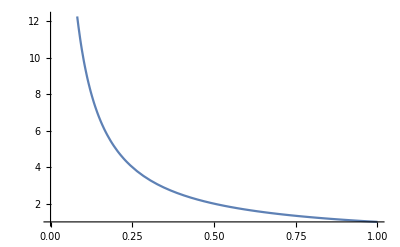

```mathematica
Plot[rofρ[ρ],{ρ,0,1}]
```

```mathematica
N[rofρ[1]^-1,64]
```

1.

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,z,y]+(2 ξ[t,z,y])/u+ξ[t,z,y]^2-2 Derivative[1,0,0][ξ][t,z,y];
```

```mathematica
AExpOfρ=AExp/.u->rofρ[ρ]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&
```

1/ρ^2+(2 ξ[t,z,y])/ρ+(ξ[t,z,y]^2-2 ξ^(1,0,0)[t,z,y])+(1/2+a3[t,0,z,y]) ρ+O[ρ]^2

```mathematica
AExpOfρ//Normal//Simplify
```

1/ρ^2+ρ (1/2+a3[t,0,z,y])+(2 ξ[t,z,y])/ρ+ξ[t,z,y]^2-2 ξ^(1,0,0)[t,z,y]

Let’s look for ξ

```mathematica
ξRule=Solve[2-2 Hypergeometric2F1[-1/3,1/2,2/3,-1]+2 ξ[t,z,y]==0, ξ[t,z,y]]
```

{{ξ[t,z,y]→-1+Hypergeometric2F1[-1/3,1/2,2/3,-1]}}

```mathematica
(-1+Hypergeometric2F1[-1/3,1/2,2/3,-1])^2-2 (-1+Hypergeometric2F1[-1/3,1/2,2/3,-1]) ξ[t,z,y]+ξ[t,z,y]^2/.ξRule
```

{0}

Ok

```mathematica
-1+Hypergeometric2F1[-1/3,1/2,2/3,-1]//N//FullForm
```

0.199314

```mathematica
AToMatch=ρ^-2(1-(b ρ)^3(1+u1^2+u2^2))//Simplify
```

1/ρ^2-2 ρ

```mathematica
AExpOfρ//Normal//Simplify
```

1/ρ^2+ρ (1/2+a3[t,0,z,y])+(2 ξ[t,z,y])/ρ+ξ[t,z,y]^2-2 ξ^(1,0,0)[t,z,y]

```mathematica
rofρ[1]
```

1

I compare the same order coefficient of ρ

```mathematica
a3[t,0,z,y]/.Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,z,y]]//Flatten
```

{-5/2}

As in the turbulence draft.

#### f1 (and f2)

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,z,y];
```

```mathematica
u/.u->rofρ[ρ]^-1
```

ρ/Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]

```mathematica
FExpOfρ=FExp/.u->rofρ[ρ]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&
```

f1[t,z,y] ρ+O[ρ]^2

```mathematica
FToMatch=(b ρ)^3/ρ^2 u0 u1
```

-√2 ρ

```mathematica
(*f1[t,z,y]/.*)Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,z,y]]//Flatten
```

{f1[t,z,y]→-√2}

Matching with the turbulence draft.

#### ξ (VEV of S)

1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y]

```mathematica
SExp=1/u+ξ[t,z,y]+u^2 s0[t,u,z,y];
```

```mathematica
SExpOfρ=SExp/.u->rofρ[ρ]^-1/.ξRule[[1]]//Series[#,{ρ,0,2}]&
```

1/ρ+(1/4+s0[t,0,z,y]) ρ^2+O[ρ]^3

```mathematica
SToMatch=((1/ρ^2 √(1+ρ^3))^(1/2)//Series[#,{ρ,0,2}]&)/.√(1/ρ^2)->1/ρ//Simplify
```

1/ρ+ρ^2/4+O[ρ]^3

```mathematica
s0[t,0,z,y]/.Solve[Coefficient[SToMatch,ρ^2]==Coefficient[SExpOfρ,ρ^2],s0[t,0,z,y]]//Flatten
```

{0}

Matching the turbulence draft.

#### B Function

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

The min value of u is:

```mathematica
uOfρAtInf=1/rofρ[ϵ]//N[#,64]&
```

1.×10^-20

The  horizon is at

```mathematica
uh=rofρ[1]^-1//N[#,$MinPrecision]&
```

0.

```mathematica
ϵ=10^-10
```

1/10000000000

```mathematica
Numericaluofρ=u/.DSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,0,1}][[1,1]];
```

```mathematica
Numericaluofρ
```

Function[{ρ},ρ/(10000000000 ρ-10000000000 ρ Hypergeometric2F1[-1/3,1/2,2/3,(-u1^2-u2^2)/1000000000000000000000000000000]+Hypergeometric2F1[-1/3,1/2,2/3,-((u1^2+u2^2) ρ^3)])]

```mathematica
Nρofu[u_]:=InverseFunction[Numericaluofρ][u];
```

```mathematica
Show[Plot[{Numericaluofρ[ρ],rofρ[ρ]^-1},{ρ,0,1},PlotStyle->{Thick,Dashed},PlotLegends->Automatic,PlotRange->All]]
```

Function::fpct: Too many parameters in {ρ,x,y} to be filled from Function[{ρ,x,y},Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3 Cos[Times[«3»]]^2]/ρ+1[x,y]][0.0000204286].

Function::fpct: Too many parameters in {ρ,x,y} to be filled from Function[{ρ,x,y},Hypergeometric2F1[-0.333333,0.5,0.666667,-1. ρ^3 Cos[Times[«2»]]^2]/ρ+1[x,y]][0.0000204286].

Function::fpct: Too many parameters in {ρ,x,y} to be filled from Function[{ρ,x,y},Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3 Cos[Times[«3»]]^2]/ρ+1[x,y]][0.0204286].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

-Graphics-

```mathematica
Numericaluofρ[0.1]//N
```

0.1/(1.×10^9-1.×10^9 Hypergeometric2F1[-0.333333,0.5,0.666667,1.×10^-30 (-1. u1^2-1. u2^2)]+Hypergeometric2F1[-0.333333,0.5,0.666667,-0.001 (u1^2+u2^2)])

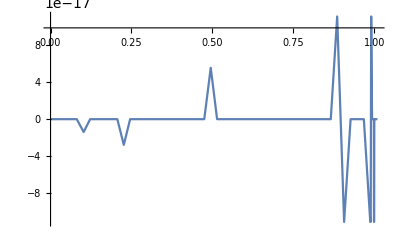

```mathematica
Plot[N[(Numericaluofρ[N[ρ,25]]-rofρ[N[ρ,25]]^-1),32],{ρ,0,uOuterDomains}]
```

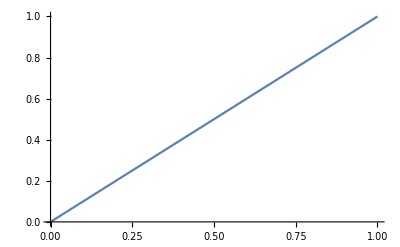

```mathematica
Plot[{InverseFunction[Numericaluofρ][u]},{u,Numericaluofρ[0],Numericaluofρ[1]}]
```

```mathematica
ρofuValues=(InverseFunction[Numericaluofρ])/@uValues;
```

```mathematica
ρofuValues[[3]]//Precision
```

64.

```mathematica
ρofr=InverseFunction[rofρ];
```

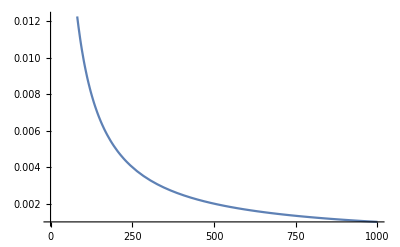

```mathematica
Plot[ρofr[r],{r,0.0001,1000}]
```

```mathematica
(*NDSolve[{D[SS[r],{r,2}]+SS[r]/4 D[-1/2Log[(1+(b ρofr[r])^3 u1^2)/(1+(b ρofr[r])^3 u2^2)],r]==0,SS[]},SS,r]*)
```

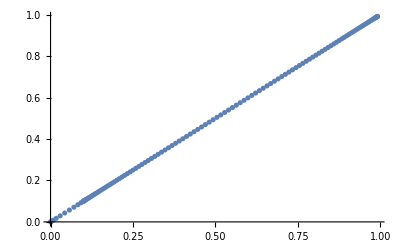

```mathematica
ListPlot[Transpose[{uValues,ρofuValues}]]
```

```mathematica
Log[1+ρofuValues[[-1]]]//N
```

0.688682

```mathematica
InverseFunction[Numericaluofρ]
```

Function[{ρ},ρ]

```mathematica
InverseFunction[Numericaluofρ][0.1]
```

0.1

```mathematica
Series[-1/2 Log[(1+(b InverseFunction[Numericaluofρ][u])^3 u1^2)/(1+(b InverseFunction[Numericaluofρ][u])^3 u2^2)],{u,0,1}]//N
```

```mathematica
-0.5 Log[1.+(InverseFunction[Function[{ρ},-(ρ/(100000000000000000000 ρ (-1+Hypergeometric2F1[-1/3,1/2,2/3,-1/1000000000000000000000000000000000000000000000000000000000000])-Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]))]][0])^3]//N
```

0.

```mathematica
InitialB=-1/2 Log[(1+(b ρofuValues)^3 u1^2)/(1+(b ρofuValues)^3 u2^2)] uValues^-3;
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
MachinePrecision//N
```

15.9546

```mathematica
"0005237856364186788"//StringLength
```

19

```mathematica
InitialB[[13]]
```

-0.000523785636418678850975434712444361577212064819515044454291039165

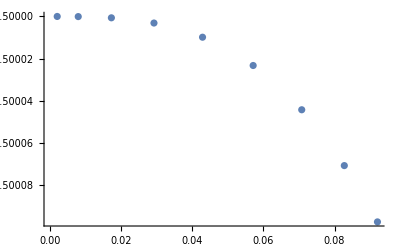

```mathematica
ListPlot[Transpose[{uValues,InitialB}][[;;10]],PlotRange->All]
```

```mathematica
InitialB[[1]]=-0.5
```

-0.5

```mathematica
ExportData=Join[{InitialB[[;;uInnerNodes]]},Table[InitialB[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1)]],{i,0,uOuterDomains-1}]];
```

```mathematica
ExportDataStr=Map[ToString,ExportData,{2}];
```

```mathematica
(Map[ToString,ExportData,{2}])[[1,2]]
```

-9
4.15404413895774069980019735045623554014062551747702550477813985 10

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_HBBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB.h5"]*)
```

Import::nffil: File /home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB.h5 not found during Import.

$Failed

```mathematica
rofρ[1]^-1//N
```

0.83381

```mathematica
ξ[t,z,y]/.ξRule[[1,1]]//N//FullForm//Print
```

0.199314

From Jecco

```mathematica
BJecco={0.,-4.1540441389577405*^-9,-2.500300908963684*^-7,-2.5695891453335936*^-6,-0.000012486068183858487,-0.00003943413060273409,-0.00009316605426870659,-0.0001772433293798708,-0.0002832865060861823,-0.0003902164153413663,-0.0004703414869800297,-5.001250541924607*^-7,-5.485590945575364*^-7,-7.167495814621999*^-7,-1.0862768461626769*^-6,-1.8417833206355192*^-6,-3.363723998512157*^-6,-6.396414444440832*^-6,-0.000012321680054236695,-0.000023555325109773874,-0.00004404274620410723,-0.00007975623863915222,-0.00013900121012125244,-0.00023225590525186122,-0.000371252324275859,-0.0005671075572358106,-0.000827557816298585,-0.0011536977142639693,-0.0015369836907464353,-0.0019574763284838552,-0.0023842318353721626,-0.0027783424598468395,-0.0030984304218701917,-0.0033076161162341237,-0.003380384740113918,-0.00345449443945899,-0.0036836014880946553,-0.004088501857099664,-0.004705331709318862,-0.005587538150634913,-0.006808088548816569,-0.008461243567947231,-0.010662903434809384,-0.013548228977439897,-0.017265045923792462,-0.021961610695061487,-0.02776780821085592,-0.03476988782453115,-0.04298043755640154,-0.05230729093894036,-0.06252707654595896,-0.0732705617587446,-0.08402708016108967,-0.09417349640179347,-0.10302904762332081,-0.10993141497777362,-0.11432286865610522,-0.11583042527839134,-0.11735567374165116,-0.1220099168986365,-0.1300306857770196,-0.14182021869242173,-0.15795342497748113,-0.17918580875059767,-0.2064579503475033,-0.24089200996032162,-0.28377459091172824,-0.3365192514693503,-0.40060100419435546,-0.4774541763491072,-0.5683236975071804,-0.6740576922208321,-0.7948257035259455,-0.9297425429627514,-1.0763771206025035,-1.2301433748824764,-1.383641950398675,-1.52620514063904,-1.6442188617607132,-1.7230419239413868,-1.7508532346410501};
```

```mathematica
InitialB[[-1]]
```

```mathematica
BJecco[[-1]]
```

-1.75085

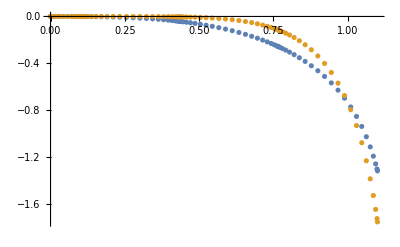

```mathematica
ListPlot[{Transpose[{uValues,InitialB}],Transpose[{uValues,BJecco}]},PlotRange->All]
```

### A function (for check)

#### A From Jecco

```mathematica
AJecco={-2.5,-2.500000004465527,-2.500000268782439,-2.5000027623109555,-2.5000134225856705,-2.500042392312419,-2.500100156980378,-2.500190549145636,-2.500304565096476,-2.5004195435590906,-2.5005057055958093,99.74994622655059,96.7122024669462,88.43187434940121,76.93542422354069,64.45017739493609,52.6402393099266,42.38757534163951,33.951100680417504,27.22831625744488,21.964354284370263,17.874886283486155,14.702896085112773,12.237184517233036,10.312686408589446,8.803903668325031,7.616862452729753,6.681784069613328,5.94712389377118,5.37498955593758,4.937730668253434,4.615454909884928,4.394255783818254,4.264985734960386,4.2224560544630005,4.18033311306929,4.057105802735426,3.861646748187931,3.6070729691513685,3.3087543257271816,2.982324618458698,2.6420964716614614,2.3000762714717293,1.9655759953163905,1.6452904366470416,1.3436635732197602,1.0633837960765615,0.8058919743412939,0.5718336345133503,0.36142372980503795,0.17471619375754718,0.011782811426974526,-0.127189014857127,-0.2418682313353343,-0.33180887285977206,-0.3965197305420878,-0.4355551627115424,-0.4486041625262347,-0.46163190758447453,-0.5003516679176622,-0.5637198109716819,-0.6501437605624925,-0.757672949220536,-0.8842165760410374,-1.0277556251420068,-1.186523902725671,-1.359143249191712,-1.5447076278835181,-1.7428163121030578,-1.9535560504513279,-2.1774244402273144,-2.415170118147356,-2.6674968885768964,-2.934535920766238,-3.214936620079632,-3.504394949974637,-3.793536729379919,-4.065547820476541,-4.295068777842759,-4.451228148921696,-4.506950755180788};
```

#### Analytic expression for A

```mathematica
A[u_]:=1/Nρofu[u]^2(1-b^3 Nρofu[u]^3(1+u1^2+u2^2));
Afin[u_]:=(-1/u^3+1/(u Nρofu[u]^2)(1-2 Nρofu[u]^3));
```

```mathematica
(A/@uValues)[[2]]
```

Power::infy: Infinite expression 1/0 encountered.

243780.664536102072948517054739809672724530907193429439060241634

```mathematica
uValues[[3]]//Precision
```

64.

#### Outer Nodes

```mathematica
uValues[[uInnerNodes+1]]//N
```

0.101552

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(A/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],AJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0075]},ImageSize->Large,PlotLabel->A Function Comparison]
```

-Graphics-

```mathematica
FinalP=-1;
```

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;FinalP]],(A/@uValues[[uInnerNodes+1;;FinalP]])-AJecco[[uInnerNodes+1;;FinalP]]}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large,PlotLabel->Absolute Error]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;FinalP]],((A/@uValues[[uInnerNodes+1;;FinalP]])-AJecco[[uInnerNodes+1;;FinalP]])/(A/@uValues[[uInnerNodes+1;;FinalP]])}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large,PlotLabel->Relative Error]
```

-Graphics-

#### Inner Nodes

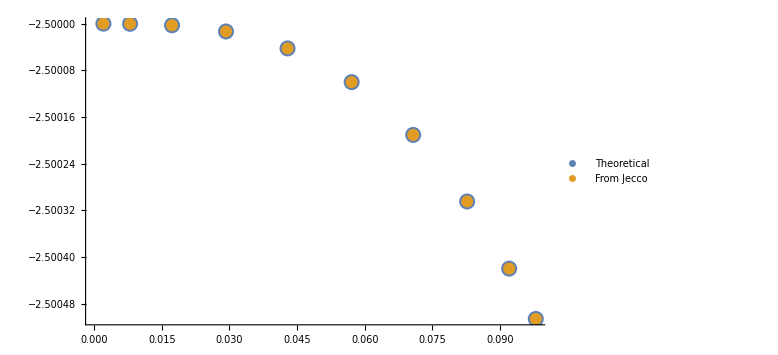

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Afin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],AJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

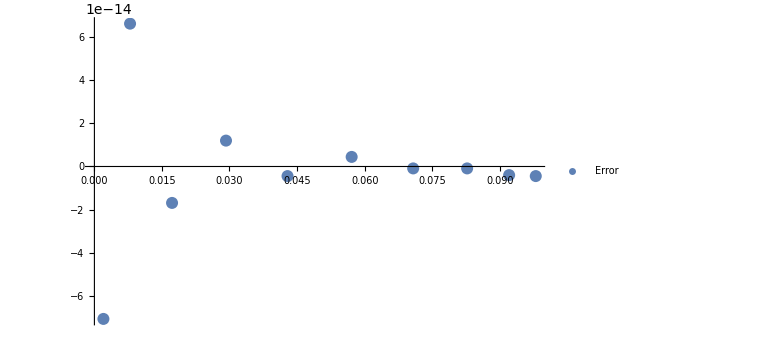

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],(Afin/@uValues[[2;;uInnerNodes-1]])-AJecco[[2;;uInnerNodes-1]]}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

```mathematica
AJecco[[3]]//FullForm
```

-2.5

### S function check

#### From Jecco

```mathematica
SJecco={0.,8.598014472498873*^-23,-2.970359103054401*^-21,-2.311669785954828*^-18,-2.654461574321596*^-16,-8.36191475146011*^-15,-1.1026791059330783*^-13,-7.59216054875459*^-13,-3.0996145403683463*^-12,-8.100666520616076*^-12,-1.4184845897796747*^-11,9.99999999999983,9.847138697790744,9.417929384269788,8.787491668396749,8.047419736242098,7.2790030125128675,6.539888335815762,5.863270418945598,5.263458174340948,4.74263165110307,4.296320092301297,3.917068886651059,3.596599583591419,3.326945537029655,3.100968049864969,2.912529264068205,2.7564908739437937,2.6286349736469923,2.5255587429197,2.4445690304738674,2.3835888667365377,2.341080648773805,2.315987211101197,2.3076905078728407,2.299453032350873,2.27523938388497,2.2364762330703307,2.1853268340647336,2.1244241882461696,2.0565862477019228,1.9845638053986885,1.91085284974246,1.8375816363214885,1.7664657840944542,1.6988153408130353,1.6355753641876942,1.5773837320456312,1.5246340816268826,1.4775361395996298,1.4361692539811872,1.4005273643869944,1.3705550509634163,1.3461749942305121,1.3273075220541792,1.3138832122187643,1.3058498846070212,1.303175664326449,1.3005115040194895,1.2926275850126256,1.279838738046411,1.2626352261077476,1.241636641674311,1.2175370141315607,1.1910478502454753,1.162844800436054,1.1335219547486957,1.1035561642324339,1.0732828893358188,1.042885281632606,1.0123995918389788,0.9817423105788645,0.9507670013099814,0.9193602209835439,0.8875837418224134,0.855860130341358,0.8251739736888752,0.7972154768074234,0.7743344496012027,0.7591530302341405,0.7538134700571201};
```

#### Analytic S

```mathematica
S[uValues[[2]]]
```

493.741500787082287928241378074095825909241161859328449063633153

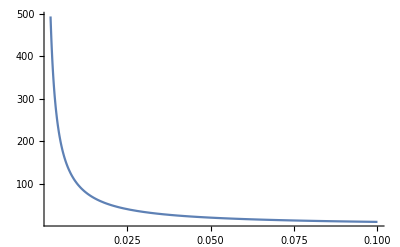

```mathematica
Plot[S[u],{u,uValues[[2]],0.1},PlotRange->All]
```

```mathematica
S[u_]:=(1/Nρofu[u]^2(1+b^3 Nρofu[u]^3(u1^2+u2^2))^(1/2))^(1/2);
Sfin[u_]:=(-1/u^3+1/u^2(1/Nρofu[u]^2(1+b^3 Nρofu[u]^3(u1^2+u2^2))^(1/2))^(1/2));
```

#### Inner Nodes

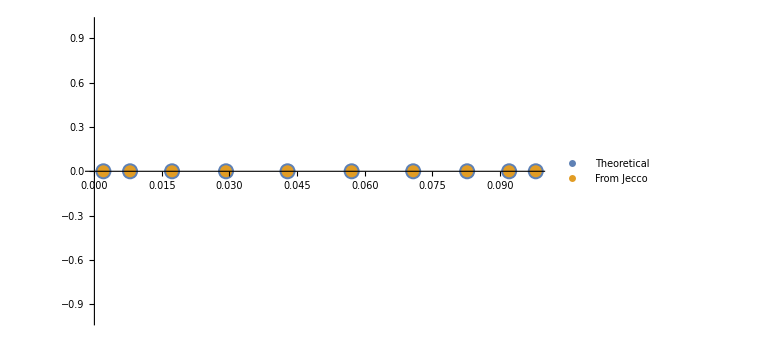

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Sfin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],SJecco[[2;;uInnerNodes-1,1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

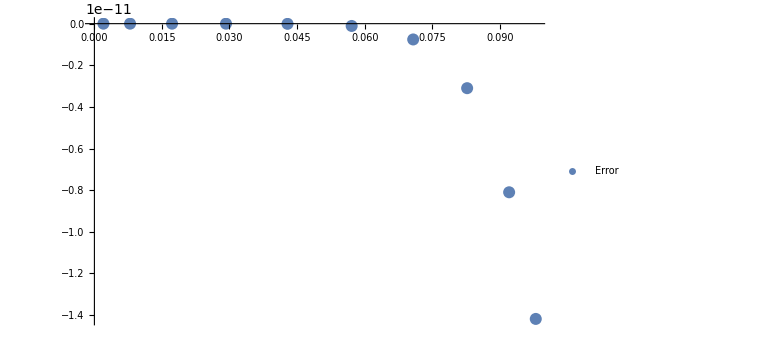

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],(*(Sfin/@uValues[[2;;uInnerNodes-1]])-*)(*uValues[[2;;uInnerNodes-1]]^-1+uValues[[2;;uInnerNodes-1]]^2*)SJecco[[2;;uInnerNodes-1]]}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

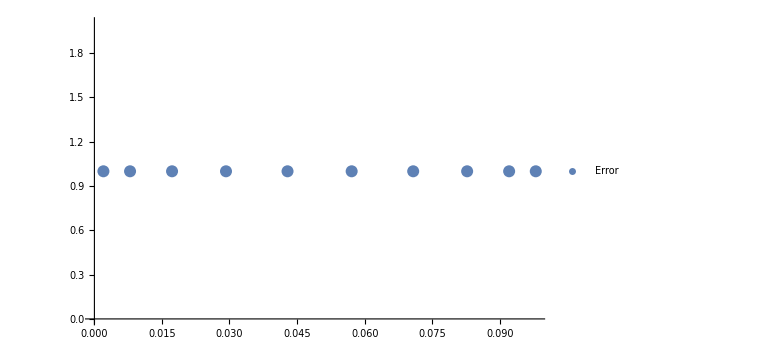

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],((Sfin/@uValues[[2;;uInnerNodes-1]])-SJecco[[2;;uInnerNodes-1]])/(Sfin/@uValues[[2;;uInnerNodes-1]])}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

#### Outer Nodes

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(S/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],SJecco[[1,uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

-Graphics-

```mathematica
endV=-48;
```

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;endV]],(S/@uValues[[uInnerNodes+1;;endV]])-SJecco[[1,uInnerNodes+1;;endV]]}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large(*,PlotLabel->Error*)]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-endV]],((S/@uValues[[uInnerNodes+1;;-endV]])-SJecco[[uInnerNodes+1;;-endV]])/(S/@uValues[[uInnerNodes+1;;-endV]])}]},PlotRange->All,PlotLabels->{"Relative Error"},ImageSize->Large(*,PlotLabel->Error*)]
```

-Graphics-

```mathematica
SJecco[[13]]//FullForm
```

9.84714

```mathematica
S[uValues[[13]]]//FullForm
```

9.84713849536516181298506082981912602951554235152569963404520544

### F function

#### From Jecco

```mathematica
FxJecco={-1.4142135623730396,-1.4142135623730496,-1.4142135623729573,-1.4142135623605776,-1.4142135620790564,-1.4142135594408454,-1.414213546006693,-1.41421350314056,-1.4142134110685944,-1.4142132753011725,-1.414213145320381,-0.1414213090835987,-0.14361664728751164,-0.15016176367897627,-0.1609347230636518,-0.17573481588432102,-0.19428627631503673,-0.21624337577327493,-0.24119677966715833,-0.2686810272731556,-0.2981829773748407,-0.32915106605125877,-0.36100525315463244,-0.3931475875223115,-0.4249733722631997,-0.4558829209859815,-0.4852938163315408,-0.5126533962728481,-0.537450932127533,-0.5592287232657304,-0.5775912465791126,-0.5922116736523471,-0.602835517374139,-0.6092817756348872,-0.6114424779396028,-0.6136024156609617,-0.6200373146872048,-0.6306127658004901,-0.645105865597385,-0.6632069098837903,-0.6845218893032525,-0.7085760776547411,-0.734819296129199,-0.7626338195868729,-0.7913462797774291,-0.8202451519856184,-0.8486052533230746,-0.8757198849981547,-0.9009396624005892,-0.9237147770563421,-0.9436348645484826,-0.9604586297577941,-0.974124925608617,-0.9847389378940123,-0.9925316879917194,-0.9977974252595044,-1.0008198929115566,-1.001802751420073,-1.002769784427095,-1.005557190307738,-1.0098226560512107,-1.014992290151557,-1.0202582649414667,-1.0245812465970945,-1.0267039642918698,-1.0251845417790477,-1.0184599975958017,-1.004950552354795,-0.9832124864865416,-0.9521395152814932,-0.9111987662865748,-0.8606682152608452,-0.8018222437476017,-0.7369999109534688,-0.6694986292943143,-0.6032732401203474,-0.5424833637617006,-0.4909968132288907,-0.45198488171729295,-0.427705239412386,-0.41947018428385685};
```

#### Analytic

```mathematica
Fx[u_]:=b^3 Nρofu[u]u1 u0d;
```

```mathematica
Fxfin[u_]:=1/u b^3 Nρofu[u]u1 u0d;
```

#### Outer Nodes

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(Fx/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],FxJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(Fx/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],FxJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

#### Inner Nodes

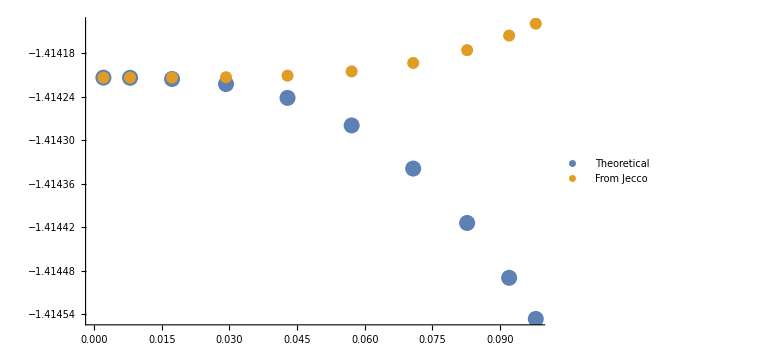

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Fxfin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],FxJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

## Inhomogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

#### ρ

```mathematica
RandomFactor[x_,y_]=Sum[Random[]/60(Cos[(i Pi y)/(xMax-xMin)]Sin[(i Pi x)/(xMax-xMin)]+Cos[(i Pi y)/(xMax-xMin)]Sin[(j Pi x)/(xMax-xMin)]+Cos[(j Pi y)/(xMax-xMin)]Sin[(j Pi x)/(xMax-xMin)]+Cos[(j Pi y)/(xMax-xMin)]Sin[(i Pi x)/(xMax-xMin)]),{i,1,4},{j,0,0}];
```

```mathematica
δuxToInt[x_,y_]:=Table[{{x,y},Cos[qx y](*+RandomFactor[x,y]*)},{x,xMin,xMax,0.1},{y,yMin,yMax,0.1}];
```

```mathematica
Intδux=Interpolation[δuxToInt[x,y]//Flatten[#,1]&]
```

InterpolatingFunction[…]

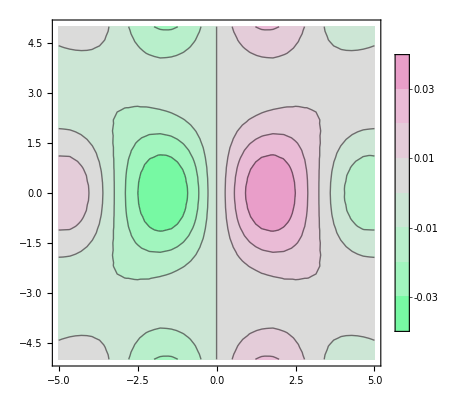

```mathematica
ContourPlot[RandomFactor[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"MintColors"(*,MaxRecursion->3*)(*,PlotPoints->20*)]
```

```mathematica
ClearAll[u1d,u0d,u2d]
qx=(20Pi)/(xMax-xMin);
qy=Pi/(yMax-yMin);
(*u0d[x_,y_]=-2^(1/2);*)

u1d[x_,y_]:=1/2 Cos[qx y]+RandomFactor[x,y];
u2d[x_,y_]:=(*5/10 Cos[qy y]*)0;
b=1;
```

```mathematica
ContourPlot[u1d[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,PlotLegends->Automatic,ColorFunction->"MintColors"(*,MaxRecursion->3*)(*,PlotPoints->20*)]
```

-Graphics-

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[1,1,2]]
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Q: Boundary conditions: at ρ=0 or =1?
A: At 0
Q: Do we know where is the horizon in the u domain?
A: Yes at u(ρ=1).

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρ
```

Function[{ρ,x,y},1/ρ 1. Hypergeometric2F1[-0.333333,0.5,0.666667,-1. ρ^3 (0.5 Cos[6.28319 y]+0.00593873 (1.+1. Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+1. Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+1. Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+1. Cos[1.25664 y]) Sin[1.25664 x])^2]+C[1][x,y]]

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->rofρ[ρ,x,y]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&
```

1/ρ^2+(2. ξ[t,x,y]+2. C[1][x,y])/ρ+(ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2-2 ξ^(1,0,0)[t,x,y])+(1. a3[t,0,x,y]+0.5 (0.5 Cos[6.28319 y]+0.00593873 (1.+1. Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+1. Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+1. Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+1. Cos[1.25664 y]) Sin[1.25664 x])^2) ρ+O[ρ]^2

```mathematica
AExpOfρ//Normal//Simplify
```

1./ρ^2+ρ (1. a3[t,0,x,y]+0.5 (0.5 Cos[6.28319 y]+0.00593873 (1.+1. Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+1. Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+1. Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+1. Cos[1.25664 y]) Sin[1.25664 x])^2)+ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2+(2. ξ[t,x,y]+2. C[1][x,y])/ρ-2 ξ^(1,0,0)[t,x,y]

```mathematica
AToMatch=ρ^-2(1-(b ρ)^3(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-ρ (1+(1/2 Cos[2 π y]+0.00593873 (1+Cos[(π y)/10]) Sin[(π x)/10]+0.000587424 (1+Cos[(π y)/5]) Sin[(π x)/5]+0.0143495 (1+Cos[(3 π y)/10]) Sin[(3 π x)/10]+0.00231739 (1+Cos[(2 π y)/5]) Sin[(2 π x)/5])^2)

```mathematica
AExpOfρ//Normal//Simplify
```

1./ρ^2+ρ (1. a3[t,0,x,y]+0.5 (0.5 Cos[6.28319 y]+0.00593873 (1.+1. Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+1. Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+1. Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+1. Cos[1.25664 y]) Sin[1.25664 x])^2)+ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2+(2. ξ[t,x,y]+2. C[1][x,y])/ρ-2 ξ^(1,0,0)[t,x,y]

Let' s look for ξ

```mathematica
c1Rule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  C[1][x,y]]//Flatten
```

{C[1][x,y]→-1. ξ[t,x,y]}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule
```

0.-2 ξ^(1,0,0)[t,x,y]

xi can’t depend on t

I compare the same order coefficient of ρ

```mathematica
a3Rule =Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,x,y]][[1]];
```

```mathematica
a3[t,0,x,y]/.a3Rule//Simplify(*//Expand*)//Collect[#,Cos[2 π y]]&
```

-1. (1.+1. (0.5 Cos[6.28319 y]+0.00593873 (1.+Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+Cos[1.25664 y]) Sin[1.25664 x])^2+0.5 (0.5 Cos[6.28319 y]+0.00593873 (1.+1. Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+1. Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+1. Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+1. Cos[1.25664 y]) Sin[1.25664 x])^2)

From Chasler paper a3 should be

```mathematica
-1/2(-1+3 u0d[x,y]^2)//Simplify
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-1.-0.375 Cos[6.28319 y]^2-0.0000529027 (1.+1. Cos[0.314159 y])^2 Sin[0.314159 x]^2-5.17601×10^-7 Sin[0.628319 x]^2-1.0352×10^-6 Cos[0.628319 y] Sin[0.628319 x]^2-5.17601×10^-7 Cos[0.628319 y]^2 Sin[0.628319 x]^2-0.0000252878 Sin[0.628319 x] Sin[0.942478 x]-0.0000252878 Cos[0.628319 y] Sin[0.628319 x] Sin[0.942478 x]-0.0000252878 Cos[0.942478 y] Sin[0.628319 x] Sin[0.942478 x]-0.0000252878 Cos[0.628319 y] Cos[0.942478 y] Sin[0.628319 x] Sin[0.942478 x]-0.000308863 Sin[0.942478 x]^2-0.000617726 Cos[0.942478 y] Sin[0.942478 x]^2-0.000308863 Cos[0.942478 y]^2 Sin[0.942478 x]^2-4.08387×10^-6 Sin[0.628319 x] Sin[1.25664 x]-4.08387×10^-6 Cos[0.628319 y] Sin[0.628319 x] Sin[1.25664 x]-4.08387×10^-6 Cos[1.25664 y] Sin[0.628319 x] Sin[1.25664 x]-4.08387×10^-6 Cos[0.628319 y] Cos[1.25664 y] Sin[0.628319 x] Sin[1.25664 x]-0.0000997602 Sin[0.942478 x] Sin[1.25664 x]-0.0000997602 Cos[0.942478 y] Sin[0.942478 x] Sin[1.25664 x]-0.0000997602 Cos[1.25664 y] Sin[0.942478 x] Sin[1.25664 x]-0.0000997602 Cos[0.942478 y] Cos[1.25664 y] Sin[0.942478 x] Sin[1.25664 x]-8.05544×10^-6 Sin[1.25664 x]^2-0.0000161109 Cos[1.25664 y] Sin[1.25664 x]^2-8.05544×10^-6 Cos[1.25664 y]^2 Sin[1.25664 x]^2+Sin[0.314159 x] ((-0.0000104657+Cos[0.314159 y] (-0.0000104657-0.0000104657 Cos[0.628319 y])-0.0000104657 Cos[0.628319 y]) Sin[0.628319 x]+(-0.000255654+Cos[0.314159 y] (-0.000255654-0.000255654 Cos[0.942478 y])-0.000255654 Cos[0.942478 y]) Sin[0.942478 x]+(-0.000041287+Cos[0.314159 y] (-0.000041287-0.000041287 Cos[1.25664 y])-0.000041287 Cos[1.25664 y]) Sin[1.25664 x])+Cos[6.28319 y] ((-0.00890809-0.00890809 Cos[0.314159 y]) Sin[0.314159 x]+(-0.000881137-0.000881137 Cos[0.628319 y]) Sin[0.628319 x]-0.0215243 Sin[0.942478 x]-0.0215243 Cos[0.942478 y] Sin[0.942478 x]-0.00347608 Sin[1.25664 x]-0.00347608 Cos[1.25664 y] Sin[1.25664 x])

Export a3 Initial data

```mathematica
a3Data=Table[a3[t,0,x,y]/.a3Rule/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
a3AttributesAndData={"a3"->a3Data};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5",a3AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initiala3_BBB.h5","Data"]//Keys
```

{/a3}

#### f1

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,z,y]+Derivative[0,1,0][ξ][t,x,y];
```

```mathematica
FExpOfρ=FExp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,4}]&
```

ξ^(0,1,0)[t,x,y]+1. f1[t,z,y] ρ-1. (f1[t,z,y] C[1][x,y]) ρ^2+1. f1[t,z,y] (C[1][x,y])^2 ρ^3+1. f1[t,z,y] (-0.25 (0.5 Cos[6.28319 y]+0.00593873 (1.+1. Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+1. Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+1. Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+1. Cos[1.25664 y]) Sin[1.25664 x])^2-1. (C[1][x,y])^3) ρ^4+O[ρ]^5

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

∂_u Fy=

```mathematica
Series[D[rofρ[ρ,x,y],ρ],{ρ,0,3}]
```

-1/ρ^2+0.5 (0.5 Cos[6.28319 y]+0.00593873 (1.+1. Cos[0.314159 y]) Sin[0.314159 x]+0.000587424 (1.+1. Cos[0.628319 y]) Sin[0.628319 x]+0.0143495 (1.+1. Cos[0.942478 y]) Sin[0.942478 x]+0.00231739 (1.+1. Cos[1.25664 y]) Sin[1.25664 x])^2 ρ+O[ρ]^4

Chasler paper

```mathematica
(*FToMatch=-(b ρ(*ofu[{0,x,y}]*))^3/(ρ(*ofu[{0,x,y}]*))^2u0d[x,y] u1d[x,y]*)
```

```mathematica
fxRule=Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,z,y]]//Simplify;
```

From Chasler paper this should be.

```mathematica
-u0d[x,y] u1d[x,y]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

5.84951×10^-36 √(2.92255×10^70+7.30637×10^69 Cos[6.28319 y]^2+1.73562×10^68 Cos[6.28319 y] Sin[0.314159 x]+1.73562×10^68 Cos[0.314159 y] Cos[6.28319 y] Sin[0.314159 x]+1.03074×10^66 Sin[0.314159 x]^2+2.06147×10^66 Cos[0.314159 y] Sin[0.314159 x]^2+1.03074×10^66 Cos[0.314159 y]^2 Sin[0.314159 x]^2+1.71678×10^67 Cos[6.28319 y] Sin[0.628319 x]+1.71678×10^67 Cos[0.628319 y] Cos[6.28319 y] Sin[0.628319 x]+2.03909×10^65 Sin[0.314159 x] Sin[0.628319 x]+2.03909×10^65 Cos[0.314159 y] Sin[0.314159 x] Sin[0.628319 x]+2.03909×10^65 Cos[0.628319 y] Sin[0.314159 x] Sin[0.628319 x]+2.03909×10^65 Cos[0.314159 y] Cos[0.628319 y] Sin[0.314159 x] Sin[0.628319 x]+1.00848×10^64 Sin[0.628319 x]^2+2.01695×10^64 Cos[0.628319 y] Sin[0.628319 x]^2+1.00848×10^64 Cos[0.628319 y]^2 Sin[0.628319 x]^2+4.19371×10^68 Cos[6.28319 y] Sin[0.942478 x]+4.19371×10^68 Cos[0.942478 y] Cos[6.28319 y] Sin[0.942478 x]+4.98106×10^66 Sin[0.314159 x] Sin[0.942478 x]+4.98106×10^66 Cos[0.314159 y] Sin[0.314159 x] Sin[0.942478 x]+4.98106×10^66 Cos[0.942478 y] Sin[0.314159 x] Sin[0.942478 x]+4.98106×10^66 Cos[0.314159 y] Cos[0.942478 y] Sin[0.314159 x] Sin[0.942478 x]+4.92698×10^65 Sin[0.628319 x] Sin[0.942478 x]+4.92698×10^65 Cos[0.628319 y] Sin[0.628319 x] Sin[0.942478 x]+4.92698×10^65 Cos[0.942478 y] Sin[0.628319 x] Sin[0.942478 x]+4.92698×10^65 Cos[0.628319 y] Cos[0.942478 y] Sin[0.628319 x] Sin[0.942478 x]+6.01778×10^66 Sin[0.942478 x]^2+1.20356×10^67 Cos[0.942478 y] Sin[0.942478 x]^2+6.01778×10^66 Cos[0.942478 y]^2 Sin[0.942478 x]^2+6.77268×10^67 Cos[6.28319 y] Sin[1.25664 x]+6.77268×10^67 Cos[1.25664 y] Cos[6.28319 y] Sin[1.25664 x]+8.04421×10^65 Sin[0.314159 x] Sin[1.25664 x]+8.04421×10^65 Cos[0.314159 y] Sin[0.314159 x] Sin[1.25664 x]+8.04421×10^65 Cos[1.25664 y] Sin[0.314159 x] Sin[1.25664 x]+8.04421×10^65 Cos[0.314159 y] Cos[1.25664 y] Sin[0.314159 x] Sin[1.25664 x]+7.95687×10^64 Sin[0.628319 x] Sin[1.25664 x]+7.95687×10^64 Cos[0.628319 y] Sin[0.628319 x] Sin[1.25664 x]+7.95687×10^64 Cos[1.25664 y] Sin[0.628319 x] Sin[1.25664 x]+7.95687×10^64 Cos[0.628319 y] Cos[1.25664 y] Sin[0.628319 x] Sin[1.25664 x]+1.94369×10^66 Sin[0.942478 x] Sin[1.25664 x]+1.94369×10^66 Cos[0.942478 y] Sin[0.942478 x] Sin[1.25664 x]+1.94369×10^66 Cos[1.25664 y] Sin[0.942478 x] Sin[1.25664 x]+1.94369×10^66 Cos[0.942478 y] Cos[1.25664 y] Sin[0.942478 x] Sin[1.25664 x]+1.56949×10^65 Sin[1.25664 x]^2+3.13898×10^65 Cos[1.25664 y] Sin[1.25664 x]^2+1.56949×10^65 Cos[1.25664 y]^2 Sin[1.25664 x]^2) (1/2 Cos[2 π y]+0.00593873 (Sin[(π x)/10]+Cos[(π y)/10] Sin[(π x)/10])+0.000587424 (Sin[(π x)/5]+Cos[(π y)/5] Sin[(π x)/5])+0.0143495 (Sin[(3 π x)/10]+Cos[(3 π y)/10] Sin[(3 π x)/10])+0.00231739 (Sin[(2 π x)/5]+Cos[(2 π y)/5] Sin[(2 π x)/5]))

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

ξ can’t depend on x!

Export fx initial data

```mathematica
fxData=Table[fx[t,0,x,y]/.fxRule/.x->xValues[[i]]/.y->yValues[[j]],{i,1,xValues//Length},{j,1,yValues//Length}];
```

```mathematica
fxAttributesAndData={"fx"->a3Data};
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5",fxAttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/Initialfx_BBB.h5","Data"]//Keys
```

{/fx}

#### f2

Same procedure as above but for F1.

```mathematica
F2Exp=u f2[t,z,y]+Derivative[0,0,1][ξ][t,x,y];
```

```mathematica
F2ExpOfρ=F2Exp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,3}]&
```

ξ^(0,0,1)[t,x,y]+f2[t,z,y] ρ-f2[t,z,y] C[1][x,y] ρ^2+f2[t,z,y] (C[1][x,y])^2 ρ^3+O[ρ]^4

Turbulence draft

```mathematica
(*FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]*)
```

Chasler paper

```mathematica
FToMatch=-(b ρ)^3/ρ^2 u0d[x,y] u2d[x,y]
```

0

```mathematica
(*f1[t,z,y]/.*)Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,z,y]]//Flatten
```

{f1[t,z,y]→0}

From Chasler paper this should be.

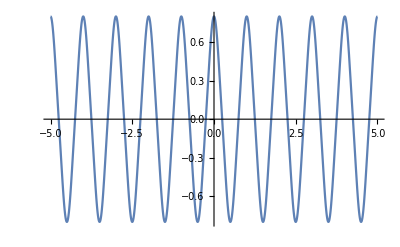

```mathematica
Plot[-u0d[x,y]u1d[x,y],{y,yMin,yMax}]
```

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

ξ can’t depend on x!

#### ξ

Does this section makes sense? The asymptotic expansion of S doesn’t say much about ξ

1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y]

```mathematica
SExp=1/u+ξ[t,x,y]+u^2 s2[t,u,x,y];
```

```mathematica
SExpOfρ=SExp/.u->rofρ[ρ,x,y]^-1/.c1Rule(*/.ξRule[[1]]*)//Series[#,{ρ,0,2}]&
```

1/ρ+(1/4 Cos[(π y)/5]^2+s2[t,0,x,y]) ρ^2+O[ρ]^3

```mathematica
SToMatch=((1/ρ^2 √(1+ρ^3))^(1/2)//Series[#,{ρ,0,2}]&)/.√(1/ρ^2)->1/ρ//Simplify
```

1/ρ+ρ^2/4+O[ρ]^3

```mathematica
(*s0[t,0,x,y]/.*)s0Rule=Solve[Coefficient[SToMatch,ρ^2]==Coefficient[SExpOfρ,ρ^2],s2[t,0,x,y]]//Flatten
(*s0Rule[[1,1]]=ξ[t,x,y];
s0Rule*)
```

{s2[t,0,x,y]→1/4 (1-Cos[(π y)/5]^2)}

```mathematica
1/4 (1-Cos[2 π x]^2)/.x->1
```

0

### B Function

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
ClearAll[uofρ]
```

```mathematica
(*uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys*)
```

```mathematica
uofρ=Function[{ρs,xs,ys},rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys]
```

Function[{ρs,xs,ys},1/rofρ⟦2⟧/.c1Rule⟦1⟧/.ξ→Function[{t,x,y},0]/.ρ→ρs/.x→xs/.y→ys]

Horizon location

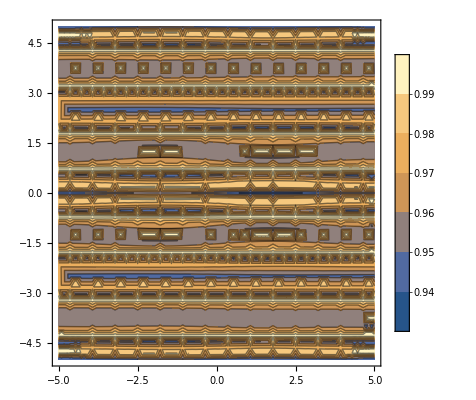

```mathematica
ContourPlot[uofρ[1,x,y],{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,PlotRange->All]
```

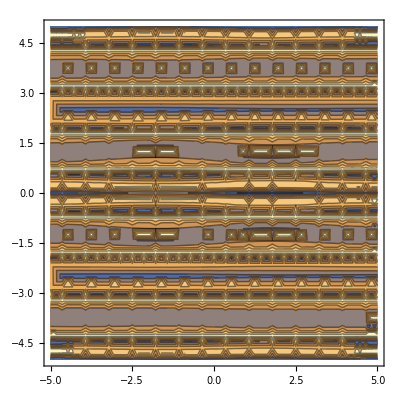

```mathematica
ContourPlot[uofρ[1,x,y],{x,xMin,xMax},{y,yMin,yMax}(*,PlotPoints->25,MaxRecursion->4*)]
```

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3];
```

```mathematica
ClearAll[ρofu]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
ρofu[{0.91,1,1}]
```

0.962316

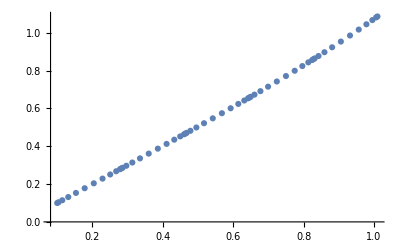

```mathematica
ListPlot[{uValues[[uInnerNodes;;]],Table[ρofu[{uValues[[i]],xMin,yMin}],{i,uInnerNodes,uValues//Length}]}//Transpose(*,{x,-5,5}*),PlotRange->All]
```

```mathematica
ρofuValues=Table[ρofu[MyGrid[[i,j,k]]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];//AbsoluteTiming
```

{100.691,Null}

```mathematica
ρofuValues[[1, 1,;;]]//Dimensions
```

{72}

```mathematica
u1Values=Table[u1d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.236512,Null}

```mathematica
u2Values=Table[u2d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.004224,Null}

```mathematica
u0Values=Table[u0d[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{2.16136,Null}

#### B Function

```mathematica
InitialBAnalytic[u_,x_,y_]:=-1/2 Log[(1+(b ρofu[{u,x,y}])^3 u1d[x,y]^2)/(1+(b ρofu[{u,x,y}])^3 u2d[x,y]^2)] u^-3;
```

```mathematica
InitialB1=Table[N[SeriesCoefficient[InitialBAnalytic[u,xValues[[i]],yValues[[j]]],{u,uValues[[1]],0}]//Normal],{i,1,xNodes},{j,1,yNodes}];//AbsoluteTiming
```

{458.916,Null}

```mathematica
SeriesCoefficient[InitialBAnalytic[u,1,1],{u,uValues[[1]],0}]//N
```

-0.545948

```mathematica
InitialB=Table[N[-1/2 Log[(1+(b ρofuValues[[ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[ui,xi,yi]])^3 u2Values[[xi,yi]]^2)] uValues[[ui]]^-3,MachinePrecision],{ui,1,uValues//Length},{xi,1,xNodes},{yi,1,yNodes}];
InitialB[[1]]=InitialB1(*Table[-0.5,{i,1,25},{j,1,25}]*);
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot3D[InitialB1]
```

-Graphics3D-

```mathematica
InitialB//Dimensions
```

{56,60,72}

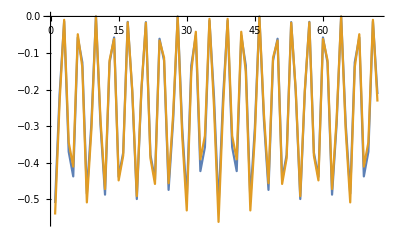

```mathematica
ListPlot[{InitialB[[1,1,;;]],Table[-u1d[1,yValues[[i]]]^2/2,{i,1,yValues//Length}]},Joined->True]
```

```mathematica
ExportData=Join[{InitialB[[;;uInnerNodes,;;,;;]]},Table[InitialB[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000236,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000104,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5

```mathematica
ExpCheck=Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5","Data"]
```

```mathematica
ExpCheck//Keys
```

{/2,/1,/3,/4,/5,/6,/7}

### B function check

```mathematica
BJecco={{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-0.033493649053890295,-0.03349364905855045,-0.0334936493343802,-0.03349365193651519,-0.03349366306099058,-0.03349369329129428,-0.033493753565551745,-0.0334938478742294,-0.03349396681185405,-0.033494086732744247,-0.033494176584830025,-0.00003349420998243639,-0.0000383408229739732,-0.00005511301802758109,-0.00009046018251878054,-0.0001546007844791895,-0.00025830138541141194,-0.00040727235239798707,-0.0005957041319401719,-0.0008024192126957073,-0.0009929293812347725,-0.00112818585327499,-0.0011772048435751271,-0.0012276252510670025,-0.001383004083966349,-0.0016537356163873103,-0.0020506195316611466,-0.0025755963558059887,-0.0032111280366521125,-0.003912148130728782,-0.004605284935774259,-0.005198469971801375,-0.005600108153947345,-0.005742343675996626,-0.0058869814420021895,-0.006323112663144419,-0.0070538145394720446,-0.008072968933051868,-0.009351040467220052,-0.010821053701034342,-0.012370804869543624,-0.013847204374656037,-0.015075663350004685,-0.015891985498865637,-0.01617838468101607,-0.016468260988514744,-0.017334510422222855,-0.018762026434215612,-0.02071038413196044,-0.02309565480932204,-0.02577426954613679,-0.028537108102657537,-0.031121009516285696,-0.0332405004589885,-0.03463537165490675,-0.03512237363664434},{-0.12499999999999971,-0.12500000006490694,-0.1250000039067199,-0.12500004014980118,-0.1250001950941252,-0.12500061615140623,-0.12500145568117,-0.1250027692879353,-0.12500442599634368,-0.12500609645729144,-0.12500734810620975,-0.00012500781334645486,-0.00014309739450143696,-0.0002057000712092864,-0.0003376437267134174,-0.0005770998921858216,-0.0009643343083348086,-0.0015208078028587574,-0.0022250105556642927,-0.002997959991314874,-0.0037107046616476898,-0.004216958555012769,-0.004400479144786443,-0.004589272297130162,-0.005171234601664919,-0.006185839644712632,-0.0076745910958348,-0.009646347849305244,-0.012037189747399124,-0.014679319409560883,-0.017296847263246116,-0.01954098242097138,-0.021062595805776987,-0.021601872929270963,-0.02215048126296711,-0.023806084759637396,-0.026584528897509226,-0.030469518692668736,-0.035357658636797074,-0.041002413472865235,-0.04697979630092223,-0.052699871744851405,-0.057478651511610114,-0.060664006302791215,-0.06178342965529626,-0.06291743772690138,-0.06631222864656677,-0.07192633984768551,-0.07962902636717838,-0.08912344210665082,-0.09987204406293627,-0.11105711117829983,-0.12161079507514587,-0.13033651355000964,-0.13611364185448607,-0.1381372128489238},{-0.25000000000000483,-0.25000000025962776,-0.2500000156268804,-0.2500001605992941,-0.2500007803786119,-0.2500024646266827,-0.2500058228422174,-0.25001107757713376,-0.25001770507202226,-0.2500243878909096,-0.2500293954201384,-0.00025003125677244505,-0.0002862152705564316,-0.00041144246886781397,-0.0006754015183303815,-0.0011545331364276395,-0.0019295999941217289,-0.0030439341020566508,-0.004454989463324086,-0.006004951041974771,-0.007435260833358391,-0.00845182055097732,-0.00882045969800365,-0.00919976167416754,-0.01036943375892844,-0.012410325959085013,-0.015408812717133805,-0.0193872037646413,-0.024222112357037386,-0.029579289628061948,-0.03490136314732546,-0.03947609347515521,-0.042584234968343466,-0.04368702459335975,-0.044809558707848314,-0.04820123974883841,-0.05390703416708342,-0.061914735158669396,-0.07203994659732829,-0.08380314811336817,-0.09634448996888734,-0.10843021991533473,-0.11859207771836046,-0.12539920490982706,-0.127797905967089,-0.13023133022022296,-0.13753716829593213,-0.14968974214098435,-0.16651074492833812,-0.18748871312637547,-0.21157984782809694,-0.23705743111662986,-0.2615020631485571,-0.28202730757434596,-0.29578100089576204,-0.30063050783256867},{-0.3750000000000235,-0.37500000058416244,-0.37500003516048286,-0.37500036134861287,-0.3750017558566269,-0.3750055454574168,-0.3750131016594599,-0.375024925505765,-0.3750398388573367,-0.37505487739433174,-0.375066146436244,-0.0003750703353597229,-0.00042935363578806097,-0.0006172272156247898,-0.0010132734750738506,-0.0017323002336618585,-0.002895799398471926,-0.004569388101729205,-0.006689965633106848,-0.009021044102217927,-0.011173803461015085,-0.012704784470854403,-0.013260167376652506,-0.01383172436990979,-0.01559496498508316,-0.01867409072540514,-0.023203879107488425,-0.029224999452394006,-0.036559541873997965,-0.04470866896732124,-0.052828041404990846,-0.05982643948383174,-0.06459152681885086,-0.06628422976012553,-0.06800833129581026,-0.07322435734458303,-0.08202235554453298,-0.09441967899228607,-0.11018113829668315,-0.12861715475421812,-0.1484266437236127,-0.16767350622533728,-0.18398095558681776,-0.19497068570213427,-0.19885614691523243,-0.20280481685541463,-0.21470263225302053,-0.23463961440600237,-0.2625505320315611,-0.29790536503984427,-0.33931730824657425,-0.38414729477267573,-0.428265342896618,-0.4662323710003074,-0.49218634674018646,-0.5014415497252943},{-0.4665063509461028,-0.4665063518501467,-0.46650640535970633,-0.46650691016155055,-0.4665090682768181,-0.4665149330284448,-0.4665266270874763,-0.4665449261983902,-0.46656800746131794,-0.46659128325906163,-0.4666087253629839,-0.0004666152090475269,-0.0005341511856708721,-0.0007678989670122687,-0.0012606853495860104,-0.002155467047904953,-0.0036036997628367253,-0.005687578979952445,-0.00832926670464562,-0.011234789309892716,-0.013919552621063735,-0.01582976264133951,-0.01652289785371862,-0.017236320334185852,-0.01943786333543261,-0.023284759287253,-0.028949558514351846,-0.036489676944421914,-0.04569073234556343,-0.05593491853199984,-0.06616444123512455,-0.07500027359056455,-0.08102648493859155,-0.08316916121631647,-0.08535266020178825,-0.0919652025712929,-0.10314180718287896,-0.11894123224555116,-0.13911608477669335,-0.16284511003148297,-0.18850713096052532,-0.21361326666545152,-0.23502566664005742,-0.2495316208204294,-0.25467532643824803,-0.25991092060281246,-0.2757373836874877,-0.3024351715504397,-0.3402068219683791,-0.3887712610102177,-0.44678924784622354,-0.511154484748364,-0.5763092207235955,-0.6340290087092724,-0.6744755582900572,-0.6891101593998381},{-0.4999999999999439,-0.500000001038511,-0.5000000625075285,-0.5000006423978915,-0.500003121531337,-0.5000098586751974,-0.500023292309231,-0.5000443137121062,-0.5000708289830277,-0.5000975680621846,-0.5001176056509973,-0.000500125054192461,-0.0005725124978235579,-0.0008230543341471752,-0.0013512596972958088,-0.002310401685928205,-0.003862934871126272,-0.006097179059638377,-0.008929968222278817,-0.012046310942068917,-0.014926469426017757,-0.016976052039513266,-0.01771983174779968,-0.018485421184867658,-0.020848203183378808,-0.02497778098586845,-0.031061041122075302,-0.03916225953615837,-0.0490544822739381,-0.06007673595793421,-0.07109240166038247,-0.0806148310373283,-0.08711341210774388,-0.0894248550405165,-0.09178077728123214,-0.0989182284299035,-0.11099154827530164,-0.12807949017063783,-0.14993658345589908,-0.17569957592814273,-0.20363219059733154,-0.23103510162139868,-0.25446846306055904,-0.2703774906393801,-0.2760255034207963,-0.28177812977298305,-0.2991907414923002,-0.32864614850725377,-0.37050555348112996,-0.4246740592156236,-0.4899575553107193,-0.5632066377701951,-0.6383669492971491,-0.7059290049067366,-0.7538919910636968,-0.7713833239397182},{-0.4665063509461028,-0.4665063518501467,-0.46650640535970633,-0.46650691016155055,-0.4665090682768181,-0.4665149330284448,-0.4665266270874763,-0.4665449261983902,-0.46656800746131794,-0.46659128325906163,-0.4666087253629839,-0.0004666152090475269,-0.0005341511856708721,-0.0007678989670122687,-0.0012606853495860104,-0.002155467047904953,-0.0036036997628367253,-0.005687578979952445,-0.00832926670464562,-0.011234789309892716,-0.013919552621063735,-0.01582976264133951,-0.01652289785371862,-0.017236320334185852,-0.01943786333543261,-0.023284759287253,-0.028949558514351846,-0.036489676944421914,-0.04569073234556343,-0.05593491853199984,-0.06616444123512455,-0.07500027359056455,-0.08102648493859155,-0.08316916121631647,-0.08535266020178825,-0.0919652025712929,-0.10314180718287896,-0.11894123224555116,-0.13911608477669335,-0.16284511003148297,-0.18850713096052532,-0.21361326666545152,-0.23502566664005742,-0.2495316208204294,-0.25467532643824803,-0.25991092060281246,-0.2757373836874877,-0.3024351715504397,-0.3402068219683791,-0.3887712610102177,-0.44678924784622354,-0.511154484748364,-0.5763092207235955,-0.6340290087092724,-0.6744755582900572,-0.6891101593998381},{-0.3750000000000235,-0.37500000058416244,-0.37500003516048286,-0.37500036134861287,-0.3750017558566269,-0.3750055454574168,-0.3750131016594599,-0.375024925505765,-0.3750398388573367,-0.37505487739433174,-0.375066146436244,-0.0003750703353597229,-0.00042935363578806097,-0.0006172272156247898,-0.0010132734750738506,-0.0017323002336618585,-0.002895799398471926,-0.004569388101729205,-0.006689965633106848,-0.009021044102217927,-0.011173803461015085,-0.012704784470854403,-0.013260167376652506,-0.01383172436990979,-0.01559496498508316,-0.01867409072540514,-0.023203879107488425,-0.029224999452394006,-0.036559541873997965,-0.04470866896732124,-0.052828041404990846,-0.05982643948383174,-0.06459152681885086,-0.06628422976012553,-0.06800833129581026,-0.07322435734458303,-0.08202235554453298,-0.09441967899228607,-0.11018113829668315,-0.12861715475421812,-0.1484266437236127,-0.16767350622533728,-0.18398095558681776,-0.19497068570213427,-0.19885614691523243,-0.20280481685541463,-0.21470263225302053,-0.23463961440600237,-0.2625505320315611,-0.29790536503984427,-0.33931730824657425,-0.38414729477267573,-0.428265342896618,-0.4662323710003074,-0.49218634674018646,-0.5014415497252943},{-0.25000000000000483,-0.25000000025962776,-0.2500000156268804,-0.2500001605992941,-0.2500007803786119,-0.2500024646266827,-0.2500058228422174,-0.25001107757713376,-0.25001770507202226,-0.2500243878909096,-0.2500293954201384,-0.00025003125677244505,-0.0002862152705564316,-0.00041144246886781397,-0.0006754015183303815,-0.0011545331364276395,-0.0019295999941217289,-0.0030439341020566508,-0.004454989463324086,-0.006004951041974771,-0.007435260833358391,-0.00845182055097732,-0.00882045969800365,-0.00919976167416754,-0.01036943375892844,-0.012410325959085013,-0.015408812717133805,-0.0193872037646413,-0.024222112357037386,-0.029579289628061948,-0.03490136314732546,-0.03947609347515521,-0.042584234968343466,-0.04368702459335975,-0.044809558707848314,-0.04820123974883841,-0.05390703416708342,-0.061914735158669396,-0.07203994659732829,-0.08380314811336817,-0.09634448996888734,-0.10843021991533473,-0.11859207771836046,-0.12539920490982706,-0.127797905967089,-0.13023133022022296,-0.13753716829593213,-0.14968974214098435,-0.16651074492833812,-0.18748871312637547,-0.21157984782809694,-0.23705743111662986,-0.2615020631485571,-0.28202730757434596,-0.29578100089576204,-0.30063050783256867},{-0.12499999999999971,-0.12500000006490694,-0.1250000039067199,-0.12500004014980118,-0.1250001950941252,-0.12500061615140623,-0.12500145568117,-0.1250027692879353,-0.12500442599634368,-0.12500609645729144,-0.12500734810620975,-0.00012500781334645486,-0.00014309739450143696,-0.0002057000712092864,-0.0003376437267134174,-0.0005770998921858216,-0.0009643343083348086,-0.0015208078028587574,-0.0022250105556642927,-0.002997959991314874,-0.0037107046616476898,-0.004216958555012769,-0.004400479144786443,-0.004589272297130162,-0.005171234601664919,-0.006185839644712632,-0.0076745910958348,-0.009646347849305244,-0.012037189747399124,-0.014679319409560883,-0.017296847263246116,-0.01954098242097138,-0.021062595805776987,-0.021601872929270963,-0.02215048126296711,-0.023806084759637396,-0.026584528897509226,-0.030469518692668736,-0.035357658636797074,-0.041002413472865235,-0.04697979630092223,-0.052699871744851405,-0.057478651511610114,-0.060664006302791215,-0.06178342965529626,-0.06291743772690138,-0.06631222864656677,-0.07192633984768551,-0.07962902636717838,-0.08912344210665082,-0.09987204406293627,-0.11105711117829983,-0.12161079507514587,-0.13033651355000964,-0.13611364185448607,-0.1381372128489238},{-0.033493649053890295,-0.03349364905855045,-0.0334936493343802,-0.03349365193651519,-0.03349366306099058,-0.03349369329129428,-0.033493753565551745,-0.0334938478742294,-0.03349396681185405,-0.033494086732744247,-0.033494176584830025,-0.00003349420998243639,-0.0000383408229739732,-0.00005511301802758109,-0.00009046018251878054,-0.0001546007844791895,-0.00025830138541141194,-0.00040727235239798707,-0.0005957041319401719,-0.0008024192126957073,-0.0009929293812347725,-0.00112818585327499,-0.0011772048435751271,-0.0012276252510670025,-0.001383004083966349,-0.0016537356163873103,-0.0020506195316611466,-0.0025755963558059887,-0.0032111280366521125,-0.003912148130728782,-0.004605284935774259,-0.005198469971801375,-0.005600108153947345,-0.005742343675996626,-0.0058869814420021895,-0.006323112663144419,-0.0070538145394720446,-0.008072968933051868,-0.009351040467220052,-0.010821053701034342,-0.012370804869543624,-0.013847204374656037,-0.015075663350004685,-0.015891985498865637,-0.01617838468101607,-0.016468260988514744,-0.017334510422222855,-0.018762026434215612,-0.02071038413196044,-0.02309565480932204,-0.02577426954613679,-0.028537108102657537,-0.031121009516285696,-0.0332405004589885,-0.03463537165490675,-0.03512237363664434}};
```

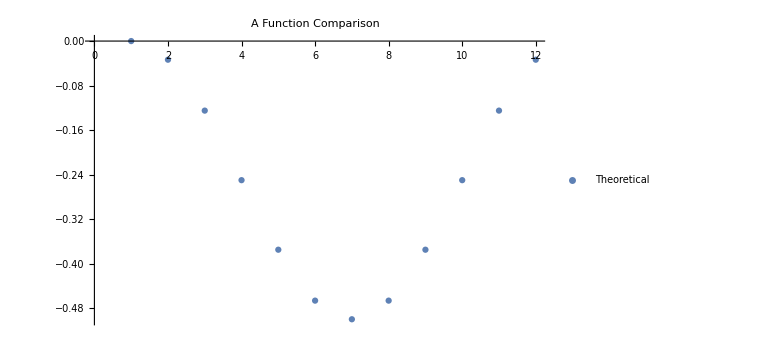

```mathematica
uu=1;
ListPlot[{(*FyfinBoostVal[[uu,10,;;]],*)BJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.0078],Thickness[0.0035]} ,{PointSize[0.0055],Thickness[0.0025]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

### A function (for check)

#### A From Jecco

```mathematica
ABoostJecco={{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678},{-1.,-0.9999999999998692,-1.000000000000125,-0.9999999999999668,-1.00000000000003,-0.9999999999999876,-1.0000000000000107,-0.9999999999999938,-1.000000000000005,-0.9999999999999982,-1.0000000000000047,-1.0000000000000002,-1.0000000000000029,-0.9999999999999992,-0.9999999999999989,-0.9999999999999977,-0.999999999999997,-0.999999999999998,-0.9999999999999983,-0.9999999999999972,-0.9999999999999999,-1.000000000000001,-1.0000000000000022,99.89999999999999,99.40406583756652,97.93870580479737,95.56900918765345,92.39638194269091,88.54917723410247,84.17174558169158,79.41343432288453,74.41883329066884,69.3201360619144,64.23199985032291,59.24885810990273,54.44433706292125,49.87226892735976,45.56876120560944,41.554834814495045,37.83924343115199,34.42119911704933,31.292833281221935,28.441306249008445,25.850539980483145,23.502588573094606,21.37868412846738,19.46000596402618,17.728223183694194,16.165857626307503,14.756508614147343,13.48497435447197,12.337298304052805,11.300762839228748,10.363847429194356,9.516164248462108,8.748380740186617,8.052135957797901,7.419955452129935,6.845167919684397,6.32182568028223,5.844630219422406,5.408863438095164,5.010324841071559,4.645274617030854,4.3103823841583235,4.002681265551088,3.7195268992553685,3.458560962706982,3.217678789521079,2.9950006698475278,2.788846448060668,2.5977130593007884,2.4202546765048956,2.2552651701561763,2.1016626128049922,1.9584755887017025,1.8248310951947322,1.6999438466782308,1.5831068137632927,1.4736828500414358,1.371097276412467,1.2748313086061593,1.1844162273945988,1.099428203238558,1.0194836978977002,0.9442353750180343,0.8733684600343534,0.8065974970261546,0.7436634565617921,0.6843311541679815,0.6283869439662869,0.5756366563126393,0.5259037520348832,0.47902766915612366,0.4348623408754146,0.39327486610553,0.3541443160840513,0.3173606625197533,0.2828238144446876,0.25044275244442654,0.2201347502604312,0.19182467492284697,0.1654443575986305,0.14093202824700285,0.11823180797611876,0.09729325370581032,0.07807095037216207,0.06052414647115989,0.04461642923945977,0.03031543621841281,0.017592600349628826,0.006422926112847264,-0.003215205455027422,-0.01134020472228573,-0.017967415995355597,-0.023109235959473496,-0.026775209130007874,-0.028972101197741466,-0.029703950943420678}};
```

#### Analytic expression for A

```mathematica
ABoostV=Table[1/ρofuValues[[i,j,k]]^2(1-b^3 ρofuValues[[i,j,k]]^3(1+u1Values[[j,k]]^2+u2Values[[j,k]]^2)),{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
ABoostfinV=Table[-1/uValues[[i]]^3+1/(uValues[[i]] ρofuValues[[i,j,k]]^2)(1-b^3 ρofuValues[[i,j,k]]^3(1+u1Values[[j,k]]^2+u2Values[[j,k]]^2)),{i,1,uInnerNodes},{j,1,xValues//Length},{k,1,yValues//Length}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Outer Nodes

```mathematica
yy=1;
ListPlot[{Transpose[{uValues[[uInnerNodes;;]],(ABoostV[[uInnerNodes;;,10,yy]])}],Transpose[{uValues[[uInnerNodes;;]],ABoostJecco[[yy,uInnerNodes;;]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0035],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes;;]],(ABoostV[[uInnerNodes;;,10,yy]])-ABoostJecco[[yy,uInnerNodes;;]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0035],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

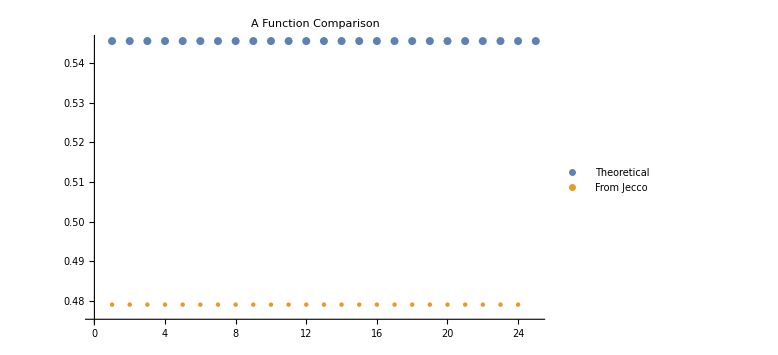

```mathematica
uu=uInnerNodes+70;
ListPlot[{ABoostV[[uu,1,;;]],ABoostJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0055],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

#### Inner Nodes

10 and 19

```mathematica
ABoostfinV[[2,10,;;]]//Length
```

25

```mathematica
yy=6;
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(ABoostfinV[[2;;uInnerNodes-1,10,yy]])}],Transpose[{uValues[[2;;uInnerNodes-1]],ABoostJecco[[yy,2;;uInnerNodes-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

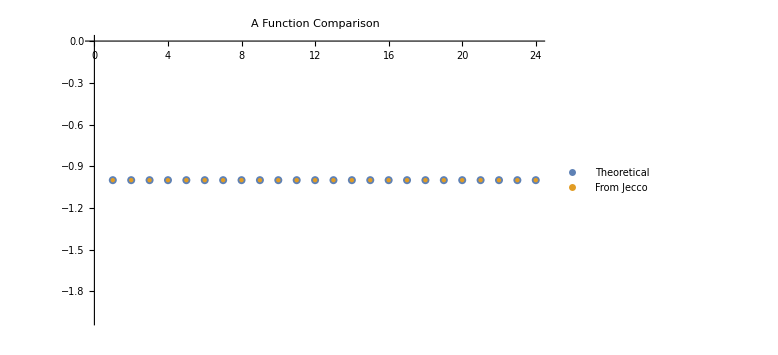

```mathematica
uu=uInnerNodes-1;
ListPlot[{ABoostfinV[[uu,10,;;-2]],ABoostJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0055],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

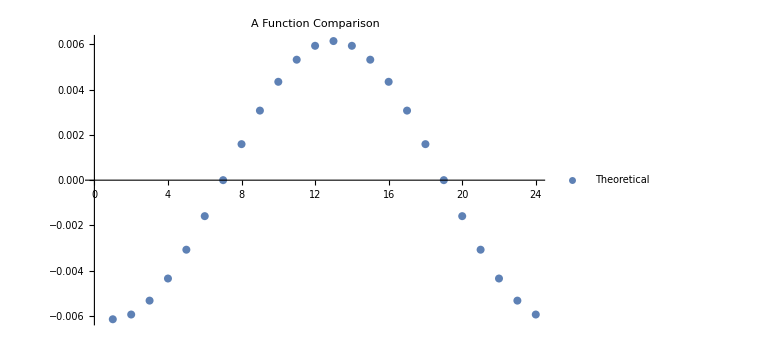

```mathematica
uu=uInnerNodes-1;
ListPlot[{ABoostfinV[[uu,10,;;-2]]-ABoostJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0055],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

### S function check

#### From Jecco

```mathematica
SJecco={{0.,-1.5577665510947556*^-10,-9.376129190650236*^-9,-9.6359675484476*^-8,-4.6822950567115334*^-7,-1.4787993358148713*^-6,-3.4938355350426707*^-6,-6.647017548914272*^-6,-0.000010624247148169125,-0.000014635019012719699,-0.00001764057116013263,9.999999812421837,9.559518348026867,8.470430989021327,7.18078786892217,6.006066411463396,5.061627730130705,4.348892781727719,3.831248811581934,3.4691872628019893,3.2314592099277433,3.0968338698918694,3.0532566134276014,3.0108851197542963,2.8936638376227193,2.7263263882187427,2.5377699674712546,2.352178017500836,2.18553205260829,2.0463470313319574,1.9380538863677617,1.8613162740072953,1.8156791804396661,1.8005487804370466,1.7856651090834965,1.7435744121142436,1.681044660301843,1.606882446200198,1.5296999421825843,1.4564992778069503,1.3922406986221445,1.340079275854971,1.3018622741683046,1.2786019615841357,1.2707981587029336,1.2630754592208915,1.2409801698689116,1.207416966141166,1.1663466756516137,1.121920722118615,1.0778574244441692,1.0371978034202598,1.0023877574598046,0.9755097125816282,0.9584139767057014,0.9525288176769107},{0.,-1.3560555706597486*^-10,-8.162039440809597*^-9,-8.38823094274373*^-8,-4.075994479857626*^-7,-1.2873107715268386*^-6,-3.0414123929884437*^-6,-5.786255949706132*^-6,-9.248395813885427*^-6,-0.00001273969237198585,-0.000015355937971633087,9.999999836715388,9.559518378460005,8.470431044756166,7.180787996290918,6.006066722969137,5.061628464252039,4.34889435384066,3.831251784252707,3.469192164300927,3.2314662240166694,3.0968425682889165,3.0532659588542717,3.0108951506739112,2.8936761061753113,2.7263429947683426,2.5377939033453103,2.3522133469386337,2.18558366925195,2.0464196972429667,1.9381504973120538,1.8614358389212553,1.8158155788797439,1.8006913913091878,1.7858141723910328,1.7437437596768697,1.6812508050018085,1.607145908759546,1.5300454793940812,1.456953946866169,1.3928286341177951,1.3408129521416463,1.3027323489179048,1.2795708353306632,1.2718033170830008,1.2641182269386793,1.2421408037528474,1.2087908494944442,1.168053973894993,1.1241135477337105,1.080719170721623,1.0409240288501929,1.0071331137322537,0.98129196061121,0.9650053175323867,0.959430842379131},{0.,-8.762436858309983*^-11,-5.274072394715748*^-9,-5.420228844401081*^-8,-2.633784118183178*^-7,-8.318177924933334*^-7,-1.9652443418845273*^-6,-3.7388092994977797*^-6,-5.975786286065636*^-6,-8.231528866239701*^-6,-9.921848802429471*^-6,9.999999894498279,9.559518450845273,8.470431177316474,7.180788299201619,6.006067463689219,5.061630209481877,4.348898089949335,3.8312588456878367,3.469203801961091,3.2314828701636187,3.0968632051178466,3.053288128177587,3.010918943284091,2.893705195521789,2.726382344155131,2.5378505650368557,2.352296871593518,2.185705504521508,2.046590907330923,1.938377708408837,1.8617165827601234,1.8161354945366956,1.8010257455978917,1.7861635132293336,1.7441401491932385,1.6817323075953838,1.607759421722763,1.530846912831562,1.4580034049956068,1.3941783523956786,1.342488001709793,1.3047091942989808,1.281764747264711,1.2740766345448717,1.2664736746470415,1.244752515443766,1.2118620047295314,1.17183318824794,1.1289029389153689,1.086862848357586,1.0487590965832505,1.016884478946576,0.9929141334042335,0.9780361395551904,0.9729912788142687},{0.,-3.8944163767510274*^-11,-2.3440320533548275*^-9,-2.408989307902115*^-8,-1.1705676742259812*^-7,-3.69693759431228*^-7,-8.734249764515371*^-7,-1.6616316619977022*^-6,-2.6557482663642998*^-6,-3.658159850389036*^-6,-4.409278465402805*^-6,9.999999953115232,9.559518524273978,8.470431311778746,7.180788606415505,6.006068214741227,5.0616319783267745,4.3489018743658905,3.831265993035996,3.4692155714178727,3.2314996918575782,3.096884048117788,3.0533105145103203,3.010942963851197,2.8937345449058105,2.7264220010735354,2.537907575459005,2.3523807247712822,2.185827486723866,2.0467618003856014,1.9386037999767338,1.8619951925222824,1.8164523918683195,1.8013567267865356,1.7865090967389832,1.7445314721829714,1.6822059969278793,1.6083599648537819,1.5316263171852988,1.4590160751608379,1.3954695482454111,1.3440766151965937,1.306569955384791,1.2838191463399968,1.2762014451680992,1.2686710794770772,1.247174937762835,1.2146824141011738,1.175254114295802,1.133155797386835,1.0921894544883115,1.0553665179572698,1.024870493996043,1.0021789204359552,0.9882236687463545,0.9835173250240252},{0.,-9.736040938433316*^-12,-5.860079828043007*^-10,-6.0224700457465134*^-9,-2.926411573193719*^-8,-9.242268056408417*^-8,-2.1835200598395467*^-7,-4.153925768059887*^-7,-6.6389788451076*^-7,-9.144656206693844*^-7,-1.102211612408491*^-6,9.99999998828003,9.55951856832349,8.4704313924358,7.1807887906676875,6.006068665054234,5.061633038380854,4.348904140785012,3.8312702697416574,3.469222607093912,3.2315097388298755,3.096896489031102,3.0533238735646506,3.0109572947624614,2.8937520423224865,2.7264456135601907,2.5379414569321703,2.3524304343589644,2.1858995784950643,2.0468624531236657,1.938736506959591,1.8621582394439038,1.8166374680415214,1.8015498881844936,1.786710631002204,1.7447591691074884,1.6824805737824706,1.6087061986006244,1.5320725651119185,1.459591138536638,1.396196251989891,1.3449628750748925,1.307600237905014,1.2849508228221151,1.2773697767630026,1.2698770855170989,1.2484969849817755,1.216207083595993,1.1770785776451145,1.1353847136770732,1.0949234109347792,1.058680291782812,1.028783460305227,1.0066266241132253,0.9930455273381232,0.9884741017971493},{0.,-6.990162897359796*^-13,-4.2073478592063785*^-11,-4.3239372559781485*^-10,-2.1010649774397995*^-9,-6.6356100068049465*^-9,-1.5676745949825597*^-8,-2.9823039057083705*^-8,-4.766366441123901*^-8,-6.565177089406568*^-8,-7.912955786840048*^-8,9.999999999158607,9.55951858195038,8.470431417385722,7.180788847655038,6.006068804296004,5.061633366026068,4.3489048408820405,3.8312715898230496,3.4692247769857096,3.231512835078317,3.0969003209560393,3.053327987475537,3.0109617070612376,2.893757426177776,2.726452871055331,2.537951853963624,2.3524456559293623,2.1859215963414895,2.046893105145465,1.9387768043040838,1.8622076269680434,1.8166934336582479,1.8016082636636481,1.7867714996322375,1.7448278124978773,1.6825630922852524,1.6088097962110814,1.5322053455824287,1.4597611366930805,1.3964095817061453,1.3452212875538225,1.3078989291216512,1.285277648651026,1.277706730099982,1.270224424457619,1.2488761660654282,1.2166413547723332,1.1775932387514805,1.136005869452414,1.0956746505433668,1.0595772522670812,1.0298272786481992,1.0077985338228213,0.9943054935355404,0.9897655156399942},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,10.,9.559518583004328,8.470431419315346,7.18078885206205,6.0060688150623145,5.061633391353467,4.348904894980638,3.8312716917824576,3.4692249444969026,3.231513073990266,3.0969006165355757,3.053328304768024,3.010962047325119,2.8937578412062854,2.7264534301445953,2.537952654125474,2.3524468258692015,2.1859232859809534,2.0468954532685957,1.9387798859810768,1.8622113982024073,1.8166977028961246,1.8016127151445624,1.7867761395456119,1.7448330393348663,1.6825693640821322,1.608817649854385,1.5322153789214366,1.4597739341711566,1.3964255773313947,1.3452405896536088,1.3079211686467123,1.2853019311357938,1.2777317462675963,1.2702501920831413,1.2489042319516064,1.216673377304683,1.177630992935847,1.1360511449203063,1.0957290110192515,1.0596416665764627,1.029901703032821,1.007881595263225,0.9943944442682753,0.9898565603840815},{0.,-6.990162897359796*^-13,-4.2073478592063785*^-11,-4.3239372559781485*^-10,-2.1010649774397995*^-9,-6.6356100068049465*^-9,-1.5676745949825597*^-8,-2.9823039057083705*^-8,-4.766366441123901*^-8,-6.565177089406568*^-8,-7.912955786840048*^-8,9.999999999158607,9.55951858195038,8.470431417385722,7.180788847655038,6.006068804296004,5.061633366026068,4.3489048408820405,3.8312715898230496,3.4692247769857096,3.231512835078317,3.0969003209560393,3.053327987475537,3.0109617070612376,2.893757426177776,2.726452871055331,2.537951853963624,2.3524456559293623,2.1859215963414895,2.046893105145465,1.9387768043040838,1.8622076269680434,1.8166934336582479,1.8016082636636481,1.7867714996322375,1.7448278124978773,1.6825630922852524,1.6088097962110814,1.5322053455824287,1.4597611366930805,1.3964095817061453,1.3452212875538225,1.3078989291216512,1.285277648651026,1.277706730099982,1.270224424457619,1.2488761660654282,1.2166413547723332,1.1775932387514805,1.136005869452414,1.0956746505433668,1.0595772522670812,1.0298272786481992,1.0077985338228213,0.9943054935355404,0.9897655156399942},{0.,-9.736040938433316*^-12,-5.860079828043007*^-10,-6.0224700457465134*^-9,-2.926411573193719*^-8,-9.242268056408417*^-8,-2.1835200598395467*^-7,-4.153925768059887*^-7,-6.6389788451076*^-7,-9.144656206693844*^-7,-1.102211612408491*^-6,9.99999998828003,9.55951856832349,8.4704313924358,7.1807887906676875,6.006068665054234,5.061633038380854,4.348904140785012,3.8312702697416574,3.469222607093912,3.2315097388298755,3.096896489031102,3.0533238735646506,3.0109572947624614,2.8937520423224865,2.7264456135601907,2.5379414569321703,2.3524304343589644,2.1858995784950643,2.0468624531236657,1.938736506959591,1.8621582394439038,1.8166374680415214,1.8015498881844936,1.786710631002204,1.7447591691074884,1.6824805737824706,1.6087061986006244,1.5320725651119185,1.459591138536638,1.396196251989891,1.3449628750748925,1.307600237905014,1.2849508228221151,1.2773697767630026,1.2698770855170989,1.2484969849817755,1.216207083595993,1.1770785776451145,1.1353847136770732,1.0949234109347792,1.058680291782812,1.028783460305227,1.0066266241132253,0.9930455273381232,0.9884741017971493},{0.,-3.8944163767510274*^-11,-2.3440320533548275*^-9,-2.408989307902115*^-8,-1.1705676742259812*^-7,-3.69693759431228*^-7,-8.734249764515371*^-7,-1.6616316619977022*^-6,-2.6557482663642998*^-6,-3.658159850389036*^-6,-4.409278465402805*^-6,9.999999953115232,9.559518524273978,8.470431311778746,7.180788606415505,6.006068214741227,5.0616319783267745,4.3489018743658905,3.831265993035996,3.4692155714178727,3.2314996918575782,3.096884048117788,3.0533105145103203,3.010942963851197,2.8937345449058105,2.7264220010735354,2.537907575459005,2.3523807247712822,2.185827486723866,2.0467618003856014,1.9386037999767338,1.8619951925222824,1.8164523918683195,1.8013567267865356,1.7865090967389832,1.7445314721829714,1.6822059969278793,1.6083599648537819,1.5316263171852988,1.4590160751608379,1.3954695482454111,1.3440766151965937,1.306569955384791,1.2838191463399968,1.2762014451680992,1.2686710794770772,1.247174937762835,1.2146824141011738,1.175254114295802,1.133155797386835,1.0921894544883115,1.0553665179572698,1.024870493996043,1.0021789204359552,0.9882236687463545,0.9835173250240252},{0.,-8.762436858309983*^-11,-5.274072394715748*^-9,-5.420228844401081*^-8,-2.633784118183178*^-7,-8.318177924933334*^-7,-1.9652443418845273*^-6,-3.7388092994977797*^-6,-5.975786286065636*^-6,-8.231528866239701*^-6,-9.921848802429471*^-6,9.999999894498279,9.559518450845273,8.470431177316474,7.180788299201619,6.006067463689219,5.061630209481877,4.348898089949335,3.8312588456878367,3.469203801961091,3.2314828701636187,3.0968632051178466,3.053288128177587,3.010918943284091,2.893705195521789,2.726382344155131,2.5378505650368557,2.352296871593518,2.185705504521508,2.046590907330923,1.938377708408837,1.8617165827601234,1.8161354945366956,1.8010257455978917,1.7861635132293336,1.7441401491932385,1.6817323075953838,1.607759421722763,1.530846912831562,1.4580034049956068,1.3941783523956786,1.342488001709793,1.3047091942989808,1.281764747264711,1.2740766345448717,1.2664736746470415,1.244752515443766,1.2118620047295314,1.17183318824794,1.1289029389153689,1.086862848357586,1.0487590965832505,1.016884478946576,0.9929141334042335,0.9780361395551904,0.9729912788142687},{0.,-1.3560555706597486*^-10,-8.162039440809597*^-9,-8.38823094274373*^-8,-4.075994479857626*^-7,-1.2873107715268386*^-6,-3.0414123929884437*^-6,-5.786255949706132*^-6,-9.248395813885427*^-6,-0.00001273969237198585,-0.000015355937971633087,9.999999836715388,9.559518378460005,8.470431044756166,7.180787996290918,6.006066722969137,5.061628464252039,4.34889435384066,3.831251784252707,3.469192164300927,3.2314662240166694,3.0968425682889165,3.0532659588542717,3.0108951506739112,2.8936761061753113,2.7263429947683426,2.5377939033453103,2.3522133469386337,2.18558366925195,2.0464196972429667,1.9381504973120538,1.8614358389212553,1.8158155788797439,1.8006913913091878,1.7858141723910328,1.7437437596768697,1.6812508050018085,1.607145908759546,1.5300454793940812,1.456953946866169,1.3928286341177951,1.3408129521416463,1.3027323489179048,1.2795708353306632,1.2718033170830008,1.2641182269386793,1.2421408037528474,1.2087908494944442,1.168053973894993,1.1241135477337105,1.080719170721623,1.0409240288501929,1.0071331137322537,0.98129196061121,0.9650053175323867,0.959430842379131},{0.,-1.5577665510947556*^-10,-9.376129190650236*^-9,-9.6359675484476*^-8,-4.6822950567115334*^-7,-1.4787993358148713*^-6,-3.4938355350426707*^-6,-6.647017548914272*^-6,-0.000010624247148169125,-0.000014635019012719699,-0.00001764057116013263,9.999999812421837,9.559518348026867,8.470430989021327,7.18078786892217,6.006066411463396,5.061627730130705,4.348892781727719,3.831248811581934,3.4691872628019893,3.2314592099277433,3.0968338698918694,3.0532566134276014,3.0108851197542963,2.8936638376227193,2.7263263882187427,2.5377699674712546,2.352178017500836,2.18553205260829,2.0463470313319574,1.9380538863677617,1.8613162740072953,1.8156791804396661,1.8005487804370466,1.7856651090834965,1.7435744121142436,1.681044660301843,1.606882446200198,1.5296999421825843,1.4564992778069503,1.3922406986221445,1.340079275854971,1.3018622741683046,1.2786019615841357,1.2707981587029336,1.2630754592208915,1.2409801698689116,1.207416966141166,1.1663466756516137,1.121920722118615,1.0778574244441692,1.0371978034202598,1.0023877574598046,0.9755097125816282,0.9584139767057014,0.9525288176769107},{0.,-1.3560555706597486*^-10,-8.162039440809597*^-9,-8.38823094274373*^-8,-4.075994479857626*^-7,-1.2873107715268386*^-6,-3.0414123929884437*^-6,-5.786255949706132*^-6,-9.248395813885427*^-6,-0.00001273969237198585,-0.000015355937971633087,9.999999836715388,9.559518378460005,8.470431044756166,7.180787996290918,6.006066722969137,5.061628464252039,4.34889435384066,3.831251784252707,3.469192164300927,3.2314662240166694,3.0968425682889165,3.0532659588542717,3.0108951506739112,2.8936761061753113,2.7263429947683426,2.5377939033453103,2.3522133469386337,2.18558366925195,2.0464196972429667,1.9381504973120538,1.8614358389212553,1.8158155788797439,1.8006913913091878,1.7858141723910328,1.7437437596768697,1.6812508050018085,1.607145908759546,1.5300454793940812,1.456953946866169,1.3928286341177951,1.3408129521416463,1.3027323489179048,1.2795708353306632,1.2718033170830008,1.2641182269386793,1.2421408037528474,1.2087908494944442,1.168053973894993,1.1241135477337105,1.080719170721623,1.0409240288501929,1.0071331137322537,0.98129196061121,0.9650053175323867,0.959430842379131},{0.,-8.762436858309983*^-11,-5.274072394715748*^-9,-5.420228844401081*^-8,-2.633784118183178*^-7,-8.318177924933334*^-7,-1.9652443418845273*^-6,-3.7388092994977797*^-6,-5.975786286065636*^-6,-8.231528866239701*^-6,-9.921848802429471*^-6,9.999999894498279,9.559518450845273,8.470431177316474,7.180788299201619,6.006067463689219,5.061630209481877,4.348898089949335,3.8312588456878367,3.469203801961091,3.2314828701636187,3.0968632051178466,3.053288128177587,3.010918943284091,2.893705195521789,2.726382344155131,2.5378505650368557,2.352296871593518,2.185705504521508,2.046590907330923,1.938377708408837,1.8617165827601234,1.8161354945366956,1.8010257455978917,1.7861635132293336,1.7441401491932385,1.6817323075953838,1.607759421722763,1.530846912831562,1.4580034049956068,1.3941783523956786,1.342488001709793,1.3047091942989808,1.281764747264711,1.2740766345448717,1.2664736746470415,1.244752515443766,1.2118620047295314,1.17183318824794,1.1289029389153689,1.086862848357586,1.0487590965832505,1.016884478946576,0.9929141334042335,0.9780361395551904,0.9729912788142687},{0.,-3.8944163767510274*^-11,-2.3440320533548275*^-9,-2.408989307902115*^-8,-1.1705676742259812*^-7,-3.69693759431228*^-7,-8.734249764515371*^-7,-1.6616316619977022*^-6,-2.6557482663642998*^-6,-3.658159850389036*^-6,-4.409278465402805*^-6,9.999999953115232,9.559518524273978,8.470431311778746,7.180788606415505,6.006068214741227,5.0616319783267745,4.3489018743658905,3.831265993035996,3.4692155714178727,3.2314996918575782,3.096884048117788,3.0533105145103203,3.010942963851197,2.8937345449058105,2.7264220010735354,2.537907575459005,2.3523807247712822,2.185827486723866,2.0467618003856014,1.9386037999767338,1.8619951925222824,1.8164523918683195,1.8013567267865356,1.7865090967389832,1.7445314721829714,1.6822059969278793,1.6083599648537819,1.5316263171852988,1.4590160751608379,1.3954695482454111,1.3440766151965937,1.306569955384791,1.2838191463399968,1.2762014451680992,1.2686710794770772,1.247174937762835,1.2146824141011738,1.175254114295802,1.133155797386835,1.0921894544883115,1.0553665179572698,1.024870493996043,1.0021789204359552,0.9882236687463545,0.9835173250240252},{0.,-9.736040938433316*^-12,-5.860079828043007*^-10,-6.0224700457465134*^-9,-2.926411573193719*^-8,-9.242268056408417*^-8,-2.1835200598395467*^-7,-4.153925768059887*^-7,-6.6389788451076*^-7,-9.144656206693844*^-7,-1.102211612408491*^-6,9.99999998828003,9.55951856832349,8.4704313924358,7.1807887906676875,6.006068665054234,5.061633038380854,4.348904140785012,3.8312702697416574,3.469222607093912,3.2315097388298755,3.096896489031102,3.0533238735646506,3.0109572947624614,2.8937520423224865,2.7264456135601907,2.5379414569321703,2.3524304343589644,2.1858995784950643,2.0468624531236657,1.938736506959591,1.8621582394439038,1.8166374680415214,1.8015498881844936,1.786710631002204,1.7447591691074884,1.6824805737824706,1.6087061986006244,1.5320725651119185,1.459591138536638,1.396196251989891,1.3449628750748925,1.307600237905014,1.2849508228221151,1.2773697767630026,1.2698770855170989,1.2484969849817755,1.216207083595993,1.1770785776451145,1.1353847136770732,1.0949234109347792,1.058680291782812,1.028783460305227,1.0066266241132253,0.9930455273381232,0.9884741017971493},{0.,-6.990162897359796*^-13,-4.2073478592063785*^-11,-4.3239372559781485*^-10,-2.1010649774397995*^-9,-6.6356100068049465*^-9,-1.5676745949825597*^-8,-2.9823039057083705*^-8,-4.766366441123901*^-8,-6.565177089406568*^-8,-7.912955786840048*^-8,9.999999999158607,9.55951858195038,8.470431417385722,7.180788847655038,6.006068804296004,5.061633366026068,4.3489048408820405,3.8312715898230496,3.4692247769857096,3.231512835078317,3.0969003209560393,3.053327987475537,3.0109617070612376,2.893757426177776,2.726452871055331,2.537951853963624,2.3524456559293623,2.1859215963414895,2.046893105145465,1.9387768043040838,1.8622076269680434,1.8166934336582479,1.8016082636636481,1.7867714996322375,1.7448278124978773,1.6825630922852524,1.6088097962110814,1.5322053455824287,1.4597611366930805,1.3964095817061453,1.3452212875538225,1.3078989291216512,1.285277648651026,1.277706730099982,1.270224424457619,1.2488761660654282,1.2166413547723332,1.1775932387514805,1.136005869452414,1.0956746505433668,1.0595772522670812,1.0298272786481992,1.0077985338228213,0.9943054935355404,0.9897655156399942},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,10.,9.559518583004328,8.470431419315346,7.18078885206205,6.0060688150623145,5.061633391353467,4.348904894980638,3.8312716917824576,3.4692249444969026,3.231513073990266,3.0969006165355757,3.053328304768024,3.010962047325119,2.8937578412062854,2.7264534301445953,2.537952654125474,2.3524468258692015,2.1859232859809534,2.0468954532685957,1.9387798859810768,1.8622113982024073,1.8166977028961246,1.8016127151445624,1.7867761395456119,1.7448330393348663,1.6825693640821322,1.608817649854385,1.5322153789214366,1.4597739341711566,1.3964255773313947,1.3452405896536088,1.3079211686467123,1.2853019311357938,1.2777317462675963,1.2702501920831413,1.2489042319516064,1.216673377304683,1.177630992935847,1.1360511449203063,1.0957290110192515,1.0596416665764627,1.029901703032821,1.007881595263225,0.9943944442682753,0.9898565603840815},{0.,-6.990162897359796*^-13,-4.2073478592063785*^-11,-4.3239372559781485*^-10,-2.1010649774397995*^-9,-6.6356100068049465*^-9,-1.5676745949825597*^-8,-2.9823039057083705*^-8,-4.766366441123901*^-8,-6.565177089406568*^-8,-7.912955786840048*^-8,9.999999999158607,9.55951858195038,8.470431417385722,7.180788847655038,6.006068804296004,5.061633366026068,4.3489048408820405,3.8312715898230496,3.4692247769857096,3.231512835078317,3.0969003209560393,3.053327987475537,3.0109617070612376,2.893757426177776,2.726452871055331,2.537951853963624,2.3524456559293623,2.1859215963414895,2.046893105145465,1.9387768043040838,1.8622076269680434,1.8166934336582479,1.8016082636636481,1.7867714996322375,1.7448278124978773,1.6825630922852524,1.6088097962110814,1.5322053455824287,1.4597611366930805,1.3964095817061453,1.3452212875538225,1.3078989291216512,1.285277648651026,1.277706730099982,1.270224424457619,1.2488761660654282,1.2166413547723332,1.1775932387514805,1.136005869452414,1.0956746505433668,1.0595772522670812,1.0298272786481992,1.0077985338228213,0.9943054935355404,0.9897655156399942},{0.,-9.736040938433316*^-12,-5.860079828043007*^-10,-6.0224700457465134*^-9,-2.926411573193719*^-8,-9.242268056408417*^-8,-2.1835200598395467*^-7,-4.153925768059887*^-7,-6.6389788451076*^-7,-9.144656206693844*^-7,-1.102211612408491*^-6,9.99999998828003,9.55951856832349,8.4704313924358,7.1807887906676875,6.006068665054234,5.061633038380854,4.348904140785012,3.8312702697416574,3.469222607093912,3.2315097388298755,3.096896489031102,3.0533238735646506,3.0109572947624614,2.8937520423224865,2.7264456135601907,2.5379414569321703,2.3524304343589644,2.1858995784950643,2.0468624531236657,1.938736506959591,1.8621582394439038,1.8166374680415214,1.8015498881844936,1.786710631002204,1.7447591691074884,1.6824805737824706,1.6087061986006244,1.5320725651119185,1.459591138536638,1.396196251989891,1.3449628750748925,1.307600237905014,1.2849508228221151,1.2773697767630026,1.2698770855170989,1.2484969849817755,1.216207083595993,1.1770785776451145,1.1353847136770732,1.0949234109347792,1.058680291782812,1.028783460305227,1.0066266241132253,0.9930455273381232,0.9884741017971493},{0.,-3.8944163767510274*^-11,-2.3440320533548275*^-9,-2.408989307902115*^-8,-1.1705676742259812*^-7,-3.69693759431228*^-7,-8.734249764515371*^-7,-1.6616316619977022*^-6,-2.6557482663642998*^-6,-3.658159850389036*^-6,-4.409278465402805*^-6,9.999999953115232,9.559518524273978,8.470431311778746,7.180788606415505,6.006068214741227,5.0616319783267745,4.3489018743658905,3.831265993035996,3.4692155714178727,3.2314996918575782,3.096884048117788,3.0533105145103203,3.010942963851197,2.8937345449058105,2.7264220010735354,2.537907575459005,2.3523807247712822,2.185827486723866,2.0467618003856014,1.9386037999767338,1.8619951925222824,1.8164523918683195,1.8013567267865356,1.7865090967389832,1.7445314721829714,1.6822059969278793,1.6083599648537819,1.5316263171852988,1.4590160751608379,1.3954695482454111,1.3440766151965937,1.306569955384791,1.2838191463399968,1.2762014451680992,1.2686710794770772,1.247174937762835,1.2146824141011738,1.175254114295802,1.133155797386835,1.0921894544883115,1.0553665179572698,1.024870493996043,1.0021789204359552,0.9882236687463545,0.9835173250240252},{0.,-8.762436858309983*^-11,-5.274072394715748*^-9,-5.420228844401081*^-8,-2.633784118183178*^-7,-8.318177924933334*^-7,-1.9652443418845273*^-6,-3.7388092994977797*^-6,-5.975786286065636*^-6,-8.231528866239701*^-6,-9.921848802429471*^-6,9.999999894498279,9.559518450845273,8.470431177316474,7.180788299201619,6.006067463689219,5.061630209481877,4.348898089949335,3.8312588456878367,3.469203801961091,3.2314828701636187,3.0968632051178466,3.053288128177587,3.010918943284091,2.893705195521789,2.726382344155131,2.5378505650368557,2.352296871593518,2.185705504521508,2.046590907330923,1.938377708408837,1.8617165827601234,1.8161354945366956,1.8010257455978917,1.7861635132293336,1.7441401491932385,1.6817323075953838,1.607759421722763,1.530846912831562,1.4580034049956068,1.3941783523956786,1.342488001709793,1.3047091942989808,1.281764747264711,1.2740766345448717,1.2664736746470415,1.244752515443766,1.2118620047295314,1.17183318824794,1.1289029389153689,1.086862848357586,1.0487590965832505,1.016884478946576,0.9929141334042335,0.9780361395551904,0.9729912788142687},{0.,-1.3560555706597486*^-10,-8.162039440809597*^-9,-8.38823094274373*^-8,-4.075994479857626*^-7,-1.2873107715268386*^-6,-3.0414123929884437*^-6,-5.786255949706132*^-6,-9.248395813885427*^-6,-0.00001273969237198585,-0.000015355937971633087,9.999999836715388,9.559518378460005,8.470431044756166,7.180787996290918,6.006066722969137,5.061628464252039,4.34889435384066,3.831251784252707,3.469192164300927,3.2314662240166694,3.0968425682889165,3.0532659588542717,3.0108951506739112,2.8936761061753113,2.7263429947683426,2.5377939033453103,2.3522133469386337,2.18558366925195,2.0464196972429667,1.9381504973120538,1.8614358389212553,1.8158155788797439,1.8006913913091878,1.7858141723910328,1.7437437596768697,1.6812508050018085,1.607145908759546,1.5300454793940812,1.456953946866169,1.3928286341177951,1.3408129521416463,1.3027323489179048,1.2795708353306632,1.2718033170830008,1.2641182269386793,1.2421408037528474,1.2087908494944442,1.168053973894993,1.1241135477337105,1.080719170721623,1.0409240288501929,1.0071331137322537,0.98129196061121,0.9650053175323867,0.959430842379131}};
```

#### Analytic S

```mathematica
SBoostValues=Table[(1/ρofuValues[[i,j,k]]^2(1+b^3 ρofuValues[[i,j,k]]^3(u1Values[[j,k]]^2+u2Values[[j,k]]^2))^(1/2))^(1/2),{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
SBoostValues//Dimensions
```

{104,13,13}

```mathematica
SfinBoostValues=Table[(-1/uValues[[i]]^3+1/uValues[[i]]^2(1/ρofuValues[[i,j,k]]^2(1+b^3 ρofuValues[[i,j,k]]^3(u1Values[[j,k]]^2+u2Values[[j,k]]^2))^(1/2))^(1/2)),{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Inner Nodes

```mathematica
yy=4;
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(SfinBoostValues[[2;;uInnerNodes-1,1,yy]])}],Transpose[{uValues[[2;;uInnerNodes-1]],SJecco[[yy,2;;uInnerNodes-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],SfinBoostValues[[2;;uInnerNodes-1,1,yy]]-SJecco[[yy,2;;uInnerNodes-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

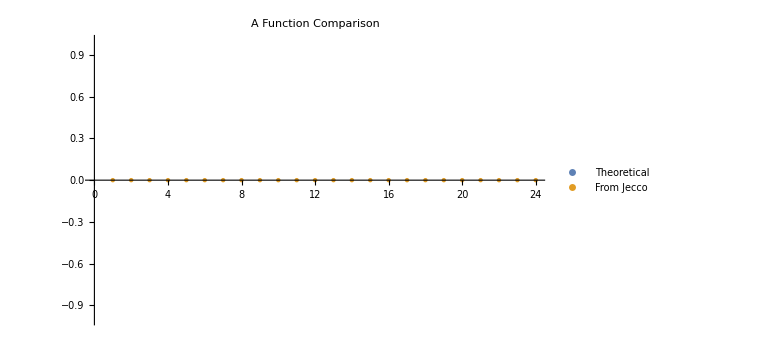

```mathematica
uu=1;
ListPlot[{SfinBoostValues[[uu,1,;;]],SJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0055],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

```mathematica
Interpolation[Transpose[{yValues,SJecco[[;;,uu]]}]]
```

InterpolatingFunction[…]

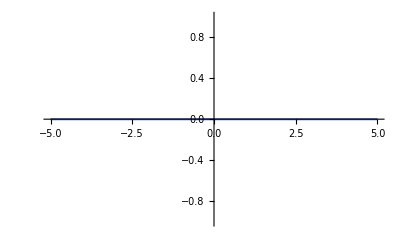

```mathematica
Plot[D[%[y],y]/.y->yy,{yy,yMin,yMax}]
```

#### Outer Nodes

```mathematica
uValues[[uInnerNodes;;]]//Dimensions
SJecco[[yy,uInnerNodes;;]]//Dimensions
```

{45}

{45}

```mathematica
yy=1;
end=-1;
ListPlot[{Transpose[{uValues[[uInnerNodes;;]],((*SJeccoOld[[yy,uInnerNodes;;]]*)SBoostValues[[uInnerNodes;;,1,yy]])}],Transpose[{uValues[[uInnerNodes;;]],SJecco[[yy,uInnerNodes;;]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.006],Thickness[0.0005],Opacity[0.750]} ,{PointSize[0.0035],Thickness[0.0005],Opacity[0.750]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes;;]],(SBoostValues[[uInnerNodes;;,1,yy]]-SJecco[[yy,uInnerNodes;;]])}]},PlotRange->All,PlotLabels->{"Error"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0035],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes;;]],(SBoostValues[[uInnerNodes;;,1,yy]]-SJecco[[yy,uInnerNodes;;]])/SBoostValues[[uInnerNodes;;,1,yy]]}]},PlotRange->All,PlotLabels->{"Error"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0035],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

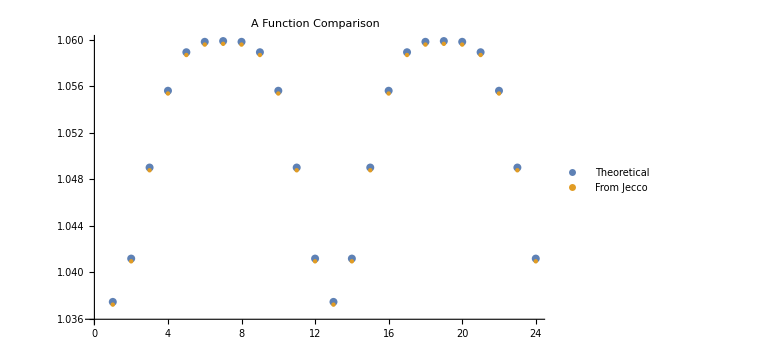

```mathematica
uu=uInnerNodes+40;
ListPlot[{SBoostValues[[uu,1,;;]],SJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0055],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

```mathematica
SBoostValues[[uInnerNodes+1,1,1]]
SJecco[[1,uInnerNodes+1]]//FullForm
```

9.95658062691863726133497022767943139545787854710767256381055139

9.9513

```mathematica
SfinBoostValues[[uInnerNodes-1,1,1]]
SJecco[[1,uInnerNodes-1]]//FullForm
```

-0.00001764057116013264131798550057647379879206928376087524721

-0.0000176406

### Fx function

#### From Jecco

```mathematica
FxJecco={{-1.4142135623731151,-1.4142135653104688,-1.4142137391711087,-1.4142153793488963,-1.414222391400704,-1.4142414469541214,-1.414279443176976,-1.4143389012191716,-1.4144138988825534,-1.4144895301185327,-1.4145462066055698,-0.14145672749445887,-0.14798000902168815,-0.16702741366457277,-0.19707670372136865,-0.23573586365896815,-0.2799382457081977,-0.32618136086538935,-0.3707766212489748,-0.4101113010941694,-0.4409163406854757,-0.4605554431896248,-0.46730256048641994,-0.474059855077878,-0.49384588732783713,-0.5252392755606351,-0.5659818803838474,-0.6131160176194351,-0.66313634037359,-0.7121532126310751,-0.7560983964581344,-0.7910270465076396,-0.8135481797453491,-0.8213331141979191,-0.829154961264895,-0.8522065036980367,-0.889257115413265,-0.9382801712500758,-0.9964509608388138,-1.060096756814876,-1.1246208525824604,-1.184512479840109,-1.2336526693386693,-1.2661253959121297,-1.2775026107600111,-1.2890153054189388,-1.323436536084291,-1.380403281637028,-1.4592309248537076,-1.5586566482083002,-1.6761987729196193,-1.8068784604960617,-1.941214195380939,-2.063225090115053,-2.15099183427934,-2.18329031964556},{-1.342953984239484,-1.342953986841973,-1.3429541408824477,-1.3429555940795845,-1.3429618067513955,-1.3429786899176537,-1.3430123542995227,-1.3430650332621783,-1.3431314793419051,-1.3431984858906056,-1.3432486986484458,-0.13432673641029336,-0.1405208772070449,-0.15860683939320158,-0.1871378985982182,-0.22384022172644957,-0.2657981882753354,-0.3096821514136969,-0.35198787318412617,-0.38928802217195996,-0.4184877416322689,-0.4370971004709285,-0.4434892123449854,-0.449890304471387,-0.46862935551307283,-0.49834838712128876,-0.5368909424769664,-0.5814360446079632,-0.628649115566012,-0.6748462073304262,-0.7161974471990024,-0.7490148996934716,-0.7701496275315952,-0.7774505023983804,-0.7847834316600283,-0.806378736234054,-0.8410383449868662,-0.8867950682540789,-0.9409239327015311,-0.9999194265579219,-1.059460626948673,-1.1144620978743185,-1.1593840417544174,-1.1889612084219867,-1.199302821193078,-1.2097561974981659,-1.2409404073220884,-1.2923113280477678,-1.3628758322470438,-1.4509525241511592,-1.55362870164081,-1.6657731717186581,-1.7786653864289101,-1.8789485166370175,-1.9496878855840176,-1.9754159880054298},{-1.1456439237389016,-1.14564392552355,-1.1456440311559686,-1.1456450276772396,-1.1456492879711946,-1.1456608654078722,-1.1456839500629574,-1.1457200727543362,-1.145765634320712,-1.1458115785841165,-1.1458460068170064,-0.11458588045002988,-0.11986892666212824,-0.1352937424938348,-0.15962338998166356,-0.19091265151476744,-0.22666615312880123,-0.2640350111551636,-0.3000263931748603,-0.331724393944462,-0.356510896468161,-0.37229310215406003,-0.37771127883687294,-0.3831355436801812,-0.3990057850450085,-0.4241447980858089,-0.4566855658181683,-0.4941941598077488,-0.5338139252953646,-0.5724260326341917,-0.6068405332341575,-0.6340430177751977,-0.6515061796869939,-0.6575281529670985,-0.6635709518212551,-0.6813333098243358,-0.7097317664867444,-0.747001783616805,-0.7907386392742622,-0.8379322803336405,-0.8850138792028153,-0.9279761494606197,-0.9626626505244755,-0.985293403786413,-0.9931662324227482,-1.0011027427674584,-1.0246487580446215,-1.0630005953695174,-1.114758511582969,-1.1777851831175963,-1.2489329657188168,-1.3236446663858068,-1.3955783965706192,-1.456657277419234,-1.4981288777348862,-1.5128803293922872},{-0.8660254037844786,-0.8660254046838533,-0.8660254579175551,-0.8660259601167192,-0.866028107095788,-0.8660339415072962,-0.8660455747328634,-0.8660637777506169,-0.8660867362426147,-0.8661098864662521,-0.8661272333052317,-0.0866133681323079,-0.09060590589667872,-0.10226193209864193,-0.1206435532288957,-0.14427469729799217,-0.17126069143770856,-0.1994393607130682,-0.2265449135493659,-0.25038135665620953,-0.26899222386749283,-0.280827441173723,-0.2848876978095857,-0.2889509712649774,-0.3008299556018802,-0.31961612342784274,-0.34387126055358647,-0.37172941939465126,-0.40102155569042647,-0.42941672169798234,-0.454582164028459,-0.47436862090842147,-0.4870182260826917,-0.49137030828724,-0.49573215943317617,-0.5085220910614636,-0.5288690692829353,-0.5553702139132164,-0.586153378834559,-0.6189533639037437,-0.6512091879308796,-0.6802065835153657,-0.7032965205161724,-0.7181996859435055,-0.723353552967446,-0.728532854870501,-0.7438014281776046,-0.7683518390527361,-0.8008352390414045,-0.8393438969742163,-0.8813777690163767,-0.923821943434725,-0.9630078620182335,-0.9949696662749546,-1.0159818381576111,-1.0233214246427655},{-0.5590169943749422,-0.5590169946652142,-0.5590170118463246,-0.5590171739303248,-0.5590178668624939,-0.5590197498887146,-0.5590235043841043,-0.5590293790253886,-0.5590367880790639,-0.5590442586494608,-0.5590498562337366,-0.055905193686818976,-0.05848167547680566,-0.06600300258749377,-0.07786192653167427,-0.09310202601577479,-0.11049493714044115,-0.1286394838947494,-0.14607099392490977,-0.1613773352006245,-0.17331014820873514,-0.1808891876511234,-0.18348746853207734,-0.18608670139955572,-0.19367969121745995,-0.20566846310898,-0.22110830198867107,-0.23877948702444107,-0.2572775954571322,-0.27511650818715483,-0.29084023262867553,-0.30314032251553247,-0.3109727050153905,-0.3136615566435489,-0.31635335176008345,-0.32422801051991934,-0.33669686404827864,-0.35282207060563764,-0.371376403457451,-0.3909199923420468,-0.40989284043909224,-0.4267252690012091,-0.43996808331034454,-0.44843677656981135,-0.4513507086901311,-0.4542712805390496,-0.4628353362140438,-0.47645880117181655,-0.4941966015066522,-0.5147821740615095,-0.5366812579364157,-0.5581664503910597,-0.5774254044080808,-0.5927149475075253,-0.6025587502272404,-0.6059581019332286},{-0.26734733253871534,-0.2673473325759111,-0.26734733477758477,-0.26734735554790323,-0.26734744434380975,-0.2673476856430477,-0.26734816675415957,-0.26734891952936823,-0.2673498688941074,-0.26735082610776534,-0.26735154331124394,-0.02673518098925427,-0.02796713010554782,-0.031563258821678854,-0.03723250971735984,-0.044516214138062546,-0.05282504605542622,-0.06148699467529121,-0.06980087803294552,-0.07709325210643345,-0.08277215771127629,-0.08637582558227967,-0.08761062094667288,-0.08884553138660438,-0.09245098349774085,-0.09813711415579073,-0.10544668300975941,-0.11379147129802053,-0.12249883774513895,-0.13086486105457168,-0.13821033417639114,-0.14393578602724372,-0.14757143786333143,-0.14881764567156613,-0.15006421501298675,-0.15370505897785944,-0.15945122906901926,-0.16684593653509308,-0.17529950706438407,-0.18413438670149399,-0.19263723924400855,-0.20011507442189208,-0.20595200064091723,-0.2096623497770961,-0.21093487643571077,-0.2122081417790477,-0.21592909867233895,-0.22180833864019284,-0.22938663434293122,-0.23806780356677404,-0.24716168366574892,-0.25593515347285506,-0.2636690418688485,-0.269718013971268,-0.2735688623130396,-0.27489061530124737},{6.123233995736632*^-17,6.123233995736727*^-17,6.123233995737223*^-17,6.123233995737418*^-17,6.123233995737459*^-17,6.123233995737467*^-17,6.123233995737474*^-17,6.123233995737469*^-17,6.123233995737464*^-17,6.123233995737461*^-17,6.123233995737461*^-17,6.1232339957374535*^-18,8.886007326172573*^-18,1.619564633552003*^-17,7.928761663619178*^-18,-6.466633909596145*^-19,-2.1526685257843015*^-17,-2.1812053701925606*^-17,-1.823750699356513*^-17,-1.1261604730432759*^-17,-4.0902571568499394*^-18,8.192508146753185*^-20,1.5951702390264282*^-18,2.521140624517892*^-18,4.741634486235721*^-18,7.674353192129108*^-18,1.1173383115002842*^-17,1.4807538225231973*^-17,1.9608951313901604*^-17,2.468759542018361*^-17,2.908588382556467*^-17,3.260923810310488*^-17,3.4820782344128554*^-17,3.5573285441684994*^-17,3.631000160017195*^-17,3.8472669769780706*^-17,4.212886968232564*^-17,4.6641314831340055*^-17,5.1015539218018963*^-17,5.494491348114239*^-17,5.848296231572819*^-17,6.151093313629844*^-17,6.379033789772109*^-17,6.523712027977536*^-17,6.572562542927865*^-17,6.620623425523776*^-17,6.7609459707691*^-17,6.973968487513072*^-17,7.237768554941987*^-17,7.538511701191047*^-17,7.841904870586994*^-17,8.138709056043227*^-17,8.396347553985632*^-17,8.590333719868614*^-17,8.712588042664201*^-17,8.754095741218069*^-17},{0.26734733253870596,0.26734733257590343,0.26734733477758504,0.2673473555479035,0.26734744434381,0.26734768564304806,0.2673481667541599,0.26734891952936823,0.26734986889410733,0.2673508261077652,0.2673515433112438,0.026735180989253732,0.02796713010554726,0.03156325882167824,0.03723250971735917,0.04451621413806175,0.052825046055425345,0.06148699467529052,0.06980087803294498,0.077093252106433,0.08277215771127593,0.08637582558227933,0.08761062094667381,0.08884553138660525,0.09245098349774161,0.09813711415579131,0.10544668300975976,0.11379147129802063,0.12249883774513881,0.13086486105457135,0.13821033417639064,0.14393578602724305,0.14757143786333068,0.14881764567156558,0.15006421501298614,0.15370505897785866,0.1594512290690183,0.1668459365350919,0.1752995070643827,0.1841343867014924,0.19263723924400683,0.2001150744218903,0.20595200064091537,0.2096623497770942,0.21093487643571707,0.21220814177905367,0.21592909867234394,0.2218083386401964,0.22938663434293302,0.23806780356677398,0.24716168366574714,0.2559351534728518,0.2636690418688441,0.2697180139712628,0.27356886231303407,0.2748906153012417},{0.5590169943749483,0.5590169946652205,0.5590170118463298,0.5590171739303258,0.5590178668624951,0.5590197498887157,0.5590235043841059,0.5590293790253891,0.5590367880790639,0.5590442586494607,0.5590498562337364,0.055905193686819656,0.058481675476806314,0.06600300258749435,0.0778619265316748,0.09310202601577533,0.11049493714044159,0.12863948389474944,0.1460709939249094,0.16137733520062386,0.17331014820873433,0.18088918765112252,0.18348746853207473,0.18608670139955313,0.19367969121745748,0.2056684631089776,0.22110830198866877,0.23877948702443877,0.2572775954571298,0.27511650818715233,0.2908402326286729,0.3031403225155297,0.31097270501538754,0.3136615566435431,0.3163533517600777,0.3242280105199137,0.3366968640482731,0.3528220706056322,0.3713764034574456,0.39091999234204133,0.4098928404390867,0.42672526900120344,0.4399680833103387,0.44843677656980535,0.45135070869012817,0.4542712805390465,0.4628353362140404,0.47645880117181244,0.4941966015066471,0.5147821740615034,0.5366812579364084,0.5581664503910512,0.5774254044080711,0.592714947507515,0.6025587502272296,0.6059581019332178},{0.8660254037844562,0.8660254046838307,0.8660254579175373,0.8660259601167153,0.8660281070957857,0.8660339415072953,0.8660455747328626,0.8660637777506169,0.8660867362426147,0.866109886466252,0.8661272333052316,0.08661336813230996,0.09060590589668086,0.10226193209864427,0.12064355322889832,0.14427469729799525,0.17126069143771191,0.1994393607130707,0.2265449135493677,0.2503813566562109,0.26899222386749394,0.28082744117372405,0.28488769780958184,0.2889509712649737,0.3008299556018772,0.3196161234278406,0.34387126055358525,0.37172941939465104,0.4010215556904271,0.4294167216979836,0.45458216402846086,0.4743686209084237,0.487018226082694,0.49137030828722505,0.4957321594331617,0.5085220910614504,0.5288690692829239,0.5553702139132071,0.5861533788345515,0.6189533639037379,0.6512091879308756,0.680206583515363,0.7032965205161706,0.7181996859435041,0.7233535529674495,0.7285328548705043,0.7438014281776077,0.7683518390527392,0.8008352390414074,0.8393438969742192,0.88137776901638,0.9238219434347286,0.9630078620182368,0.9949696662749576,1.0159818381576138,1.023321424642768},{1.1456439237389549,1.145643925523599,1.1456440311559892,1.1456450276772405,1.1456492879711977,1.1456608654078744,1.1456839500629596,1.145720072754337,1.145765634320712,1.1458115785841163,1.145846006817006,0.1145858804500325,0.11986892666213084,0.1352937424938374,0.1596233899816663,0.19091265151477052,0.22666615312880445,0.26403501115516553,0.3000263931748612,0.3317243939444623,0.3565108964681608,0.37229310215405964,0.37771127883687433,0.3831355436801825,0.3990057850450097,0.42414479808581,0.4566855658181694,0.49419415980774983,0.5338139252953656,0.5724260326341927,0.6068405332341585,0.6340430177751988,0.6515061796869952,0.6575281529671081,0.6635709518212646,0.6813333098243449,0.7097317664867531,0.7470017836168131,0.7907386392742699,0.8379322803336479,0.8850138792028223,0.9279761494606265,0.9626626505244825,0.9852934037864202,0.9931662324227747,1.0011027427674846,1.0246487580446466,1.0630005953695403,1.1147585115829894,1.177785183117614,1.2489329657188324,1.3236446663858208,1.3955783965706317,1.4566572774192452,1.498128877734897,1.5128803293922979},{1.342953984239484,1.342953986841973,1.3429541408824477,1.3429555940795845,1.3429618067513955,1.3429786899176537,1.3430123542995227,1.3430650332621783,1.3431314793419051,1.3431984858906056,1.3432486986484458,0.13432673641029202,0.14052087720704354,0.15860683939320014,0.18713789859821664,0.22384022172644782,0.26579818827533347,0.3096821514136954,0.3519878731841251,0.38928802217195924,0.4184877416322685,0.4370971004709283,0.4434892123449741,0.4498903044713761,0.4686293555130628,0.49834838712127993,0.5368909424769589,0.5814360446079567,0.6286491155660064,0.6748462073304214,0.7161974471989978,0.749014899693467,0.7701496275315904,0.7774505023983814,0.7847834316600291,0.8063787362340537,0.8410383449868639,0.886795068254074,0.9409239327015232,0.999919426557911,1.0594606269486595,1.1144620978743025,1.1593840417543995,1.1889612084219676,1.1993028211930887,1.2097561974981754,1.2409404073220953,1.29231132804777,1.36287583224704,1.4509525241511492,1.553628701640793,1.665773171718635,1.7786653864288817,1.8789485166369848,1.949687885583982,1.9754159880053934},{1.4142135623731151,1.4142135653104688,1.4142137391711087,1.4142153793488963,1.414222391400704,1.4142414469541214,1.414279443176976,1.4143389012191716,1.4144138988825534,1.4144895301185327,1.4145462066055698,0.14145672749446112,0.14798000902169037,0.16702741366457502,0.197076703721371,0.23573586365897084,0.27993824570820064,0.3261813608653915,0.37077662124897626,0.41011130109417027,0.44091634068547625,0.4605554431896252,0.46730256048640506,0.4740598550778635,0.493845887327824,0.5252392755606239,0.5659818803838383,0.613116017619428,0.6631363403735847,0.712153212631071,0.7560983964581309,0.7910270465076364,0.813548179745346,0.82133311419792,0.8291549612648956,0.8522065036980367,0.8892571154132639,0.9382801712500733,0.9964509608388098,1.060096756814871,1.124620852582454,1.1845124798401014,1.2336526693386611,1.266125395912121,1.2775026107599619,1.2890153054188909,1.3234365360842466,1.3804032816369887,1.459230924853675,1.5586566482082747,1.6761987729196006,1.8068784604960493,1.9412141953809314,2.0632250901150493,2.150991834279339,2.1832903196455593},{1.342953984239464,1.3429539868419615,1.3429541408824657,1.342955594079587,1.3429618067513978,1.342978689917652,1.3430123542995216,1.3430650332621779,1.3431314793419054,1.343198485890606,1.3432486986484462,0.1343267364102936,0.14052087720704506,0.15860683939320158,0.187137898598218,0.22384022172644918,0.26579818827533475,0.30968215141369604,0.3519878731841251,0.3892880221719587,0.41848774163226743,0.437097100470927,0.4434892123449868,0.44989030447138817,0.4686293555130735,0.49834838712128876,0.5368909424769657,0.5814360446079616,0.6286491155660098,0.6748462073304236,0.716197447198999,0.7490148996934679,0.7701496275315912,0.7774505023983809,0.7847834316600286,0.8063787362340534,0.8410383449868644,0.8867950682540754,0.9409239327015257,0.9999194265579147,1.059460626948664,1.1144620978743076,1.1593840417544055,1.1889612084219743,1.1993028211930963,1.2097561974981834,1.240940407322104,1.29231132804778,1.3628758322470518,1.450952524151163,1.553628701640809,1.6657731717186528,1.7786653864289013,1.878948516637006,1.9496878855840043,1.975415988005416},{1.1456439237389016,1.14564392552355,1.1456440311559686,1.1456450276772396,1.1456492879711946,1.1456608654078722,1.1456839500629574,1.1457200727543362,1.145765634320712,1.1458115785841165,1.1458460068170064,0.11458588045002832,0.1198689266621267,0.13529374249383322,0.15962338998166192,0.19091265151476564,0.2266661531287993,0.2640350111551622,0.30002639317485935,0.3317243939444614,0.35651089646816064,0.37229310215405986,0.37771127883687833,0.38313554368018626,0.39900578504501283,0.4241447980858122,0.4566855658181707,0.4941941598077504,0.5338139252953655,0.572426032634192,0.6068405332341573,0.6340430177751971,0.6515061796869932,0.6575281529671169,0.663570951821273,0.6813333098243526,0.7097317664867598,0.7470017836168189,0.7907386392742746,0.8379322803336515,0.8850138792028253,0.9279761494606291,0.9626626505244851,0.9852934037864227,0.9931662324227688,1.001102742767479,1.0246487580446422,1.0630005953695378,1.1147585115829894,1.1777851831176167,1.2489329657188375,1.323644666385828,1.3955783965706403,1.4566572774192552,1.498128877734908,1.5128803293923092},{0.8660254037844755,0.8660254046838507,0.8660254579175534,0.8660259601167153,0.8660281070957854,0.8660339415072941,0.8660455747328618,0.8660637777506169,0.8660867362426153,0.8661098864662529,0.8661272333052324,0.08661336813230815,0.09060590589667897,0.10226193209864215,0.12064355322889585,0.14427469729799228,0.17126069143770858,0.19943936071306795,0.22654491354936543,0.2503813566562089,0.2689922238674921,0.2808274411737222,0.28488769780957157,0.28895097126496366,0.3008299556018679,0.3196161234278325,0.3438712605535784,0.3717294193946454,0.4010215556904225,0.42941672169797995,0.45458216402845786,0.4743686209084212,0.48701822608269185,0.49137030828722067,0.49573215943315746,0.5085220910614466,0.5288690692829208,0.5553702139132045,0.5861533788345497,0.6189533639037369,0.6512091879308751,0.680206583515363,0.703296520516171,0.7181996859435047,0.723353552967453,0.7285328548705075,0.7438014281776096,0.7683518390527393,0.8008352390414054,0.8393438969742147,0.881377769016373,0.9238219434347194,0.963007862018226,0.9949696662749458,1.0159818381576011,1.023321424642755},{0.5590169943749375,0.5590169946652102,0.559017011846325,0.5590171739303271,0.5590178668624968,0.5590197498887174,0.5590235043841071,0.5590293790253897,0.5590367880790644,0.5590442586494613,0.5590498562337369,0.05590519368681851,0.05848167547680518,0.06600300258749327,0.07786192653167374,0.09310202601577419,0.11049493714044047,0.12863948389474894,0.14607099392490944,0.16137733520062425,0.17331014820873497,0.18088918765112327,0.18348746853207906,0.18608670139955732,0.19367969121746134,0.20566846310898104,0.22110830198867176,0.2387794870244414,0.2572775954571322,0.27511650818715455,0.290840232628675,0.3031403225155317,0.31097270501538954,0.3136615566435441,0.3163533517600787,0.32422801051991484,0.33669686404827437,0.35282207060563353,0.37137640345744705,0.390919992342043,0.40989284043908847,0.4267252690012054,0.43996808331034093,0.4484367765698078,0.4513507086901381,0.45427128053905613,0.46283533621404915,0.47645880117182,0.4941966015066533,0.514782174061508,0.5366812579364116,0.5581664503910533,0.5774254044080724,0.5927149475075157,0.6025587502272302,0.6059581019332183},{0.2673473325387069,0.26734733257590343,0.267347334777582,0.26734735554790373,0.2673474443438102,0.2673476856430477,0.2673481667541595,0.26734891952936823,0.2673498688941075,0.26735082610776545,0.26735154331124406,0.026735180989253714,0.02796713010554726,0.03156325882167829,0.03723250971735929,0.044516214138061935,0.052825046055425616,0.06148699467529091,0.06980087803294548,0.07709325210643359,0.08277215771127656,0.08637582558227999,0.08761062094667257,0.0888455313866041,0.09245098349774065,0.09813711415579063,0.10544668300975937,0.1137914712980205,0.12249883774513891,0.13086486105457162,0.1382103341763911,0.14393578602724363,0.14757143786333135,0.14881764567156558,0.15006421501298622,0.1537050589778589,0.15945122906901876,0.16684593653509258,0.17529950706438363,0.1841343867014936,0.1926372392440082,0.20011507442189175,0.20595200064091695,0.20966234977709589,0.21093487643571393,0.2122081417790507,0.21592909867234136,0.2218083386401944,0.2293866343429318,0.23806780356677354,0.24716168366574753,0.25593515347285295,0.2636690418688458,0.2697180139712649,0.27356886231303623,0.27489061530124387},{7.273661547324814*^-16,7.273661547324902*^-16,7.273661547325323*^-16,7.273661547325402*^-16,7.273661547325446*^-16,7.273661547325455*^-16,7.273661547325465*^-16,7.273661547325454*^-16,7.273661547325446*^-16,7.273661547325443*^-16,7.273661547325443*^-16,7.273661547325505*^-17,7.856874457044726*^-17,9.483781728087312*^-17,1.0069464688159812*^-16,1.102632270429249*^-16,1.1007741439952279*^-16,1.3136032234153946*^-16,1.5562948703231156*^-16,1.8075011203413778*^-16,2.0204594097487632*^-16,2.151781645500938*^-16,2.1976099338943889*^-16,2.237565281828232*^-16,2.3493711330742493*^-16,2.519947493676782*^-16,2.7363943494471293*^-16,2.9797011720596316*^-16,3.2434231168614846*^-16,3.50118434486877*^-16,3.7266399089458394*^-16,3.903140343119863*^-16,4.0148703565785007*^-16,4.0530961538515896*^-16,4.091164174793787*^-16,4.202406764122495*^-16,4.380240986001314*^-16,4.606850773023282*^-16,4.857590263156427*^-16,5.112624442369318*^-16,5.355010525244133*^-16,5.566789624071427*^-16,5.730871201876514*^-16,5.834966630511169*^-16,5.870556904088861*^-16,5.906068303002622*^-16,6.009729434112216*^-16,6.172324286271337*^-16,6.380215704017467*^-16,6.617316889410222*^-16,6.863427411709575*^-16,7.100142864660768*^-16,7.307431862385734*^-16,7.468138029620543*^-16,7.570003754850107*^-16,7.604864091575398*^-16},{-0.26734733253871074,-0.2673473325759074,-0.26734733477758504,-0.2673473555479023,-0.2673474443438089,-0.2673476856430466,-0.2673481667541584,-0.26734891952936746,-0.2673498688941068,-0.2673508261077648,-0.2673515433112434,-0.026735180989253846,-0.02796713010554738,-0.031563258821678354,-0.03723250971735924,-0.04451621413806181,-0.052825046055425366,-0.06148699467529044,-0.0698008780329448,-0.07709325210643272,-0.08277215771127557,-0.08637582558227894,-0.08761062094667381,-0.08884553138660525,-0.09245098349774161,-0.09813711415579131,-0.10544668300975976,-0.11379147129802063,-0.12249883774513881,-0.13086486105457135,-0.13821033417639064,-0.14393578602724305,-0.14757143786333068,-0.14881764567156558,-0.15006421501298614,-0.15370505897785866,-0.1594512290690183,-0.1668459365350919,-0.1752995070643827,-0.1841343867014924,-0.19263723924400683,-0.2001150744218903,-0.20595200064091537,-0.2096623497770942,-0.21093487643571707,-0.21220814177905367,-0.21592909867234394,-0.2218083386401964,-0.22938663434293302,-0.23806780356677398,-0.24716168366574714,-0.2559351534728518,-0.2636690418688441,-0.2697180139712628,-0.27356886231303407,-0.2748906153012417},{-0.5590169943749488,-0.5590169946652198,-0.5590170118463258,-0.5590171739303254,-0.5590178668624943,-0.5590197498887157,-0.5590235043841053,-0.5590293790253882,-0.559036788079063,-0.5590442586494598,-0.5590498562337356,-0.055905193686818414,-0.058481675476805106,-0.06600300258749323,-0.07786192653167372,-0.0931020260157742,-0.11049493714044058,-0.12863948389474908,-0.14607099392490963,-0.1613773352006245,-0.17331014820873522,-0.18088918765112355,-0.1834874685320849,-0.1860867013995629,-0.1936796912174663,-0.2056684631089852,-0.221108301988675,-0.23877948702444377,-0.25727759545713375,-0.2751165081871555,-0.29084023262867553,-0.30314032251553197,-0.31097270501538965,-0.31366155664354467,-0.3163533517600793,-0.32422801051991557,-0.3366968640482752,-0.3528220706056346,-0.3713764034574484,-0.39091999234204455,-0.40989284043909024,-0.42672526900120733,-0.4399680833103429,-0.44843677656980974,-0.4513507086901328,-0.45427128053905114,-0.46283533621404505,-0.47645880117181727,-0.4941966015066523,-0.514782174061509,-0.5366812579364145,-0.5581664503910579,-0.5774254044080785,-0.5927149475075228,-0.6025587502272377,-0.605958101933226},{-0.8660254037844786,-0.8660254046838533,-0.8660254579175551,-0.8660259601167192,-0.866028107095788,-0.8660339415072962,-0.8660455747328634,-0.8660637777506169,-0.8660867362426147,-0.8661098864662521,-0.8661272333052317,-0.0866133681323079,-0.09060590589667872,-0.10226193209864193,-0.1206435532288957,-0.14427469729799217,-0.17126069143770856,-0.1994393607130682,-0.2265449135493659,-0.25038135665620953,-0.26899222386749283,-0.280827441173723,-0.2848876978095857,-0.2889509712649774,-0.3008299556018802,-0.31961612342784274,-0.34387126055358647,-0.37172941939465126,-0.40102155569042647,-0.42941672169798234,-0.454582164028459,-0.47436862090842147,-0.4870182260826917,-0.49137030828724,-0.49573215943317617,-0.5085220910614636,-0.5288690692829353,-0.5553702139132164,-0.586153378834559,-0.6189533639037437,-0.6512091879308796,-0.6802065835153657,-0.7032965205161724,-0.7181996859435055,-0.723353552967446,-0.728532854870501,-0.7438014281776046,-0.7683518390527361,-0.8008352390414045,-0.8393438969742163,-0.8813777690163767,-0.923821943434725,-0.9630078620182335,-0.9949696662749546,-1.0159818381576111,-1.0233214246427655},{-1.1456439237389549,-1.145643925523599,-1.1456440311559892,-1.1456450276772405,-1.1456492879711977,-1.1456608654078744,-1.1456839500629596,-1.145720072754337,-1.145765634320712,-1.1458115785841163,-1.145846006817006,-0.11458588045003186,-0.11986892666213023,-0.1352937424938368,-0.15962338998166564,-0.19091265151476977,-0.22666615312880364,-0.26403501115516503,-0.3000263931748609,-0.3317243939444621,-0.3565108964681608,-0.3722931021540597,-0.3777112788368664,-0.3831355436801748,-0.39900578504500267,-0.42414479808580385,-0.4566855658181642,-0.4941941598077456,-0.5338139252953624,-0.5724260326341902,-0.6068405332341567,-0.6340430177751973,-0.6515061796869939,-0.6575281529670977,-0.6635709518212545,-0.6813333098243357,-0.7097317664867452,-0.747001783616807,-0.7907386392742656,-0.837932280333645,-0.8850138792028205,-0.9279761494606255,-0.962662650524482,-0.98529340378642,-0.9931662324227747,-1.0011027427674846,-1.0246487580446466,-1.0630005953695403,-1.1147585115829894,-1.177785183117614,-1.2489329657188324,-1.3236446663858208,-1.3955783965706317,-1.4566572774192452,-1.498128877734897,-1.5128803293922979},{-1.3429539842394624,-1.342953986841956,-1.3429541408824475,-1.3429555940795803,-1.3429618067513927,-1.342978689917649,-1.343012354299519,-1.343065033262177,-1.3431314793419045,-1.3431984858906052,-1.3432486986484453,-0.13432673641029594,-0.14052087720704742,-0.15860683939320402,-0.1871378985982206,-0.22384022172645215,-0.2657981882753379,-0.3096821514136979,-0.351987873184126,-0.389288022171959,-0.41848774163226743,-0.43709710047092687,-0.4434892123449817,-0.44989030447138323,-0.4686293555130689,-0.49834838712128465,-0.536890942476962,-0.5814360446079585,-0.6286491155660072,-0.6748462073304214,-0.7161974471989973,-0.7490148996934661,-0.7701496275315894,-0.777450502398391,-0.7847834316600383,-0.8063787362340616,-0.8410383449868701,-0.8867950682540783,-0.9409239327015255,-0.9999194265579114,-1.0594606269486582,-1.1144620978742998,-1.159384041754396,-1.1889612084219638,-1.1993028211931012,-1.2097561974981876,-1.2409404073221066,-1.29231132804778,-1.3628758322470484,-1.450952524151156,-1.5536287016407984,-1.6657731717186386,-1.7786653864288837,-1.8789485166369855,-1.949687885583982,-1.9754159880053932}};
```

#### Analytic

```mathematica
Fx[u_]:=b^3 Nρofu[u]u1 u0d;
```

```mathematica
Fxfin[u_]:=1/u b^3 Nρofu[u]u1 u0d;
```

```mathematica
FxBoostVal=Table[-b^3 ρofuValues[[i,j,k]]u1Values[[j,k]] u0Values[[j,k]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];
```

```mathematica
FxfinBoostVal=Table[-b^3 ρofuValues[[i,j,k]]/uValues[[i]] u1Values[[j,k]] u0Values[[j,k]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Outer Nodes

```mathematica
FxJecco[[yy,uInnerNodes;;-1]]//Length
uValues[[uInnerNodes;;-1]]//Length
```

168

96

```mathematica
yy=2;
ListPlot[{Transpose[{uValues[[uInnerNodes;;-1]],(FxBoostVal[[uInnerNodes;;-1,10,yy]])}],Transpose[{uValues[[uInnerNodes;;-1]],FxJecco[[yy,uInnerNodes;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"Fx Function Comparison"]
```

-Graphics-

```mathematica
(*ListPlot[{Transpose[{uValues[[uInnerNodes;;-1]],FxBoostVal[[uInnerNodes;;-1,1,1]]-FxJecco[[uInnerNodes;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]*)
```

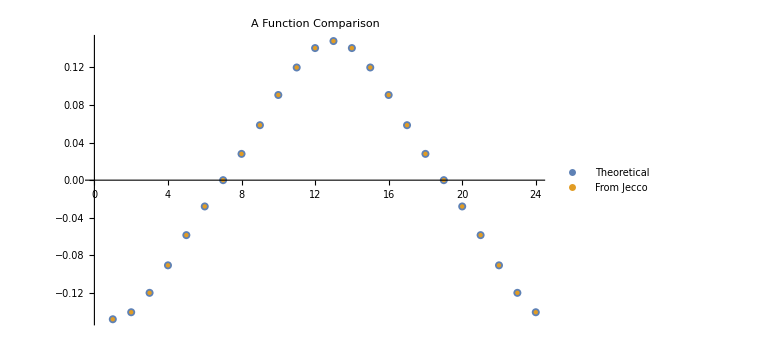

```mathematica
uu=uInnerNodes+1;
ListPlot[{FxBoostVal[[uu,10,;;]],FxJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0055],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

#### Inner Nodes

```mathematica
FxfinBoostVal[[2;;uInnerNodes-1,10,yy]]//Dimensions
```

{10}

```mathematica
yy=2;
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(FxfinBoostVal[[2;;uInnerNodes-1,1,yy]])}],Transpose[{uValues[[2;;uInnerNodes-1]],FxJecco[[yy,2;;uInnerNodes-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

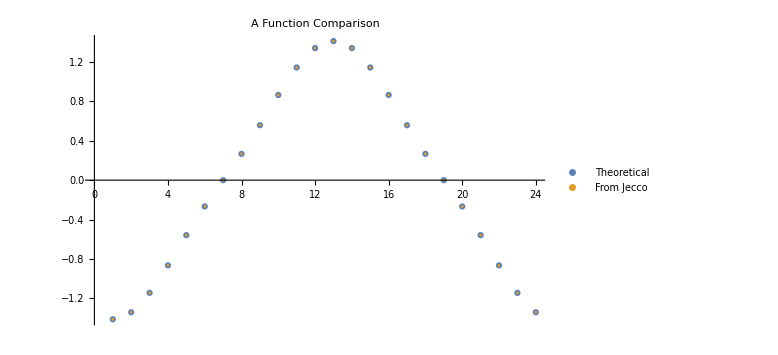

```mathematica
uu=2;
ListPlot[{FxfinBoostVal[[uu,10,;;]],FxJecco[[;;,uu]]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.0078],Thickness[0.0035]} ,{PointSize[0.0035],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

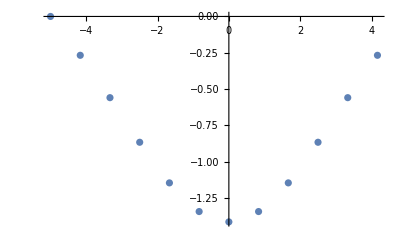

```mathematica
ListPlot[Transpose[{yValues,Function[y,-Cos[(π y)/10] √(1+Cos[(π y)/10]^2)]/@yValues}]]
```

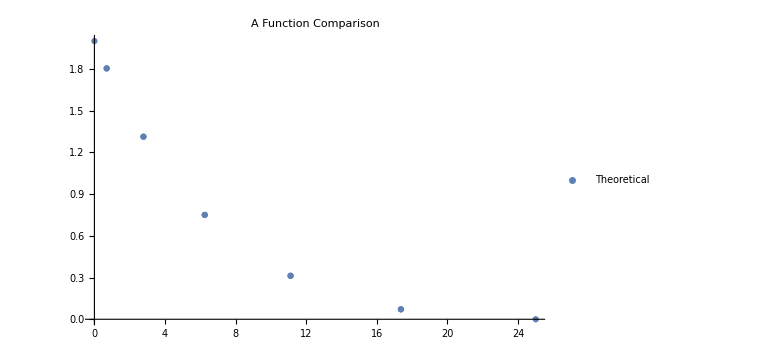

```mathematica
ListPlot[{Transpose[{yValues,Function[y,-Cos[(π y)/10] √(1+Cos[(π y)/10]^2)]/@yValues}],Transpose[{yValues,FxJecco[[;;,uu]]}]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.0078],Thickness[0.0035]} ,{PointSize[0.0035],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

### Fy function

#### From Jecco

```mathematica
Fy2Jecco={{-1.0300158665537665*^-32,2.9663965310241786*^-20,1.9488843748743606*^-19,2.3165743686943664*^-19,-3.7300219830853633*^-19,-1.3445219164837084*^-18,-1.427859488125606*^-18,-1.1929038154832622*^-18,-1.0420418459942745*^-18,-8.213507968284462*^-19,-5.435531378868819*^-19,-1.373583401722238*^-19,-1.2735427117898274*^-19,-8.375086463290556*^-20,6.253565887233941*^-19,2.4892195035496086*^-18,2.717814849963817*^-18,9.832455779647241*^-19,-1.1414667239176428*^-18,-3.64450666848813*^-18,-5.938407577348357*^-18,-7.381109875668771*^-18,-7.857630230925124*^-18,-7.819517934624101*^-18,-7.763327467284783*^-18,-7.750143036090923*^-18,-7.338608313048142*^-18,-7.57720510630711*^-18,-8.036589944799314*^-18,-8.608725726203347*^-18,-8.910103208008808*^-18,-9.095037839097307*^-18,-9.034059989282247*^-18,-9.008439861132929*^-18,-8.987798530553567*^-18,-8.886859964502558*^-18,-8.719112218989982*^-18,-8.355203337376883*^-18,-8.160445032195946*^-18,-7.88341450213602*^-18,-7.547100916622736*^-18,-7.389062421436336*^-18,-7.271661621472989*^-18,-7.206861058142768*^-18,-7.192952131711297*^-18,-7.200552939141803*^-18,-7.224773757522778*^-18,-7.240499324497947*^-18,-7.405330496280995*^-18,-7.238019389734727*^-18,-6.803696960755344*^-18,-6.7607204563287456*^-18,-6.805442914636884*^-18,-7.005703104886365*^-18,-7.182711682192877*^-18,-7.243851226474698*^-18},{1.726191206435707*^-15,0.00035654644853820724,0.00270471340145382,0.005838455329935383,0.010137381981444043,0.014910326048872047,0.019946129226001672,0.024745284973872197,0.02896094822734178,0.03223829696819754,0.03431117674585007,0.010508073111299181,0.010512606050627111,0.010575670458008047,0.010814056016215884,0.011342523991092656,0.01221346709740949,0.01339024076641694,0.014751918557911864,0.01611850826249213,0.01728758953582515,0.018075132273242697,0.01835294998071068,0.018357221800579738,0.018417452300358367,0.01865016301388726,0.019179841939587647,0.02007621664973573,0.021316271195029546,0.022779124701824634,0.02426903796392832,0.025557037772052368,0.026430495324019854,0.026739619545998718,0.026744201966789494,0.0268092704347777,0.0270637401025054,0.027652088303614653,0.028665045094146458,0.030090496068319657,0.03179855451011526,0.033561587159320186,0.03510175467746272,0.03615378202141083,0.03652747481815592,0.03653339776104432,0.036618034966897334,0.03695279747597643,0.037738934582429946,0.03911785062962341,0.041098057463400554,0.0435200492384227,0.04606845657019433,0.048331220515531625,0.04989519132285672,0.05045419343425816},{1.629355087065624*^-16,0.0006175562659890582,0.004684703224244898,0.010112508816778634,0.017558553363790103,0.025825884256613904,0.034549109543788606,0.042863468764460094,0.0501681764378739,0.055848184419638194,0.05944134525717987,0.018204639791001904,0.01821248049554592,0.018321560269344034,0.018733859188698108,0.019647788372616628,0.021153835059087453,0.023188508724634672,0.0255426540198582,0.027905102983388216,0.029926002618646343,0.031287321445408724,0.03176754041541819,0.03177486286677464,0.03187808793102991,0.03227678891059688,0.033183870578908564,0.034718058212026434,0.03683912980245157,0.03933967451178666,0.04188494045398162,0.04408416570010329,0.04557503659089267,0.04610257071981811,0.04611021774504885,0.046218748666615024,0.04664280365171312,0.04762195126020553,0.04930495788639298,0.05166885963548346,0.05449587850862043,0.05740847386299491,0.05994889774118792,0.06168220257016283,0.06229753164428921,0.06230678928799256,0.06243890908473125,0.06296023740077145,0.06418028502452701,0.06631103117274019,0.06935589478072623,0.07306139026875134,0.076942570296819,0.08037650494499025,0.08274457989666267,0.08359010372963885},{5.927357370359866*^-16,0.0007130920831470286,0.005409432791014796,0.011676931284929654,0.020275017240804525,0.029821859339848673,0.03989608199599073,0.04949978881065107,0.05793919535813454,0.06450334882205846,0.06865679883058248,0.021027377083093175,0.021036414026525542,0.021162129784436077,0.021637267658964583,0.022690361565716004,0.024425485149797598,0.026769290025044187,0.029480725665762368,0.03220141147493141,0.0345285611614528,0.03609609471908516,0.03664904466269672,0.036657380999811494,0.03677487150029527,0.037228477403676824,0.03825983938192381,0.04000289700650596,0.04241067255142372,0.045246709020243844,0.04813107135849117,0.050621545272670716,0.05230900129508892,0.052905937422675346,0.05291433728735222,0.053033475143845994,0.05349841207231898,0.05457008381884521,0.056408071783396345,0.05898313486047998,0.06205446424429091,0.0652105831782521,0.0679572176418542,0.06982808819503855,0.0704916617563487,0.07050100046672662,0.07063404916982688,0.07115736251090735,0.07237627736644942,0.07449199800620425,0.07749325096508525,0.08111592806293126,0.0848785472521787,0.08818163461481167,0.09044546076500914,0.09125098545198984},{-2.292507747422743*^-15,0.0006175554530811136,0.0046847092066072465,0.010112529449776112,0.017558806594210014,0.025827091019742756,0.034552929327677874,0.042872670620929094,0.05018542430033792,0.05587483041514017,0.05947562151759469,0.01821581200215197,0.01822362370686513,0.018332289502096907,0.01874295148413786,0.019653029411770072,0.021152294835778827,0.023177192062777147,0.025519361011049707,0.027869234978134403,0.029879026672649044,0.03123271346212708,0.03171021521271679,0.03171733365459417,0.03181763643727121,0.03220472117438886,0.03308430407445044,0.03456973470030505,0.03661991141293686,0.03903265243145672,0.04148450269170142,0.043600063304852464,0.045032771734640514,0.04553945737609251,0.04554638642342481,0.045644603248000765,0.04602746398196424,0.04690852010036672,0.04841651121875619,0.050524323917051875,0.05303219874309251,0.05560321765927769,0.057836075564837976,0.05935467667207429,0.05989286870479964,0.05990000156125432,0.06000147781693242,0.06039954665935782,0.06132314434264304,0.06291833588842531,0.06516812053146288,0.06786680818884308,0.07065242464704574,0.07308438107188635,0.07474423298705234,0.07533352261448613},{-9.488294923416851*^-17,0.00035654563562713485,0.0027047193838257047,0.005838475962912882,0.010137635211898567,0.014911532812190776,0.01994994901400146,0.024754486865039393,0.028978196256700964,0.03226494345321688,0.03434545392191658,0.010519245660142186,0.010523749602003397,0.010586400066842347,0.010823148850286153,0.011347766042046402,0.012211929006374153,0.013378928557331962,0.014728634206286352,0.016082655342885867,0.01724063648849573,0.01802055394831368,0.018295657151389633,0.01829972501056705,0.01835703396559937,0.01857813169825184,0.019080321049074204,0.019927959564968872,0.02109716009254613,0.022472279974951347,0.023868879474481314,0.02507333368120618,0.02588872898422251,0.02617704441908188,0.026180908458672447,0.026235657147684208,0.02644891120810405,0.02693912494105509,0.0277770194350124,0.028946394324855098,0.030335490348389768,0.031757390582441196,0.032990657720044815,0.033828618887081566,0.03412544184448985,0.03412922270184332,0.03418296553015276,0.034393455893327346,0.0348807364045376,0.03571998153133055,0.036899853189921006,0.03831046809612074,0.03976194015810977,0.04102572981253998,0.041886599167286154,0.0421919146741135},{9.93280536133047*^-34,-2.0062799763687828*^-21,-7.133011376121065*^-21,-1.6280958924801888*^-20,-3.7401779747697003*^-20,-1.0835021572247418*^-20,1.430427333783528*^-20,3.29299234483489*^-20,3.596911631903833*^-20,4.627277603212782*^-20,5.432088413872901*^-20,1.680476703956304*^-20,-3.1166340384115257*^-20,2.0217812074590082*^-19,1.088764041758556*^-18,-7.293026047231768*^-19,-4.363383184914857*^-18,-7.639442308059536*^-18,-1.1058408794565589*^-17,-1.4527609122393723*^-17,-1.7008057005680204*^-17,-1.824414120378073*^-17,-1.8633827518028853*^-17,-1.8621696484352728*^-17,-1.8709929213160132*^-17,-1.8991728304149275*^-17,-1.852018193577035*^-17,-1.7342096584797277*^-17,-1.6284451882263633*^-17,-1.5605382188234693*^-17,-1.481006323678915*^-17,-1.4205185541558742*^-17,-1.3754760703829428*^-17,-1.3598378884153323*^-17,-1.3594193929868823*^-17,-1.357210772655481*^-17,-1.3668223911561949*^-17,-1.3897899685828355*^-17,-1.3992546320841732*^-17,-1.3830855343004755*^-17,-1.3427140136262262*^-17,-1.3100497654211686*^-17,-1.2922509815275257*^-17,-1.2917390157072328*^-17,-1.292406189748166*^-17,-1.2921826312539082*^-17,-1.2895430284922883*^-17,-1.2827463594861111*^-17,-1.2752887094066003*^-17,-1.2541631090126215*^-17,-1.2197230936543302*^-17,-1.1944898641245374*^-17,-1.1639781187297382*^-17,-1.1330389128652609*^-17,-1.1115217350858694*^-17,-1.104263451448779*^-17},{1.538892470244315*^-16,-0.0003565456356270111,-0.002704719383825386,-0.005838475962912795,-0.010137635211898465,-0.014911532812190664,-0.019949949014001364,-0.024754486865039355,-0.028978196256700953,-0.03226494345321688,-0.03434545392191659,-0.010519245660142316,-0.010523749602003522,-0.010586400066842456,-0.010823148850286249,-0.011347766042046488,-0.01221192900637423,-0.013378928557332035,-0.01472863420628642,-0.01608265534288593,-0.01724063648849579,-0.018020553948313735,-0.01829565715139018,-0.018299725010567584,-0.018357033965599866,-0.018578131698252273,-0.019080321049074568,-0.01992795956496916,-0.02109716009254635,-0.022472279974951506,-0.023868879474481422,-0.025073333681206254,-0.025888728984222564,-0.0261770444190823,-0.026180908458672856,-0.026235657147684593,-0.026448911208104397,-0.026939124941055395,-0.027777019435012658,-0.0289463943248553,-0.030335490348389924,-0.031757390582441314,-0.032990657720044905,-0.03382861888708165,-0.03412544184448984,-0.034129222701843306,-0.03418296553015275,-0.03439345589332735,-0.034880736404537635,-0.03571998153133061,-0.03689985318992108,-0.03831046809612083,-0.03976194015810987,-0.041025729812540074,-0.041886599167286244,-0.04219191467411359},{2.055968564120661*^-16,-0.0006175554530828794,-0.004684709206607459,-0.010112529449776099,-0.017558806594209962,-0.025827091019742707,-0.03455292932767784,-0.042872670620929074,-0.05018542430033791,-0.05587483041514015,-0.05947562151759467,-0.018215812002151385,-0.018223623706864568,-0.018332289502096404,-0.01874295148413744,-0.019653029411769753,-0.021152294835778608,-0.023177192062777015,-0.02551936101104964,-0.02786923497813439,-0.02987902667264907,-0.03123271346212713,-0.03171021521271731,-0.03171733365459468,-0.03181763643727168,-0.03220472117438929,-0.033084304074450815,-0.03456973470030537,-0.03661991141293713,-0.03903265243145691,-0.04148450269170155,-0.04360006330485255,-0.04503277173464057,-0.04553945737609242,-0.04554638642342473,-0.04564460324800069,-0.046027463981964174,-0.04690852010036669,-0.04841651121875619,-0.05052432391705191,-0.05303219874309256,-0.055603217659277775,-0.05783607556483805,-0.05935467667207434,-0.059892868704799804,-0.059900001561254496,-0.06000147781693261,-0.060399546659358,-0.061323144342643215,-0.06291833588842546,-0.06516812053146301,-0.06786680818884316,-0.07065242464704581,-0.0730843810718864,-0.07474423298705238,-0.07533352261448618},{-5.927357370359866*^-16,-0.0007130920831470286,-0.005409432791014796,-0.011676931284929654,-0.020275017240804525,-0.029821859339848673,-0.03989608199599073,-0.04949978881065107,-0.05793919535813454,-0.06450334882205846,-0.06865679883058248,-0.021027377083092977,-0.02103641402652535,-0.021162129784435903,-0.021637267658964433,-0.022690361565715883,-0.024425485149797505,-0.026769290025044128,-0.029480725665762344,-0.03220141147493141,-0.034528561161452816,-0.03609609471908518,-0.03664904466269705,-0.03665738099981181,-0.03677487150029556,-0.03722847740367709,-0.03825983938192403,-0.040002897006506145,-0.042410672551423875,-0.04524670902024396,-0.048131071358491255,-0.05062154527267077,-0.05230900129508896,-0.05290593742267497,-0.05291433728735186,-0.053033475143845675,-0.053498412072318716,-0.05457008381884502,-0.05640807178339622,-0.05898313486047992,-0.0620544642442909,-0.06521058317825211,-0.06795721764185422,-0.06982808819503858,-0.07049166175634924,-0.07050100046672715,-0.07063404916982736,-0.07115736251090779,-0.07237627736644979,-0.07449199800620454,-0.07749325096508547,-0.08111592806293141,-0.08487854725217878,-0.08818163461481171,-0.09044546076500917,-0.09125098545198987},{-1.629355087065624*^-16,-0.0006175562659890582,-0.004684703224244898,-0.010112508816778634,-0.017558553363790103,-0.025825884256613904,-0.034549109543788606,-0.042863468764460094,-0.0501681764378739,-0.055848184419638194,-0.05944134525717987,-0.018204639791002206,-0.018212480495546215,-0.018321560269344304,-0.018733859188698337,-0.019647788372616812,-0.021153835059087592,-0.023188508724634765,-0.02554265401985825,-0.02790510298338823,-0.029926002618646343,-0.03128732144540872,-0.03176754041541821,-0.03177486286677467,-0.03187808793102993,-0.03227678891059689,-0.033183870578908564,-0.034718058212026434,-0.03683912980245157,-0.03933967451178666,-0.04188494045398162,-0.04408416570010329,-0.04557503659089267,-0.046102570719816334,-0.04611021774504714,-0.046218748666613456,-0.04664280365171176,-0.04762195126020442,-0.04930495788639214,-0.05166885963548287,-0.05449587850862006,-0.05740847386299472,-0.05994889774118784,-0.06168220257016282,-0.06229753164428982,-0.062306789287993165,-0.06243890908473183,-0.06296023740077197,-0.06418028502452747,-0.06631103117274056,-0.06935589478072651,-0.07306139026875151,-0.07694257029681908,-0.08037650494499025,-0.08274457989666265,-0.08359010372963882},{-1.8019536480235533*^-15,-0.0003565464485384564,-0.0027047134014545624,-0.005838455329935481,-0.010137381981444189,-0.014910326048872121,-0.019946129226001762,-0.024745284973872225,-0.0289609482273418,-0.032238296968197556,-0.034311176745850075,-0.0105080731112996,-0.010512606050627515,-0.010575670458008404,-0.010814056016216177,-0.011342523991092876,-0.012213467097409636,-0.013390240766417026,-0.014751918557911909,-0.01611850826249214,-0.017287589535825137,-0.018075132273242665,-0.018352949980711093,-0.018357221800580137,-0.01841745230035873,-0.018650163013887566,-0.019179841939587883,-0.020076216649735894,-0.021316271195029643,-0.022779124701824676,-0.02426903796392832,-0.02555703777205234,-0.026430495324019806,-0.026739619545999207,-0.026744201966789977,-0.026809270434778144,-0.02706374010250578,-0.027652088303614958,-0.028665045094146687,-0.03009049606831981,-0.03179855451011534,-0.0335615871593202,-0.03510175467746268,-0.03615378202141077,-0.036527474818155325,-0.036533397761043744,-0.03661803496689681,-0.03695279747597599,-0.037738934582429606,-0.03911785062962317,-0.04109805746340039,-0.043520049238422585,-0.046068456570194254,-0.04833122051553158,-0.04989519132285668,-0.05045419343425812},{-1.0300158665537665*^-32,2.9663965310241786*^-20,1.9488843748743606*^-19,2.3165743686943664*^-19,-3.7300219830853633*^-19,-1.3445219164837084*^-18,-1.427859488125606*^-18,-1.1929038154832622*^-18,-1.0420418459942745*^-18,-8.213507968284462*^-19,-5.435531378868819*^-19,-1.373583401722238*^-19,-1.2735427117898274*^-19,-8.375086463290556*^-20,6.253565887233941*^-19,2.4892195035496086*^-18,2.717814849963817*^-18,9.832455779647241*^-19,-1.1414667239176428*^-18,-3.64450666848813*^-18,-5.938407577348357*^-18,-7.381109875668771*^-18,-7.857630230925124*^-18,-7.819517934624101*^-18,-7.763327467284783*^-18,-7.750143036090923*^-18,-7.338608313048142*^-18,-7.57720510630711*^-18,-8.036589944799314*^-18,-8.608725726203347*^-18,-8.910103208008808*^-18,-9.095037839097307*^-18,-9.034059989282247*^-18,-9.008439861132929*^-18,-8.987798530553567*^-18,-8.886859964502558*^-18,-8.719112218989982*^-18,-8.355203337376883*^-18,-8.160445032195946*^-18,-7.88341450213602*^-18,-7.547100916622736*^-18,-7.389062421436336*^-18,-7.271661621472989*^-18,-7.206861058142768*^-18,-7.192952131711297*^-18,-7.200552939141803*^-18,-7.224773757522778*^-18,-7.240499324497947*^-18,-7.405330496280995*^-18,-7.238019389734727*^-18,-6.803696960755344*^-18,-6.7607204563287456*^-18,-6.805442914636884*^-18,-7.005703104886365*^-18,-7.182711682192877*^-18,-7.243851226474698*^-18},{1.726191206435707*^-15,0.00035654644853820724,0.00270471340145382,0.005838455329935383,0.010137381981444043,0.014910326048872047,0.019946129226001672,0.024745284973872197,0.02896094822734178,0.03223829696819754,0.03431117674585007,0.010508073111299181,0.010512606050627111,0.010575670458008047,0.010814056016215884,0.011342523991092656,0.01221346709740949,0.01339024076641694,0.014751918557911864,0.01611850826249213,0.01728758953582515,0.018075132273242697,0.01835294998071068,0.018357221800579738,0.018417452300358367,0.01865016301388726,0.019179841939587647,0.02007621664973573,0.021316271195029546,0.022779124701824634,0.02426903796392832,0.025557037772052368,0.026430495324019854,0.026739619545998718,0.026744201966789494,0.0268092704347777,0.0270637401025054,0.027652088303614653,0.028665045094146458,0.030090496068319657,0.03179855451011526,0.033561587159320186,0.03510175467746272,0.03615378202141083,0.03652747481815592,0.03653339776104432,0.036618034966897334,0.03695279747597643,0.037738934582429946,0.03911785062962341,0.041098057463400554,0.0435200492384227,0.04606845657019433,0.048331220515531625,0.04989519132285672,0.05045419343425816},{1.629355087065624*^-16,0.0006175562659890582,0.004684703224244898,0.010112508816778634,0.017558553363790103,0.025825884256613904,0.034549109543788606,0.042863468764460094,0.0501681764378739,0.055848184419638194,0.05944134525717987,0.018204639791001904,0.01821248049554592,0.018321560269344034,0.018733859188698108,0.019647788372616628,0.021153835059087453,0.023188508724634672,0.0255426540198582,0.027905102983388216,0.029926002618646343,0.031287321445408724,0.03176754041541819,0.03177486286677464,0.03187808793102991,0.03227678891059688,0.033183870578908564,0.034718058212026434,0.03683912980245157,0.03933967451178666,0.04188494045398162,0.04408416570010329,0.04557503659089267,0.04610257071981811,0.04611021774504885,0.046218748666615024,0.04664280365171312,0.04762195126020553,0.04930495788639298,0.05166885963548346,0.05449587850862043,0.05740847386299491,0.05994889774118792,0.06168220257016283,0.06229753164428921,0.06230678928799256,0.06243890908473125,0.06296023740077145,0.06418028502452701,0.06631103117274019,0.06935589478072623,0.07306139026875134,0.076942570296819,0.08037650494499025,0.08274457989666267,0.08359010372963885},{5.927357370359866*^-16,0.0007130920831470286,0.005409432791014796,0.011676931284929654,0.020275017240804525,0.029821859339848673,0.03989608199599073,0.04949978881065107,0.05793919535813454,0.06450334882205846,0.06865679883058248,0.021027377083093175,0.021036414026525542,0.021162129784436077,0.021637267658964583,0.022690361565716004,0.024425485149797598,0.026769290025044187,0.029480725665762368,0.03220141147493141,0.0345285611614528,0.03609609471908516,0.03664904466269672,0.036657380999811494,0.03677487150029527,0.037228477403676824,0.03825983938192381,0.04000289700650596,0.04241067255142372,0.045246709020243844,0.04813107135849117,0.050621545272670716,0.05230900129508892,0.052905937422675346,0.05291433728735222,0.053033475143845994,0.05349841207231898,0.05457008381884521,0.056408071783396345,0.05898313486047998,0.06205446424429091,0.0652105831782521,0.0679572176418542,0.06982808819503855,0.0704916617563487,0.07050100046672662,0.07063404916982688,0.07115736251090735,0.07237627736644942,0.07449199800620425,0.07749325096508525,0.08111592806293126,0.0848785472521787,0.08818163461481167,0.09044546076500914,0.09125098545198984},{-2.292507747422743*^-15,0.0006175554530811136,0.0046847092066072465,0.010112529449776112,0.017558806594210014,0.025827091019742756,0.034552929327677874,0.042872670620929094,0.05018542430033792,0.05587483041514017,0.05947562151759469,0.01821581200215197,0.01822362370686513,0.018332289502096907,0.01874295148413786,0.019653029411770072,0.021152294835778827,0.023177192062777147,0.025519361011049707,0.027869234978134403,0.029879026672649044,0.03123271346212708,0.03171021521271679,0.03171733365459417,0.03181763643727121,0.03220472117438886,0.03308430407445044,0.03456973470030505,0.03661991141293686,0.03903265243145672,0.04148450269170142,0.043600063304852464,0.045032771734640514,0.04553945737609251,0.04554638642342481,0.045644603248000765,0.04602746398196424,0.04690852010036672,0.04841651121875619,0.050524323917051875,0.05303219874309251,0.05560321765927769,0.057836075564837976,0.05935467667207429,0.05989286870479964,0.05990000156125432,0.06000147781693242,0.06039954665935782,0.06132314434264304,0.06291833588842531,0.06516812053146288,0.06786680818884308,0.07065242464704574,0.07308438107188635,0.07474423298705234,0.07533352261448613},{-9.488294923416851*^-17,0.00035654563562713485,0.0027047193838257047,0.005838475962912882,0.010137635211898567,0.014911532812190776,0.01994994901400146,0.024754486865039393,0.028978196256700964,0.03226494345321688,0.03434545392191658,0.010519245660142186,0.010523749602003397,0.010586400066842347,0.010823148850286153,0.011347766042046402,0.012211929006374153,0.013378928557331962,0.014728634206286352,0.016082655342885867,0.01724063648849573,0.01802055394831368,0.018295657151389633,0.01829972501056705,0.01835703396559937,0.01857813169825184,0.019080321049074204,0.019927959564968872,0.02109716009254613,0.022472279974951347,0.023868879474481314,0.02507333368120618,0.02588872898422251,0.02617704441908188,0.026180908458672447,0.026235657147684208,0.02644891120810405,0.02693912494105509,0.0277770194350124,0.028946394324855098,0.030335490348389768,0.031757390582441196,0.032990657720044815,0.033828618887081566,0.03412544184448985,0.03412922270184332,0.03418296553015276,0.034393455893327346,0.0348807364045376,0.03571998153133055,0.036899853189921006,0.03831046809612074,0.03976194015810977,0.04102572981253998,0.041886599167286154,0.0421919146741135},{9.93280536133047*^-34,-2.0062799763687828*^-21,-7.133011376121065*^-21,-1.6280958924801888*^-20,-3.7401779747697003*^-20,-1.0835021572247418*^-20,1.430427333783528*^-20,3.29299234483489*^-20,3.596911631903833*^-20,4.627277603212782*^-20,5.432088413872901*^-20,1.680476703956304*^-20,-3.1166340384115257*^-20,2.0217812074590082*^-19,1.088764041758556*^-18,-7.293026047231768*^-19,-4.363383184914857*^-18,-7.639442308059536*^-18,-1.1058408794565589*^-17,-1.4527609122393723*^-17,-1.7008057005680204*^-17,-1.824414120378073*^-17,-1.8633827518028853*^-17,-1.8621696484352728*^-17,-1.8709929213160132*^-17,-1.8991728304149275*^-17,-1.852018193577035*^-17,-1.7342096584797277*^-17,-1.6284451882263633*^-17,-1.5605382188234693*^-17,-1.481006323678915*^-17,-1.4205185541558742*^-17,-1.3754760703829428*^-17,-1.3598378884153323*^-17,-1.3594193929868823*^-17,-1.357210772655481*^-17,-1.3668223911561949*^-17,-1.3897899685828355*^-17,-1.3992546320841732*^-17,-1.3830855343004755*^-17,-1.3427140136262262*^-17,-1.3100497654211686*^-17,-1.2922509815275257*^-17,-1.2917390157072328*^-17,-1.292406189748166*^-17,-1.2921826312539082*^-17,-1.2895430284922883*^-17,-1.2827463594861111*^-17,-1.2752887094066003*^-17,-1.2541631090126215*^-17,-1.2197230936543302*^-17,-1.1944898641245374*^-17,-1.1639781187297382*^-17,-1.1330389128652609*^-17,-1.1115217350858694*^-17,-1.104263451448779*^-17},{1.538892470244315*^-16,-0.0003565456356270111,-0.002704719383825386,-0.005838475962912795,-0.010137635211898465,-0.014911532812190664,-0.019949949014001364,-0.024754486865039355,-0.028978196256700953,-0.03226494345321688,-0.03434545392191659,-0.010519245660142316,-0.010523749602003522,-0.010586400066842456,-0.010823148850286249,-0.011347766042046488,-0.01221192900637423,-0.013378928557332035,-0.01472863420628642,-0.01608265534288593,-0.01724063648849579,-0.018020553948313735,-0.01829565715139018,-0.018299725010567584,-0.018357033965599866,-0.018578131698252273,-0.019080321049074568,-0.01992795956496916,-0.02109716009254635,-0.022472279974951506,-0.023868879474481422,-0.025073333681206254,-0.025888728984222564,-0.0261770444190823,-0.026180908458672856,-0.026235657147684593,-0.026448911208104397,-0.026939124941055395,-0.027777019435012658,-0.0289463943248553,-0.030335490348389924,-0.031757390582441314,-0.032990657720044905,-0.03382861888708165,-0.03412544184448984,-0.034129222701843306,-0.03418296553015275,-0.03439345589332735,-0.034880736404537635,-0.03571998153133061,-0.03689985318992108,-0.03831046809612083,-0.03976194015810987,-0.041025729812540074,-0.041886599167286244,-0.04219191467411359},{2.055968564120661*^-16,-0.0006175554530828794,-0.004684709206607459,-0.010112529449776099,-0.017558806594209962,-0.025827091019742707,-0.03455292932767784,-0.042872670620929074,-0.05018542430033791,-0.05587483041514015,-0.05947562151759467,-0.018215812002151385,-0.018223623706864568,-0.018332289502096404,-0.01874295148413744,-0.019653029411769753,-0.021152294835778608,-0.023177192062777015,-0.02551936101104964,-0.02786923497813439,-0.02987902667264907,-0.03123271346212713,-0.03171021521271731,-0.03171733365459468,-0.03181763643727168,-0.03220472117438929,-0.033084304074450815,-0.03456973470030537,-0.03661991141293713,-0.03903265243145691,-0.04148450269170155,-0.04360006330485255,-0.04503277173464057,-0.04553945737609242,-0.04554638642342473,-0.04564460324800069,-0.046027463981964174,-0.04690852010036669,-0.04841651121875619,-0.05052432391705191,-0.05303219874309256,-0.055603217659277775,-0.05783607556483805,-0.05935467667207434,-0.059892868704799804,-0.059900001561254496,-0.06000147781693261,-0.060399546659358,-0.061323144342643215,-0.06291833588842546,-0.06516812053146301,-0.06786680818884316,-0.07065242464704581,-0.0730843810718864,-0.07474423298705238,-0.07533352261448618},{-5.927357370359866*^-16,-0.0007130920831470286,-0.005409432791014796,-0.011676931284929654,-0.020275017240804525,-0.029821859339848673,-0.03989608199599073,-0.04949978881065107,-0.05793919535813454,-0.06450334882205846,-0.06865679883058248,-0.021027377083092977,-0.02103641402652535,-0.021162129784435903,-0.021637267658964433,-0.022690361565715883,-0.024425485149797505,-0.026769290025044128,-0.029480725665762344,-0.03220141147493141,-0.034528561161452816,-0.03609609471908518,-0.03664904466269705,-0.03665738099981181,-0.03677487150029556,-0.03722847740367709,-0.03825983938192403,-0.040002897006506145,-0.042410672551423875,-0.04524670902024396,-0.048131071358491255,-0.05062154527267077,-0.05230900129508896,-0.05290593742267497,-0.05291433728735186,-0.053033475143845675,-0.053498412072318716,-0.05457008381884502,-0.05640807178339622,-0.05898313486047992,-0.0620544642442909,-0.06521058317825211,-0.06795721764185422,-0.06982808819503858,-0.07049166175634924,-0.07050100046672715,-0.07063404916982736,-0.07115736251090779,-0.07237627736644979,-0.07449199800620454,-0.07749325096508547,-0.08111592806293141,-0.08487854725217878,-0.08818163461481171,-0.09044546076500917,-0.09125098545198987},{-1.629355087065624*^-16,-0.0006175562659890582,-0.004684703224244898,-0.010112508816778634,-0.017558553363790103,-0.025825884256613904,-0.034549109543788606,-0.042863468764460094,-0.0501681764378739,-0.055848184419638194,-0.05944134525717987,-0.018204639791002206,-0.018212480495546215,-0.018321560269344304,-0.018733859188698337,-0.019647788372616812,-0.021153835059087592,-0.023188508724634765,-0.02554265401985825,-0.02790510298338823,-0.029926002618646343,-0.03128732144540872,-0.03176754041541821,-0.03177486286677467,-0.03187808793102993,-0.03227678891059689,-0.033183870578908564,-0.034718058212026434,-0.03683912980245157,-0.03933967451178666,-0.04188494045398162,-0.04408416570010329,-0.04557503659089267,-0.046102570719816334,-0.04611021774504714,-0.046218748666613456,-0.04664280365171176,-0.04762195126020442,-0.04930495788639214,-0.05166885963548287,-0.05449587850862006,-0.05740847386299472,-0.05994889774118784,-0.06168220257016282,-0.06229753164428982,-0.062306789287993165,-0.06243890908473183,-0.06296023740077197,-0.06418028502452747,-0.06631103117274056,-0.06935589478072651,-0.07306139026875151,-0.07694257029681908,-0.08037650494499025,-0.08274457989666265,-0.08359010372963882},{-1.8019536480235533*^-15,-0.0003565464485384564,-0.0027047134014545624,-0.005838455329935481,-0.010137381981444189,-0.014910326048872121,-0.019946129226001762,-0.024745284973872225,-0.0289609482273418,-0.032238296968197556,-0.034311176745850075,-0.0105080731112996,-0.010512606050627515,-0.010575670458008404,-0.010814056016216177,-0.011342523991092876,-0.012213467097409636,-0.013390240766417026,-0.014751918557911909,-0.01611850826249214,-0.017287589535825137,-0.018075132273242665,-0.018352949980711093,-0.018357221800580137,-0.01841745230035873,-0.018650163013887566,-0.019179841939587883,-0.020076216649735894,-0.021316271195029643,-0.022779124701824676,-0.02426903796392832,-0.02555703777205234,-0.026430495324019806,-0.026739619545999207,-0.026744201966789977,-0.026809270434778144,-0.02706374010250578,-0.027652088303614958,-0.028665045094146687,-0.03009049606831981,-0.03179855451011534,-0.0335615871593202,-0.03510175467746268,-0.03615378202141077,-0.036527474818155325,-0.036533397761043744,-0.03661803496689681,-0.03695279747597599,-0.037738934582429606,-0.03911785062962317,-0.04109805746340039,-0.043520049238422585,-0.046068456570194254,-0.04833122051553158,-0.04989519132285668,-0.05045419343425812}};
```

```mathematica
FyJecco={{-5.489613648890435*^-33,5.816213535437764*^-20,2.0236213685662768*^-19,2.5125210139285432*^-19,-3.596315311781192*^-19,-1.3279326005035479*^-18,-1.4129486556453079*^-18,-1.1772364178975844*^-18,-1.0266329758909931*^-18,-8.060585624428011*^-19,-5.279909244365474*^-19,-1.3280451021498596*^-19,-1.1351892417570324*^-19,-4.403526213306365*^-20,7.026360626502109*^-19,2.6099516125696324*^-18,2.882862814331778*^-18,1.1898081168383471*^-18,-8.986354160630116*^-19,-3.372230202893076*^-18,-5.644511525788667*^-18,-7.074028095106694*^-18,-7.546119692967854*^-18,-7.972372275116381*^-18,-9.229599516285895*^-18,-1.1168831919161052*^-17,-1.3076084628081721*^-17,-1.573255352982429*^-17,-1.848886829205717*^-17,-2.1077728051940514*^-17,-2.3012694383122967*^-17,-2.438947190191977*^-17,-2.505042338274316*^-17,-2.5266235817670687*^-17,-2.5497829019626548*^-17,-2.611549892173018*^-17,-2.7028583844883128*^-17,-2.796318260476074*^-17,-2.913032516114702*^-17,-3.014100253825452*^-17,-3.091495802907082*^-17,-3.162851255046452*^-17,-3.212227013844538*^-17,-3.2413816718646723*^-17,-3.251627644161218*^-17,-3.262725340434255*^-17,-3.293689591725582*^-17,-3.3351650336905046*^-17,-3.393263689150314*^-17,-3.40965268227282*^-17,-3.3826252621563197*^-17,-3.374247821000628*^-17,-3.356653472737501*^-17,-3.3456498396906303*^-17,-3.336520951910385*^-17,-3.332049907921382*^-17},{1.8606515505291982*^-17,0.0007140824464569359,0.0027984775342620866,0.006084289557348178,0.010305131274063658,0.015118460626315255,0.020133217627989787,0.024941875727951115,0.029154319092803166,0.032430220085889735,0.034506502720769806,0.010565231883550843,0.01081951355179725,0.011578921749650946,0.012827906376183246,0.014525290667309919,0.016588354860283726,0.01888203980997691,0.021219794819068053,0.02337918583895974,0.025130673080054487,0.02627358845216388,0.0266707995444299,0.027070895897810778,0.028255237719869448,0.030171845313559067,0.032722447611264645,0.03575179013909735,0.039043635889693104,0.04232928228897166,0.04531069027768274,0.047695466496779894,0.0492368286486074,0.04976991956619727,0.0503055672281496,0.05188363578222034,0.05441465887743935,0.05774217581188466,0.06163832211263861,0.0658081428841414,0.06990754637073299,0.0735753245399987,0.07647410266776669,0.0783311646810051,0.078970412450367,0.07961115052543394,0.0814895866064056,0.08447311642862704,0.08833882147357032,0.09277789290042784,0.09741350664520991,0.10183732920294995,0.10566259768570758,0.10857991179622473,0.11039125906341114,0.1110031535241755},{4.4203324128594214*^-16,0.001236827080398559,0.00484710582580298,0.010538310990162131,0.01784911261414089,0.026186413466542376,0.0348732422668064,0.04320410987914302,0.050503351965134405,0.056180925845021774,0.05978005479059165,0.018303768120723474,0.018744460565544872,0.02006064042823116,0.022225536692655957,0.025168078871136056,0.028745265218534807,0.03272332913860091,0.036779012486333966,0.04052641960048102,0.04356683456069899,0.04555128022539421,0.04624104560006361,0.046935867780624516,0.048992919600704975,0.052322747302168404,0.05675593660617626,0.06202427154403994,0.06775327672862953,0.073476299152571,0.07867402613653976,0.08283510537139196,0.08552635138518763,0.08645748421293116,0.08739326789121295,0.09015128845849864,0.09457848220359184,0.10040644371251516,0.10724270512610445,0.11457637171636732,0.12180672306818162,0.12829630881215892,0.13344138387848575,0.13674605161622228,0.1378852885093373,0.13902809507594732,0.14238400174871912,0.14773304221995914,0.15470415913430835,0.16277976216328094,0.17131943379793899,0.17960945605914533,0.1869350866712093,0.1926608661959951,0.19629799819082464,0.19754420421965774},{3.987551030112022*^-15,0.0014281648993185484,0.005596956578328624,0.01216861285194591,0.020610540292111738,0.030238209197103086,0.040270493993102084,0.04989334152429222,0.05832661230192607,0.06488807062203213,0.0690485284817472,0.02114203953151536,0.021651319731061828,0.023172436089622522,0.025674727175765334,0.029076511250509328,0.03321307784656167,0.037814731822143864,0.0425079655954991,0.046846201961492875,0.050367293285085046,0.052666140380847694,0.053465315271879844,0.05427041714468831,0.05665436540321267,0.060514692661376976,0.06565688141729036,0.07177210959642857,0.07842785609176396,0.08508323374664296,0.09113395514802557,0.09598251768225263,0.09912072986030294,0.10020694945028012,0.10129882941791259,0.10451831364974444,0.10969082712752977,0.11650914172837097,0.12452173371365603,0.13313692539438005,0.14165314755204492,0.14931824085349077,0.1554113465817563,0.15933313294425114,0.16068668980492132,0.16204532917512116,0.1660400872797608,0.17242399848175263,0.18077776008236354,0.19051029544904682,0.20087840077328228,0.2110337482784299,0.22009723826630795,0.227251038062547,0.23183189526981754,0.2334086342357983},{1.1963681074618127*^-15,0.001236827086801923,0.00484710733560925,0.010538344726526736,0.017849390322902454,0.02618770089486684,0.03487729715577664,0.04321368261195929,0.050521274008909337,0.05620844572808011,0.059815406137796914,0.018315284347653737,0.018756687636930187,0.020075146719148923,0.022244320309219894,0.02519379183542354,0.028781260010822568,0.03277334590519466,0.03684635953986776,0.04061271125425073,0.04367070158129544,0.04566773744513218,0.04636209250889095,0.04706165140722521,0.049133405885319364,0.05248925549543652,0.056961571520250276,0.06228350519182874,0.06808022609640901,0.07388150865930322,0.07916024510638262,0.08339348099614369,0.08613505064260227,0.08708428751093276,0.08803863207508829,0.0908535396817948,0.09537912621234951,0.10135074015444649,0.10837768474908042,0.11594519195188503,0.12343902051420048,0.13019601662968597,0.13557600164589742,0.1390431054316519,0.14024054481661352,0.1414429071267846,0.14498069518276943,0.15064243938531538,0.15806712774477044,0.16674177458168163,0.1760145976586603,0.18513198244082915,0.19330113522555498,0.19977232269121095,0.2039276692462967,0.2053601424801241},{8.526101635408382*^-16,0.0007140824528586963,0.002798479044061089,0.006084323293712901,0.010305408982830331,0.015119748054873806,0.020137272521061716,0.02495144849590953,0.029172241305273842,0.03245774046230533,0.03454185499132805,0.010576748450936582,0.01083174101169144,0.011593428606890001,0.012846690994013707,0.014551005633442936,0.01662435385927838,0.018932065278241136,0.021287158672245093,0.02346550656975781,0.025234583941141777,0.026390102166032197,0.026791908002471596,0.027196746542049885,0.02839580964683047,0.030338478394046447,0.03292828214765865,0.036011358029712094,0.03937114594325975,0.04273539718800803,0.04579827040905892,0.04825569808116634,0.049847780326029864,0.050399128478173676,0.05095349996899175,0.052588992586771625,0.05521947453769837,0.05869252487640798,0.06278247639238622,0.06719099721680898,0.07156079865395171,0.07550467305022615,0.0786474484544009,0.08067406206472787,0.0813742320532022,0.08207740330398619,0.08414711013527049,0.08746167232939266,0.0918126992246202,0.09690277842062132,0.1023520312347639,0.10771861684128738,0.11253477776930874,0.11635534826105115,0.11881131042207148,0.11965845131258417},{1.160016137799905*^-33,-4.230441179331541*^-22,-6.717828724877906*^-21,-1.5192299450777877*^-20,-3.665883974429546*^-20,-9.91298044777564*^-21,1.5133855063067976*^-20,3.3802230799608566*^-20,3.6828611906585574*^-20,4.712681301439528*^-20,5.51909487626832*^-20,1.705951664114793*^-20,-3.0271462261675005*^-20,2.0485969055351725*^-19,1.094044602763183*^-18,-7.210043293180014*^-19,-4.3519897178991856*^-18,-7.625126581297375*^-18,-1.1041515180601624*^-17,-1.4508599961966036*^-17,-1.69874782507368*^-17,-1.8222597121516538*^-17,-1.8611957688897305*^-17,-1.8983413558120374*^-17,-2.0159614797500955*^-17,-2.2068161654783015*^-17,-2.3546732051016776*^-17,-2.4429210092935075*^-17,-2.5363131686477587*^-17,-2.6469179522523135*^-17,-2.7152679198507588*^-17,-2.765023322824403*^-17,-2.787918985477736*^-17,-2.795221238576942*^-17,-2.8042062499209204*^-17,-2.8293534099779284*^-17,-2.881824204566568*^-17,-2.9594176693495595*^-17,-3.030658655153271*^-17,-3.078349247968148*^-17,-3.098809644801573*^-17,-3.1191667873366914*^-17,-3.142458798615933*^-17,-3.167936434459502*^-17,-3.177494241405927*^-17,-3.185876769997905*^-17,-3.2083357511507917*^-17,-3.241039759132009*^-17,-3.2842179357259156*^-17,-3.3207102795996265*^-17,-3.3461830120876*^-17,-3.378316937472107*^-17,-3.3980163834834096*^-17,-3.406111930769605*^-17,-3.409334863136626*^-17,-3.410548423079996*^-17},{-8.526101635408382*^-16,-0.0007140824528586963,-0.002798479044061089,-0.006084323293712901,-0.010305408982830331,-0.015119748054873806,-0.020137272521061716,-0.02495144849590953,-0.029172241305273842,-0.03245774046230533,-0.03454185499132805,-0.010576748450936967,-0.010831741011691811,-0.011593428606890334,-0.012846690994013992,-0.014551005633443167,-0.01662435385927856,-0.01893206527824127,-0.021287158672245194,-0.023465506569757884,-0.025234583941141833,-0.02639010216603225,-0.02679190800247235,-0.02719674654205062,-0.028395809646831152,-0.030338478394047054,-0.03292828214765917,-0.036011358029712524,-0.03937114594326009,-0.04273539718800829,-0.045798270409059136,-0.04825569808116651,-0.04984778032603001,-0.05039912847817455,-0.050953499968992615,-0.05258899258677247,-0.055219474537699174,-0.058692524876408726,-0.0627824763923869,-0.06719099721680959,-0.07156079865395228,-0.07550467305022669,-0.07864744845440143,-0.0806740620647284,-0.08137423205320393,-0.08207740330398787,-0.08414711013527204,-0.08746167232939402,-0.09181269922462135,-0.09690277842062227,-0.10235203123476468,-0.107718616841288,-0.11253477776930924,-0.11635534826105158,-0.1188113104220719,-0.11965845131258458},{-1.1963681074618127*^-15,-0.001236827086801923,-0.00484710733560925,-0.010538344726526736,-0.017849390322902454,-0.02618770089486684,-0.03487729715577664,-0.04321368261195929,-0.050521274008909337,-0.05620844572808011,-0.059815406137796914,-0.018315284347654417,-0.018756687636930842,-0.020075146719149516,-0.0222443203092204,-0.025193791835423956,-0.028781260010822898,-0.032773345905194914,-0.03684635953986795,-0.04061271125425086,-0.043670701581295525,-0.045667737445132243,-0.04636209250888917,-0.04706165140722348,-0.0491334058853178,-0.05248925549543521,-0.05696157152024926,-0.06228350519182803,-0.06808022609640856,-0.07388150865930297,-0.07916024510638252,-0.08339348099614369,-0.08613505064260232,-0.08708428751093389,-0.08803863207508938,-0.09085353968179583,-0.09537912621235044,-0.10135074015444734,-0.10837768474908119,-0.11594519195188567,-0.12343902051420101,-0.13019601662968644,-0.1355760016458979,-0.13904310543165238,-0.14024054481661422,-0.14144290712678523,-0.14498069518277001,-0.1506424393853159,-0.1580671277447709,-0.16674177458168207,-0.1760145976586607,-0.18513198244082962,-0.19330113522555553,-0.19977232269121162,-0.2039276692462975,-0.20536014248012488},{-3.965140972763107*^-15,-0.001428164899318135,-0.0055969565783270106,-0.012168612851945614,-0.020610540292111467,-0.030238209197102957,-0.040270493993101876,-0.049893341524292166,-0.05832661230192604,-0.0648880706220321,-0.06904852848174718,-0.021142039531515323,-0.021651319731061793,-0.023172436089622505,-0.025674727175765345,-0.029076511250509376,-0.03321307784656176,-0.037814731822144,-0.042507965595499284,-0.0468462019614931,-0.05036729328508529,-0.05266614038084795,-0.05346531527187867,-0.054270417144687194,-0.056654365403211664,-0.06051469266137615,-0.06565688141728973,-0.07177210959642816,-0.07842785609176375,-0.08508323374664294,-0.09113395514802566,-0.0959825176822528,-0.09912072986030315,-0.1002069494502786,-0.10129882941791113,-0.10451831364974322,-0.10969082712752891,-0.11650914172837051,-0.124521733713656,-0.1331369253943804,-0.1416531475520456,-0.14931824085349177,-0.15541134658175754,-0.15933313294425253,-0.16068668980492395,-0.1620453291751238,-0.1660400872797634,-0.1724239984817552,-0.180777760082366,-0.1905102954490492,-0.20087840077328462,-0.21103374827843224,-0.22009723826631025,-0.22725103806254932,-0.23183189526981984,-0.2334086342358006},{-1.2196005522363761*^-15,-0.0012368270803993602,-0.004847105825803603,-0.010538310990162112,-0.01784911261414089,-0.026186413466542335,-0.034873242266806416,-0.04320410987914304,-0.05050335196513443,-0.05618092584502181,-0.05978005479059168,-0.018303768120724255,-0.018744460565545615,-0.020060640428231816,-0.0222255366926565,-0.025168078871136472,-0.0287452652185351,-0.032723329138601084,-0.03677901248633404,-0.04052641960048102,-0.04356683456069894,-0.045551280225394127,-0.046241045600065374,-0.046935867780626236,-0.04899291960070656,-0.05232274730216977,-0.05675593660617738,-0.0620242715440408,-0.06775327672863014,-0.0734762991525714,-0.07867402613653998,-0.08283510537139208,-0.08552635138518769,-0.08645748421293466,-0.08739326789121636,-0.09015128845850182,-0.09457848220359466,-0.10040644371251756,-0.10724270512610641,-0.11457637171636885,-0.1218067230681828,-0.12829630881215984,-0.13344138387848647,-0.1367460516162229,-0.13788528850933485,-0.13902809507594494,-0.1423840017487169,-0.14773304221995717,-0.15470415913430668,-0.1627797621632796,-0.171319433797938,-0.17960945605914463,-0.1869350866712089,-0.19266086619599487,-0.1962979981908245,-0.19754420421965763},{-1.010508549265305*^-15,-0.0007140824464577361,-0.0027984775342620558,-0.0060842895573482375,-0.010305131274063682,-0.015118460626315259,-0.020133217627989787,-0.024941875727951097,-0.02915431909280314,-0.03243022008588971,-0.03450650272076978,-0.010565231883550652,-0.01081951355179707,-0.011578921749650795,-0.012827906376183137,-0.014525290667309851,-0.016588354860283695,-0.01888203980997691,-0.02121979481906808,-0.023379185838959784,-0.025130673080054542,-0.026273588452163942,-0.026670799544429996,-0.027070895897810882,-0.028255237719869555,-0.030171845313559174,-0.03272244761126475,-0.03575179013909745,-0.0390436358896932,-0.042329282288971766,-0.04531069027768284,-0.04769546649677998,-0.04923682864860746,-0.04976991956619607,-0.05030556722814844,-0.0518836357822193,-0.05441465887743847,-0.057742175811883976,-0.061638322112638116,-0.06580814288414108,-0.06990754637073282,-0.07357532453999864,-0.07647410266776672,-0.07833116468100516,-0.07897041245036689,-0.07961115052543383,-0.08148958660640546,-0.08447311642862686,-0.08833882147357008,-0.09277789290042755,-0.09741350664520958,-0.10183732920294959,-0.10566259768570721,-0.10857991179622432,-0.11039125906341073,-0.11100315352417509},{-5.489613648890435*^-33,5.816213535437764*^-20,2.0236213685662768*^-19,2.5125210139285432*^-19,-3.596315311781192*^-19,-1.3279326005035479*^-18,-1.4129486556453079*^-18,-1.1772364178975844*^-18,-1.0266329758909931*^-18,-8.060585624428011*^-19,-5.279909244365474*^-19,-1.3280451021498596*^-19,-1.1351892417570324*^-19,-4.403526213306365*^-20,7.026360626502109*^-19,2.6099516125696324*^-18,2.882862814331778*^-18,1.1898081168383471*^-18,-8.986354160630116*^-19,-3.372230202893076*^-18,-5.644511525788667*^-18,-7.074028095106694*^-18,-7.546119692967854*^-18,-7.972372275116381*^-18,-9.229599516285895*^-18,-1.1168831919161052*^-17,-1.3076084628081721*^-17,-1.573255352982429*^-17,-1.848886829205717*^-17,-2.1077728051940514*^-17,-2.3012694383122967*^-17,-2.438947190191977*^-17,-2.505042338274316*^-17,-2.5266235817670687*^-17,-2.5497829019626548*^-17,-2.611549892173018*^-17,-2.7028583844883128*^-17,-2.796318260476074*^-17,-2.913032516114702*^-17,-3.014100253825452*^-17,-3.091495802907082*^-17,-3.162851255046452*^-17,-3.212227013844538*^-17,-3.2413816718646723*^-17,-3.251627644161218*^-17,-3.262725340434255*^-17,-3.293689591725582*^-17,-3.3351650336905046*^-17,-3.393263689150314*^-17,-3.40965268227282*^-17,-3.3826252621563197*^-17,-3.374247821000628*^-17,-3.356653472737501*^-17,-3.3456498396906303*^-17,-3.336520951910385*^-17,-3.332049907921382*^-17},{1.8606515505291982*^-17,0.0007140824464569359,0.0027984775342620866,0.006084289557348178,0.010305131274063658,0.015118460626315255,0.020133217627989787,0.024941875727951115,0.029154319092803166,0.032430220085889735,0.034506502720769806,0.010565231883550843,0.01081951355179725,0.011578921749650946,0.012827906376183246,0.014525290667309919,0.016588354860283726,0.01888203980997691,0.021219794819068053,0.02337918583895974,0.025130673080054487,0.02627358845216388,0.0266707995444299,0.027070895897810778,0.028255237719869448,0.030171845313559067,0.032722447611264645,0.03575179013909735,0.039043635889693104,0.04232928228897166,0.04531069027768274,0.047695466496779894,0.0492368286486074,0.04976991956619727,0.0503055672281496,0.05188363578222034,0.05441465887743935,0.05774217581188466,0.06163832211263861,0.0658081428841414,0.06990754637073299,0.0735753245399987,0.07647410266776669,0.0783311646810051,0.078970412450367,0.07961115052543394,0.0814895866064056,0.08447311642862704,0.08833882147357032,0.09277789290042784,0.09741350664520991,0.10183732920294995,0.10566259768570758,0.10857991179622473,0.11039125906341114,0.1110031535241755},{4.4203324128594214*^-16,0.001236827080398559,0.00484710582580298,0.010538310990162131,0.01784911261414089,0.026186413466542376,0.0348732422668064,0.04320410987914302,0.050503351965134405,0.056180925845021774,0.05978005479059165,0.018303768120723474,0.018744460565544872,0.02006064042823116,0.022225536692655957,0.025168078871136056,0.028745265218534807,0.03272332913860091,0.036779012486333966,0.04052641960048102,0.04356683456069899,0.04555128022539421,0.04624104560006361,0.046935867780624516,0.048992919600704975,0.052322747302168404,0.05675593660617626,0.06202427154403994,0.06775327672862953,0.073476299152571,0.07867402613653976,0.08283510537139196,0.08552635138518763,0.08645748421293116,0.08739326789121295,0.09015128845849864,0.09457848220359184,0.10040644371251516,0.10724270512610445,0.11457637171636732,0.12180672306818162,0.12829630881215892,0.13344138387848575,0.13674605161622228,0.1378852885093373,0.13902809507594732,0.14238400174871912,0.14773304221995914,0.15470415913430835,0.16277976216328094,0.17131943379793899,0.17960945605914533,0.1869350866712093,0.1926608661959951,0.19629799819082464,0.19754420421965774},{3.987551030112022*^-15,0.0014281648993185484,0.005596956578328624,0.01216861285194591,0.020610540292111738,0.030238209197103086,0.040270493993102084,0.04989334152429222,0.05832661230192607,0.06488807062203213,0.0690485284817472,0.02114203953151536,0.021651319731061828,0.023172436089622522,0.025674727175765334,0.029076511250509328,0.03321307784656167,0.037814731822143864,0.0425079655954991,0.046846201961492875,0.050367293285085046,0.052666140380847694,0.053465315271879844,0.05427041714468831,0.05665436540321267,0.060514692661376976,0.06565688141729036,0.07177210959642857,0.07842785609176396,0.08508323374664296,0.09113395514802557,0.09598251768225263,0.09912072986030294,0.10020694945028012,0.10129882941791259,0.10451831364974444,0.10969082712752977,0.11650914172837097,0.12452173371365603,0.13313692539438005,0.14165314755204492,0.14931824085349077,0.1554113465817563,0.15933313294425114,0.16068668980492132,0.16204532917512116,0.1660400872797608,0.17242399848175263,0.18077776008236354,0.19051029544904682,0.20087840077328228,0.2110337482784299,0.22009723826630795,0.227251038062547,0.23183189526981754,0.2334086342357983},{1.1963681074618127*^-15,0.001236827086801923,0.00484710733560925,0.010538344726526736,0.017849390322902454,0.02618770089486684,0.03487729715577664,0.04321368261195929,0.050521274008909337,0.05620844572808011,0.059815406137796914,0.018315284347653737,0.018756687636930187,0.020075146719148923,0.022244320309219894,0.02519379183542354,0.028781260010822568,0.03277334590519466,0.03684635953986776,0.04061271125425073,0.04367070158129544,0.04566773744513218,0.04636209250889095,0.04706165140722521,0.049133405885319364,0.05248925549543652,0.056961571520250276,0.06228350519182874,0.06808022609640901,0.07388150865930322,0.07916024510638262,0.08339348099614369,0.08613505064260227,0.08708428751093276,0.08803863207508829,0.0908535396817948,0.09537912621234951,0.10135074015444649,0.10837768474908042,0.11594519195188503,0.12343902051420048,0.13019601662968597,0.13557600164589742,0.1390431054316519,0.14024054481661352,0.1414429071267846,0.14498069518276943,0.15064243938531538,0.15806712774477044,0.16674177458168163,0.1760145976586603,0.18513198244082915,0.19330113522555498,0.19977232269121095,0.2039276692462967,0.2053601424801241},{8.526101635408382*^-16,0.0007140824528586963,0.002798479044061089,0.006084323293712901,0.010305408982830331,0.015119748054873806,0.020137272521061716,0.02495144849590953,0.029172241305273842,0.03245774046230533,0.03454185499132805,0.010576748450936582,0.01083174101169144,0.011593428606890001,0.012846690994013707,0.014551005633442936,0.01662435385927838,0.018932065278241136,0.021287158672245093,0.02346550656975781,0.025234583941141777,0.026390102166032197,0.026791908002471596,0.027196746542049885,0.02839580964683047,0.030338478394046447,0.03292828214765865,0.036011358029712094,0.03937114594325975,0.04273539718800803,0.04579827040905892,0.04825569808116634,0.049847780326029864,0.050399128478173676,0.05095349996899175,0.052588992586771625,0.05521947453769837,0.05869252487640798,0.06278247639238622,0.06719099721680898,0.07156079865395171,0.07550467305022615,0.0786474484544009,0.08067406206472787,0.0813742320532022,0.08207740330398619,0.08414711013527049,0.08746167232939266,0.0918126992246202,0.09690277842062132,0.1023520312347639,0.10771861684128738,0.11253477776930874,0.11635534826105115,0.11881131042207148,0.11965845131258417},{1.160016137799905*^-33,-4.230441179331541*^-22,-6.717828724877906*^-21,-1.5192299450777877*^-20,-3.665883974429546*^-20,-9.91298044777564*^-21,1.5133855063067976*^-20,3.3802230799608566*^-20,3.6828611906585574*^-20,4.712681301439528*^-20,5.51909487626832*^-20,1.705951664114793*^-20,-3.0271462261675005*^-20,2.0485969055351725*^-19,1.094044602763183*^-18,-7.210043293180014*^-19,-4.3519897178991856*^-18,-7.625126581297375*^-18,-1.1041515180601624*^-17,-1.4508599961966036*^-17,-1.69874782507368*^-17,-1.8222597121516538*^-17,-1.8611957688897305*^-17,-1.8983413558120374*^-17,-2.0159614797500955*^-17,-2.2068161654783015*^-17,-2.3546732051016776*^-17,-2.4429210092935075*^-17,-2.5363131686477587*^-17,-2.6469179522523135*^-17,-2.7152679198507588*^-17,-2.765023322824403*^-17,-2.787918985477736*^-17,-2.795221238576942*^-17,-2.8042062499209204*^-17,-2.8293534099779284*^-17,-2.881824204566568*^-17,-2.9594176693495595*^-17,-3.030658655153271*^-17,-3.078349247968148*^-17,-3.098809644801573*^-17,-3.1191667873366914*^-17,-3.142458798615933*^-17,-3.167936434459502*^-17,-3.177494241405927*^-17,-3.185876769997905*^-17,-3.2083357511507917*^-17,-3.241039759132009*^-17,-3.2842179357259156*^-17,-3.3207102795996265*^-17,-3.3461830120876*^-17,-3.378316937472107*^-17,-3.3980163834834096*^-17,-3.406111930769605*^-17,-3.409334863136626*^-17,-3.410548423079996*^-17},{-8.526101635408382*^-16,-0.0007140824528586963,-0.002798479044061089,-0.006084323293712901,-0.010305408982830331,-0.015119748054873806,-0.020137272521061716,-0.02495144849590953,-0.029172241305273842,-0.03245774046230533,-0.03454185499132805,-0.010576748450936967,-0.010831741011691811,-0.011593428606890334,-0.012846690994013992,-0.014551005633443167,-0.01662435385927856,-0.01893206527824127,-0.021287158672245194,-0.023465506569757884,-0.025234583941141833,-0.02639010216603225,-0.02679190800247235,-0.02719674654205062,-0.028395809646831152,-0.030338478394047054,-0.03292828214765917,-0.036011358029712524,-0.03937114594326009,-0.04273539718800829,-0.045798270409059136,-0.04825569808116651,-0.04984778032603001,-0.05039912847817455,-0.050953499968992615,-0.05258899258677247,-0.055219474537699174,-0.058692524876408726,-0.0627824763923869,-0.06719099721680959,-0.07156079865395228,-0.07550467305022669,-0.07864744845440143,-0.0806740620647284,-0.08137423205320393,-0.08207740330398787,-0.08414711013527204,-0.08746167232939402,-0.09181269922462135,-0.09690277842062227,-0.10235203123476468,-0.107718616841288,-0.11253477776930924,-0.11635534826105158,-0.1188113104220719,-0.11965845131258458},{-1.1963681074618127*^-15,-0.001236827086801923,-0.00484710733560925,-0.010538344726526736,-0.017849390322902454,-0.02618770089486684,-0.03487729715577664,-0.04321368261195929,-0.050521274008909337,-0.05620844572808011,-0.059815406137796914,-0.018315284347654417,-0.018756687636930842,-0.020075146719149516,-0.0222443203092204,-0.025193791835423956,-0.028781260010822898,-0.032773345905194914,-0.03684635953986795,-0.04061271125425086,-0.043670701581295525,-0.045667737445132243,-0.04636209250888917,-0.04706165140722348,-0.0491334058853178,-0.05248925549543521,-0.05696157152024926,-0.06228350519182803,-0.06808022609640856,-0.07388150865930297,-0.07916024510638252,-0.08339348099614369,-0.08613505064260232,-0.08708428751093389,-0.08803863207508938,-0.09085353968179583,-0.09537912621235044,-0.10135074015444734,-0.10837768474908119,-0.11594519195188567,-0.12343902051420101,-0.13019601662968644,-0.1355760016458979,-0.13904310543165238,-0.14024054481661422,-0.14144290712678523,-0.14498069518277001,-0.1506424393853159,-0.1580671277447709,-0.16674177458168207,-0.1760145976586607,-0.18513198244082962,-0.19330113522555553,-0.19977232269121162,-0.2039276692462975,-0.20536014248012488},{-3.965140972763107*^-15,-0.001428164899318135,-0.0055969565783270106,-0.012168612851945614,-0.020610540292111467,-0.030238209197102957,-0.040270493993101876,-0.049893341524292166,-0.05832661230192604,-0.0648880706220321,-0.06904852848174718,-0.021142039531515323,-0.021651319731061793,-0.023172436089622505,-0.025674727175765345,-0.029076511250509376,-0.03321307784656176,-0.037814731822144,-0.042507965595499284,-0.0468462019614931,-0.05036729328508529,-0.05266614038084795,-0.05346531527187867,-0.054270417144687194,-0.056654365403211664,-0.06051469266137615,-0.06565688141728973,-0.07177210959642816,-0.07842785609176375,-0.08508323374664294,-0.09113395514802566,-0.0959825176822528,-0.09912072986030315,-0.1002069494502786,-0.10129882941791113,-0.10451831364974322,-0.10969082712752891,-0.11650914172837051,-0.124521733713656,-0.1331369253943804,-0.1416531475520456,-0.14931824085349177,-0.15541134658175754,-0.15933313294425253,-0.16068668980492395,-0.1620453291751238,-0.1660400872797634,-0.1724239984817552,-0.180777760082366,-0.1905102954490492,-0.20087840077328462,-0.21103374827843224,-0.22009723826631025,-0.22725103806254932,-0.23183189526981984,-0.2334086342358006},{-1.2196005522363761*^-15,-0.0012368270803993602,-0.004847105825803603,-0.010538310990162112,-0.01784911261414089,-0.026186413466542335,-0.034873242266806416,-0.04320410987914304,-0.05050335196513443,-0.05618092584502181,-0.05978005479059168,-0.018303768120724255,-0.018744460565545615,-0.020060640428231816,-0.0222255366926565,-0.025168078871136472,-0.0287452652185351,-0.032723329138601084,-0.03677901248633404,-0.04052641960048102,-0.04356683456069894,-0.045551280225394127,-0.046241045600065374,-0.046935867780626236,-0.04899291960070656,-0.05232274730216977,-0.05675593660617738,-0.0620242715440408,-0.06775327672863014,-0.0734762991525714,-0.07867402613653998,-0.08283510537139208,-0.08552635138518769,-0.08645748421293466,-0.08739326789121636,-0.09015128845850182,-0.09457848220359466,-0.10040644371251756,-0.10724270512610641,-0.11457637171636885,-0.1218067230681828,-0.12829630881215984,-0.13344138387848647,-0.1367460516162229,-0.13788528850933485,-0.13902809507594494,-0.1423840017487169,-0.14773304221995717,-0.15470415913430668,-0.1627797621632796,-0.171319433797938,-0.17960945605914463,-0.1869350866712089,-0.19266086619599487,-0.1962979981908245,-0.19754420421965763},{-1.010508549265305*^-15,-0.0007140824464577361,-0.0027984775342620558,-0.0060842895573482375,-0.010305131274063682,-0.015118460626315259,-0.020133217627989787,-0.024941875727951097,-0.02915431909280314,-0.03243022008588971,-0.03450650272076978,-0.010565231883550652,-0.01081951355179707,-0.011578921749650795,-0.012827906376183137,-0.014525290667309851,-0.016588354860283695,-0.01888203980997691,-0.02121979481906808,-0.023379185838959784,-0.025130673080054542,-0.026273588452163942,-0.026670799544429996,-0.027070895897810882,-0.028255237719869555,-0.030171845313559174,-0.03272244761126475,-0.03575179013909745,-0.0390436358896932,-0.042329282288971766,-0.04531069027768284,-0.04769546649677998,-0.04923682864860746,-0.04976991956619607,-0.05030556722814844,-0.0518836357822193,-0.05441465887743847,-0.057742175811883976,-0.061638322112638116,-0.06580814288414108,-0.06990754637073282,-0.07357532453999864,-0.07647410266776672,-0.07833116468100516,-0.07897041245036689,-0.07961115052543383,-0.08148958660640546,-0.08447311642862686,-0.08833882147357008,-0.09277789290042755,-0.09741350664520958,-0.10183732920294959,-0.10566259768570721,-0.10857991179622432,-0.11039125906341073,-0.11100315352417509}};
```

#### Analytic

```mathematica
FyAnalytic[u_,x_,y_]:=-b^3 ρofu[{u,x,y}] u2d[x,y] u0d[x,y];
```

```mathematica
FyfinAnalytic[u_,x_,y_]:=-b^3 ρofu[{u,x,y}]/u u2d[x,y] u0d[x,y];
```

```mathematica
FyAnalytic[3,xValues[[1]],yValues[[10]]]
```

0

```mathematica
FyBoostVal=Table[-b^3 ρofuValues[[i,j,k]]u2Values[[j,k]] u0Values[[j,k]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];
```

```mathematica
|
```

```mathematica
FyfinBoostVal=Table[-b^3 ρofuValues[[i,j,k]]/uValues[[i]] u2Values[[j,k]] u0Values[[j,k]],{i,1,uValues//Length},{j,1,xValues//Length},{k,1,yValues//Length}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

#### Outer Nodes

```mathematica
yy=3;
aaa=-40
ListPlot[{Transpose[{uValues[[uInnerNodes;;-1+aaa]],(FyBoostVal[[uInnerNodes;;-1+aaa,1,yy]])}],Transpose[{uValues[[uInnerNodes;;-1+aaa]],FyJecco[[yy,uInnerNodes;;-1+aaa]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"Fx Function Comparison"]
```

-40

-Graphics-

```mathematica
(*ListPlot[{Transpose[{uValues[[uInnerNodes;;-1]],FxBoostVal[[uInnerNodes;;-1,1,1]]-FxJecco[[uInnerNodes;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]*)
```

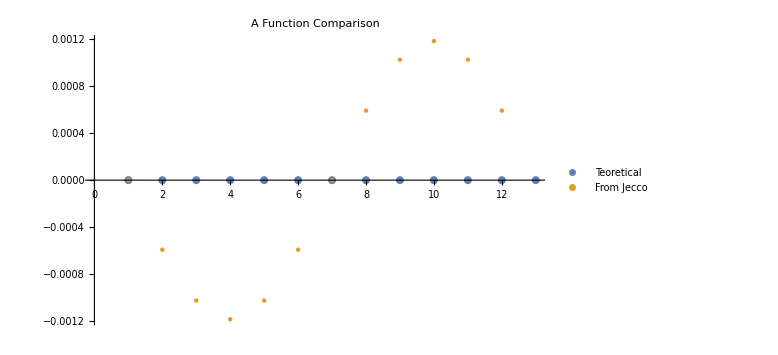

```mathematica
uu=uInnerNodes;
ListPlot[{FyBoostVal[[uu,10,;;]],FyJecco[[;;,uu]]},PlotLegends->{"Teoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.01],Thickness[0.005]} ,{PointSize[0.0055],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

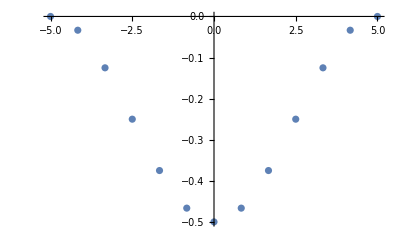

```mathematica
ListPlot[Transpose[{yValues,InitialB[[uu,1,;;]]}]]
```

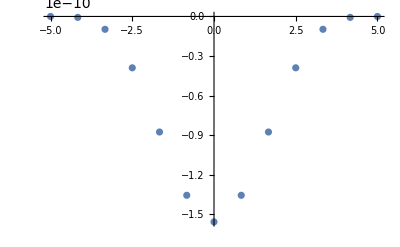

```mathematica
ListPlot[Transpose[{yValues,SfinBoostValues[[uu,1,;;]]}]]
```

```mathematica
D[Interpolation[Transpose[{yValues,InitialB[[uu,1,;;]]}]][y],y]
```

InterpolatingFunction[…][y]

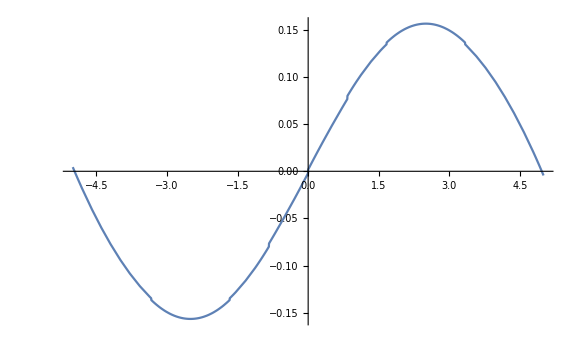

```mathematica
Plot[InterpolatingFunction[…][yy],{yy,yMin,yMax}]
```

#### Inner Nodes

```mathematica
yy=2;
fp=4;
ListPlot[{Transpose[{uValues[[1;;fp]],Fy2Jecco[[yy,1;;fp(*uInnerNodes-1*)]]}],(*Transpose[{uValues[[2;;uInnerNodes-1]],(FyfinBoostVal[[2;;uInnerNodes-1,10,yy]])}],*)Transpose[{uValues[[1;;fp(*uInnerNodes-1*)]],FyJecco[[yy,1;;fp(*uInnerNodes-1*)]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"},Joined->True,Mesh->All, 
 PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

-Graphics-

```mathematica
uValues[[2]]
```

0.00202535131927513050548159714668361504687725757889190224777524705

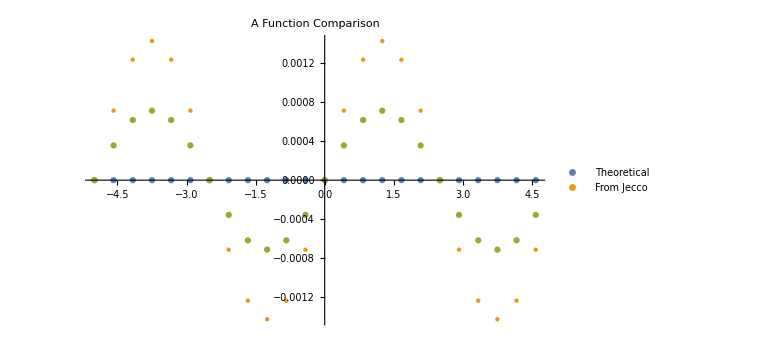

```mathematica
uu=2;
ListPlot[{Transpose[{yValues,FyfinBoostVal[[uu,10,;;]]}],Transpose[{yValues,FyJecco[[;;,uu]]}],Transpose[{yValues,Fy2Jecco[[;;,uu]]}]},PlotLegends->{"Theoretical","From Jecco"}(*,Joined->True*),Mesh->All, 
 PlotStyle -> {{PointSize[0.0078],Thickness[0.0035]} ,{PointSize[0.0055],Thickness[0.0025]}},ImageSize->Large,PlotLabel->"A Function Comparison"]
```

u derivative at u=0 in the Y domain

```mathematica
dyFy=Transpose[{yValues,Table[ Fit[Transpose[{uValues[[1;;uInnerNodes-1]],FyJecco[[i,1;;uInnerNodes-1]]}], {1,x},x][[2,1]],{i,1,yValues//Length}]}];
```

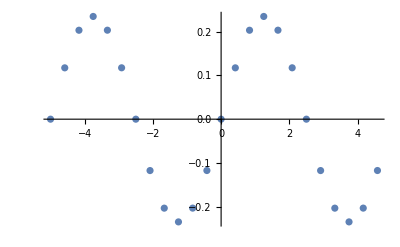

```mathematica
ListPlot[dyFy]
```

Does this satisfy the boundary condition for fy_u?
We impose fy_u = - fy1 * xi + 3/4 * (b13_y+ g3_x), where in this case fy1, xi and g3_x are zero. 
We remain with 3/4*b13_y, let’s compare the two.

```mathematica
uu=1;
b13[y_]:=Interpolation[Transpose[{yValues,InitialB[[uu,1,;;]]}]][y];
dyb13[y_]:=D[b13[yyy],yyy]/.yyy->y
```

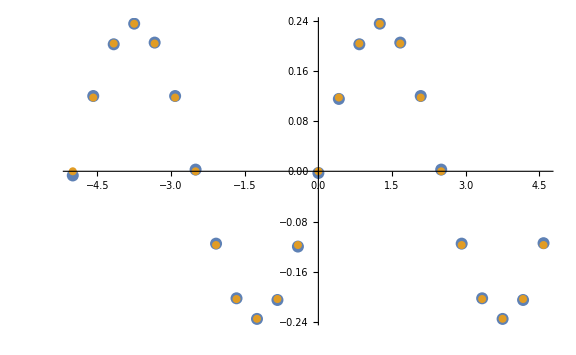

```mathematica
ListPlot[{Transpose[{yValues,3/4 dyb13/@yValues}],dyFy},PlotStyle -> {{PointSize[0.015],Thickness[0.005]} ,{PointSize[0.01],Thickness[0.0015]}},ImageSize->Large]
```

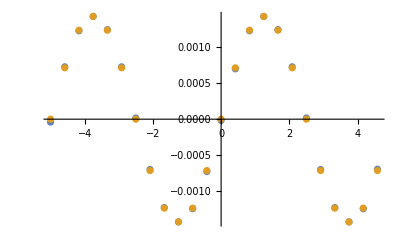

```mathematica
ListPlot[{Transpose[{yValues,(3/4 dyb13/@yValues)(uValues[[2]]-uValues[[1]])}],Transpose[{yValues,FyJecco[[;;,uu]]}]}]
```

## Black Brane

```mathematica
ExportData=Join[{uValues[[;;uInnerNodes]]},Table[uValues[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1)]],{i,0,uOuterDomains-1}]];
```

```mathematica
ExportDataStr=Map[ToString,ExportData,{2}];
```

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportDataStr[[i]],{i,1,ExportAttributes//Length}];
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BB.h5","1"]
```

{0,0.002025351319275130505481597146683615046877257578891902247775247050,0.007937323358440941556909417554031614124335375078973105067867494116,0.01725696330273574679715374637668532234081044003315357861968521977,0.02922924934990567872353629253851883982379975447677315937868883338,0.04288425808633574297781036656918151656044743194370078357909586067,0.05711574191366425702218963343081848343955256805629921642090413933,0.07077075065009432127646370746148116017620024552322684062131116662,0.08274303669726425320284625362331467765918955996684642138031478023,0.09206267664155905844309058244596838587566462492102689493213250588,0.09797464868072486949451840285331638495312274242110809775222475295,0.1000000000000000000000000000000000000000000000000000000000000000}

```mathematica
ExportDataStr[[1]]
```

{0,0.002025351319275130505481597146683615046877257578891902247775247050,0.007937323358440941556909417554031614124335375078973105067867494116,0.01725696330273574679715374637668532234081044003315357861968521977,0.02922924934990567872353629253851883982379975447677315937868883338,0.04288425808633574297781036656918151656044743194370078357909586067,0.05711574191366425702218963343081848343955256805629921642090413933,0.07077075065009432127646370746148116017620024552322684062131116662,0.08274303669726425320284625362331467765918955996684642138031478023,0.09206267664155905844309058244596838587566462492102689493213250588,0.09797464868072486949451840285331638495312274242110809775222475295,0.1000000000000000000000000000000000000000000000000000000000000000}

### S function

#### From Jecco

```mathematica
SBBJecco={0.,-7.767073443078426*^-43,8.868457768027458*^-42,-4.650050025528685*^-41,-9.79745026741803*^-41,-2.478312070370561*^-40,-5.640346544054392*^-40,-1.260302885079073*^-39,-2.8765023141569715*^-39,-3.867537313122834*^-39,-4.3238212364208625*^-39,10.,9.847138697790948,9.417929384270114,8.787491668397436,8.047419736243924,7.279003012518429,6.539888335833936,5.863270419006205,5.263458174539939,4.742631651730042,4.296320094163855,3.9170688918086607,3.596599596811057,3.3269455682694424,3.100968117796434,2.9125293999058273,2.756491123747342,2.628635396344959,2.5255594015143936,2.444569976016672,2.3835901184697508,2.341082177581642,2.3159889344941833,2.3076923014325454,2.2994548986768177,2.275241483452247,2.236478775143221,2.1853301233592415,2.124428696091271,2.056592724083866,1.9845734543797156,1.9108675966336468,1.8376045169006887,1.7665014773303631,1.6988708373599068,1.6356607034687487,1.5775126473256276,1.5248242775813505,1.4778088292185692,1.436547567764204,1.4010333919242703,1.371205629486919,1.346976880402942,1.3282531083991505,1.3149482171008207,1.3069942099840324,1.3043478154723833,1.301712116114504,1.2939169564947643,1.2812877830157992,1.2643342217286977,1.2437066496375944,1.2201453560666387,1.194429247793589,1.167329934411575,1.1395750711070751,1.1118226688637676,1.0846462163316364,1.058529169401708,1.0338667025460433,1.01097247484889,0.990088371998002,0.9713955737726898,0.9550257334893321,0.9410714583359033,0.9295956065024944,0.9206391572086828,0.9142275693146376,0.9103756373616126,0.9090908967608278};
```

#### Analytical

```mathematica
SBB[u_]:=1/u
```

#### Comparison

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(SBB/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],SBBJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

## Benchmark

```mathematica
ClearAll[u2]
```

Solve for θ

```mathematica
Solve[{Σ^2 Sinh[t]==b^3 rho u1 u2},t]
```

{{t→ConditionalExpression[ⅈ π-ArcSinh[(b^3 rho u1 u2)/Σ^2]+2 ⅈ π C[1], C[1]∈ℤ]},{t→ConditionalExpression[ArcSinh[(b^3 rho u1 u2)/Σ^2]+2 ⅈ π C[1], C[1]∈ℤ]}}

Solve for Σ

```mathematica
Σ^4 Cosh[t]^2==1/rho^4(1+(b rho)^3 u1^2)(1+(b rho)^3 u2^2)/.t->ArcSinh[(b^3 rho u1 u2)/Σ^2]
```

(1+(b^6 rho^2 u1^2 u2^2)/Σ^4) Σ^4==((1+b^3 rho^3 u1^2) (1+b^3 rho^3 u2^2))/rho^4

```mathematica
Σ^4(1+((b^3 rho u1 u2)/Σ^2)^2)==1/rho^4(1+(b rho)^3 u1^2)(1+(b rho)^3 u2^2)//Simplify
```

```mathematica
1/rho+b^3 rho^2 (u1^2+u2^2)==rho^3 Σ^4//Solve[#,Σ]&
```

{{Σ→-((1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho},{Σ→-(ⅈ (1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho},{Σ→(ⅈ (1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho},{Σ→((1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho}}

And Sinhθ

```mathematica
(b^3 rho u1 u2)/Σ^2/.Σ->((1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho
```

(b^3 rho^3 u1 u2)/(√(1+b^3 rho^3 u1^2+b^3 rho^3 u2^2))

#### blabla

```mathematica
FxEq=2 u^3 (-6 u Gfin[t,u,z,y]+2 Gfinp[t,u,z,y]+(-3 u Bfin[t,u,z,y]+Bfinp[t,u,z,y]) Sinh[2 u^3 Gfin[t,u,z,y]]) (1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y]) (Derivative[0,0,1][ξ][t,z,y]+(-1+2 u^3 Sfin[t,u,z,y]-u^2 Sfinp[t,u,z,y]) (u F2fin[t,u,z,y]+Derivative[0,0,1][ξ][t,z,y])+u^2 Derivative[0,0,0,1][Sfin][t,u,z,y])+u^3 (1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y])^2 (2 u^3 (-3 u Bfin[t,u,z,y]+Bfinp[t,u,z,y]) Cosh[2 u^3 Gfin[t,u,z,y]] ((3 u Gfin[t,u,z,y]-Gfinp[t,u,z,y]) (u F2fin[t,u,z,y]+Derivative[0,0,1][ξ][t,z,y])+Derivative[0,0,0,1][Gfin][t,u,z,y])+2 (-((12 u^2 Gfin[t,u,z,y]-6 u Gfinp[t,u,z,y]+Gfinpp[t,u,z,y]) (u F2fin[t,u,z,y]+Derivative[0,0,1][ξ][t,z,y]))-3 u Derivative[0,0,0,1][Gfin][t,u,z,y]+Derivative[0,0,0,1][Gfinp][t,u,z,y])-2 u^2 (-3 u Gfin[t,u,z,y]+Gfinp[t,u,z,y]) (-F2fin[t,u,z,y]+u (3 u Bfin[t,u,z,y]-Bfinp[t,u,z,y]) (u F2fin[t,u,z,y]+Derivative[0,0,1][ξ][t,z,y])+u Derivative[0,0,0,1][Bfin][t,u,z,y]-u Derivative[0,1,0,0][F2fin][t,u,z,y])+Sinh[2 u^3 Gfin[t,u,z,y]] (-((12 u^2 Bfin[t,u,z,y]-6 u Bfinp[t,u,z,y]+Bfinpp[t,u,z,y]) (u F2fin[t,u,z,y]+Derivative[0,0,1][ξ][t,z,y]))-3 u Derivative[0,0,0,1][Bfin][t,u,z,y]+Derivative[0,0,0,1][Bfinp][t,u,z,y]-u^2 (-3 u Bfin[t,u,z,y]+Bfinp[t,u,z,y]) (-F2fin[t,u,z,y]+u (3 u Bfin[t,u,z,y]-Bfinp[t,u,z,y]) (u F2fin[t,u,z,y]+Derivative[0,0,1][ξ][t,z,y])+u Derivative[0,0,0,1][Bfin][t,u,z,y]-u Derivative[0,1,0,0][F2fin][t,u,z,y])))+ⅇ^(u^3 Bfin[t,u,z,y]) (4 (1-2 u^3 Sfin[t,u,z,y]+u^2 Sfinp[t,u,z,y]) (Derivative[0,1,0][ξ][t,z,y]+(-1+2 u^3 Sfin[t,u,z,y]-u^2 Sfinp[t,u,z,y]) (u Ffin[t,u,z,y]+Derivative[0,1,0][ξ][t,z,y])+u^2 Derivative[0,0,1,0][Sfin][t,u,z,y])-4 u^2 (1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y]) (-((6 u^2 Sfin[t,u,z,y]-4 u Sfinp[t,u,z,y]+Sfinpp[t,u,z,y]) (u Ffin[t,u,z,y]+Derivative[0,1,0][ξ][t,z,y]))-2 u Derivative[0,0,1,0][Sfin][t,u,z,y]+u (-3 u Bfin[t,u,z,y]+Bfinp[t,u,z,y]) Cosh[u^3 Gfin[t,u,z,y]]^2 (Derivative[0,1,0][ξ][t,z,y]+(-1+2 u^3 Sfin[t,u,z,y]-u^2 Sfinp[t,u,z,y]) (u Ffin[t,u,z,y]+Derivative[0,1,0][ξ][t,z,y])+u^2 Derivative[0,0,1,0][Sfin][t,u,z,y])+Derivative[0,0,1,0][Sfinp][t,u,z,y])+(1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y])^2 (-2 u^6 (-3 u Bfin[t,u,z,y]+Bfinp[t,u,z,y]) Cosh[u^3 Gfin[t,u,z,y]]^2 ((3 u Bfin[t,u,z,y]-Bfinp[t,u,z,y]) (u Ffin[t,u,z,y]+Derivative[0,1,0][ξ][t,z,y])+Derivative[0,0,1,0][Bfin][t,u,z,y])-2 (u^6 (-3 u Gfin[t,u,z,y]+Gfinp[t,u,z,y]+(-3 u Bfin[t,u,z,y]+Bfinp[t,u,z,y]) Sinh[2 u^3 Gfin[t,u,z,y]]) ((3 u Gfin[t,u,z,y]-Gfinp[t,u,z,y]) (u Ffin[t,u,z,y]+Derivative[0,1,0][ξ][t,z,y])+Derivative[0,0,1,0][Gfin][t,u,z,y])+u^3 Cosh[u^3 Gfin[t,u,z,y]]^2 (-((12 u^2 Bfin[t,u,z,y]-6 u Bfinp[t,u,z,y]+Bfinpp[t,u,z,y]) (u Ffin[t,u,z,y]+Derivative[0,1,0][ξ][t,z,y]))-3 u Derivative[0,0,1,0][Bfin][t,u,z,y]+Derivative[0,0,1,0][Bfinp][t,u,z,y]-u^2 (3 u Bfin[t,u,z,y]-Bfinp[t,u,z,y]) (Ffin[t,u,z,y]+u Derivative[0,1,0,0][Ffin][t,u,z,y])))))+2 ⅇ^(u^3 Bfin[t,u,z,y]) u (1+u^3 Sfin[t,u,z,y]+u ξ[t,z,y])^2 (2 Ffin[t,u,z,y]+u (4 Derivative[0,1,0,0][Ffin][t,u,z,y]+u Derivative[0,2,0,0][Ffin][t,u,z,y]));
```

```mathematica
FxEq/.
```

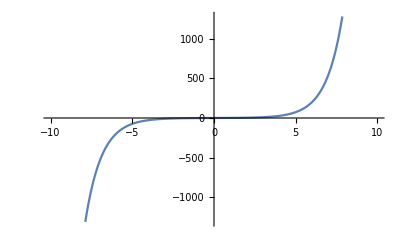

```mathematica
Plot[Sinh[g],{g,-10,10}]
```